## Dynamics of the autonomous system L = L_EH + ξ L_YM +α/m_p^2 L4_1 + κ/m_p^2 L4_2 + θ_4/m_p^2 L4^_Curv+ λ/m_p^2 L4_3 + χ_1 L_(A^4)^(1) + χ_2 L_(A^4)^(2) + χ_3/m_p^2 L_(G^2 A^2)^(1) + χ_4/m_p^2L_(G^2 A^2)^(2) + θ_1 L1^_Curv [ ϵ≡ -H^•/H^2 , P≡ ψ^(••)/(m_p H^2) , X≡ψ^•/(√2 m_p H) , Y≡ψ/(√2 m_p) , Z≡(ψ F)/(√(2 m_p H))≡(ψ (g^2 ξ-6 χ_1-2 χ_2)^(1/4))/(√(2 m_p H)) ] L_(A^4)^(1)=(A_μ^a A_a^μ)(A_ν^b A_b^ν) , L_(A^4)^(2)=(A_μ^a A_b^μ)(A_ν^b A_a^ν) , L_(G^2 A^2)^(1)=(A_μ^a A_νa^)(G_b^μρ G_ρ^(ν b)) , L_(G^2 A^2)^(2)=(A_μ^a A_νb^)(G_^μρb G_ρa^ν) , L4^_Curv=L_μνρσ (A^μa A^νb)(A_ρa^A_σb^) .

## 1. Initialization and global variables

```mathematica
ClearAll["Global`*"]
Needs["Notation`"]
$Assumptions=_∈Reals;
Symbolize[ParsedBoxWrapper[SubscriptBox["_","_"]]]

(* In order to convert variables from MapleEOM to variables from EOM, one must perform the transformation {x=X; y=Y/X; z=Z/(F^4 X)}. *)

vars={ξ,α,κ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, r],Subscript[Ω, m]};
names={YM,alpha,kappa,theta4,chi1,chi2,chi3,chi4,theta1,Hot,Cold};
Fval=(q^2*ξ - 6 Subscript[χ, 1]-2 Subscript[χ, 2])^(1/4);
ToFs[f_]:=f/.q->Sqrt[(F^4+6 Subscript[χ, 1]+2 Subscript[χ, 2])/ξ];
NoMoreZs[f_]:=Simplify[f/.Z->Zval//ToFs,ψ∈Reals];
NoMoreFPϵ[f_]:=((f/.{P->Pval,ϵ->ϵval})//ToFs)/.{F->Fval}//Simplify;
CCoeffs[f_]:=Collect[f,vars];
ToLimit[f_]:=f/.{Z->γ X, Y->β X,ϵ->0};
```

```mathematica
(* Evolution equations are defined *)

fried=-1+(10 X^2 Y^2-188 X Y^3-32 Y^4) α+(8 X Y+6 Y^2) Subscript[θ, 1]+(-64 X Y^3-32 Y^4) Subscript[θ, 4]+(2 X^2 Y^2-20 X Y^3-12 Y^4) κ+(X^2+2 X Y+Y^2+(2*q^2*Z^4)/F^4) ξ-(4*Z^4/F^4)(3 Subscript[χ, 1]+Subscript[χ, 2])+(-4 X^2 Y^2-8 X Y^3-4 Y^4) (Subscript[χ, 3]+Subscript[χ, 4])+Subscript[Ω, m]+Subscript[Ω, r] //Expand//CCoeffs;

eq1=3-2 ϵ+α (614 X^2 Y^2+104 √2 P Y^3+316 X Y^3-340 Y^4+124 Y^4 ϵ)+(-8 X^2-4 √2 P Y-24 X Y-6 Y^2+4 Y^2 ϵ) Subscript[θ, 1]+(192 X^2 Y^2+32 √2 P Y^3+256 X Y^3+32 Y^4) Subscript[θ, 4]+(70 X^2 Y^2+12 √2 P Y^3+108 X Y^3+24 Y^4-4 Y^4 ϵ) κ+(X^2+2 X Y+Y^2+(2*q^2*Z^4)/F^4) ξ-(4*Z^4/F^4)(3 Subscript[χ, 1]+Subscript[χ, 2])+(4 X^2 Y^2+8 X Y^3+4 Y^4)( Subscript[χ, 3]+Subscript[χ, 4])+Subscript[Ω, r]//Expand//CCoeffs;

eq2=α (10 X^2 Y+5 √2 P Y^2+30 X Y^2-218 Y^3+94 Y^3 ϵ)+(6 Y-4 Y ϵ) Subscript[θ, 1]+(-32 Y^3+32 Y^3 ϵ) Subscript[θ, 4]+(2 X^2 Y+√2 P Y^2+6 X Y^2-6 Y^3+10 Y^3 ϵ) κ+(P/√2+3 X+2 Y+(4*q^2*Z^4)/(F^4*Y)-Y ϵ) ξ-(8*Z^4/(F^4*Y))(3 Subscript[χ, 1]+Subscript[χ, 2])+(-4 X^2 Y-2 √2 P Y^2-12 X Y^2-4 Y^3+4 Y^3 ϵ) (Subscript[χ, 3]+Subscript[χ, 4])//Expand//CCoeffs;

Print["\n\nFried → ",fried," == 0"];Print["\nEq1 → ",eq1," == 0"];Print["\nEq2 → ",eq2," == 0\n\n"];
```

Fried → -1+(10 X^2 Y^2-188 X Y^3-32 Y^4) α+(8 X Y+6 Y^2) θ_1+(-64 X Y^3-32 Y^4) θ_4+(2 X^2 Y^2-20 X Y^3-12 Y^4) κ+(X^2+2 X Y+Y^2+(2 q^2 Z^4)/F^4) ξ-(12 Z^4 χ_1)/F^4-(4 Z^4 χ_2)/F^4+(-4 X^2 Y^2-8 X Y^3-4 Y^4) χ_3+(-4 X^2 Y^2-8 X Y^3-4 Y^4) χ_4+Ω_m+Ω_r == 0

Eq1 → 3-2 ϵ+α (614 X^2 Y^2+104 √2 P Y^3+316 X Y^3-340 Y^4+124 Y^4 ϵ)+(-8 X^2-4 √2 P Y-24 X Y-6 Y^2+4 Y^2 ϵ) θ_1+(192 X^2 Y^2+32 √2 P Y^3+256 X Y^3+32 Y^4) θ_4+(70 X^2 Y^2+12 √2 P Y^3+108 X Y^3+24 Y^4-4 Y^4 ϵ) κ+(X^2+2 X Y+Y^2+(2 q^2 Z^4)/F^4) ξ-(12 Z^4 χ_1)/F^4-(4 Z^4 χ_2)/F^4+(4 X^2 Y^2+8 X Y^3+4 Y^4) χ_3+(4 X^2 Y^2+8 X Y^3+4 Y^4) χ_4+Ω_r == 0

Eq2 → α (10 X^2 Y+5 √2 P Y^2+30 X Y^2-218 Y^3+94 Y^3 ϵ)+(6 Y-4 Y ϵ) θ_1+(-32 Y^3+32 Y^3 ϵ) θ_4+(2 X^2 Y+√2 P Y^2+6 X Y^2-6 Y^3+10 Y^3 ϵ) κ+(P/(√2)+3 X+2 Y+(4 q^2 Z^4)/(F^4 Y)-Y ϵ) ξ-(24 Z^4 χ_1)/(F^4 Y)-(8 Z^4 χ_2)/(F^4 Y)+(-4 X^2 Y-2 √2 P Y^2-12 X Y^2-4 Y^3+4 Y^3 ϵ) χ_3+(-4 X^2 Y-2 √2 P Y^2-12 X Y^2-4 Y^3+4 Y^3 ϵ) χ_4 == 0

```mathematica
(* Friedmann equation is solved for Z *)
solu=Solve[fried==0/.Z->(Z4)^(1/4),Z4]//Simplify;
Zval=(solu[[1,1,2]])^(1/4)(ψ/Abs[ψ])//ToFs //Simplify;

(* The real solution for Z whose magnitude is given by |Z| = (Z^4)^(1/4) and Sgn[Z]=Sgn(ψ) is chosen, in accordance with its definition *)

PyE=Solve[eq1==0&&eq2==0,{P,ϵ}]//Simplify;
Pval=PyE[[1,1,2]]//NoMoreZs;ϵval=PyE[[1,2,2]]//NoMoreZs;  
Print["\n\nZ == ",Zval]; Print["\nP == ",Pval]; Print["\nϵ == ",ϵval,"\n\n"];
```

Z == (ψ (1-Y^2 (6 θ_1+ξ)+4 Y^4 (8 α+8 θ_4+3 κ+χ_3+χ_4)+2 X Y (-4 θ_1-ξ+2 Y^2 (47 α+16 θ_4+5 κ+2 χ_3+2 χ_4))-X^2 (ξ+2 Y^2 (5 α+κ-2 (χ_3+χ_4)))-Ω_m-Ω_r)^(1/4))/(2^(1/4) Abs[ψ])

P == -((-Y^2 (-4 θ_1-ξ+2 Y^2 (47 α+16 θ_4+5 κ+2 χ_3+2 χ_4)) (4-12 Y^2 θ_1+Y^4 (-308 α+64 θ_4+36 κ+8 χ_3+8 χ_4)+4 X^2 (-2 θ_1+Y^2 (151 α+48 θ_4+17 κ+2 χ_3+2 χ_4))+8 X (-4 Y θ_1+Y^3 (63 α+2 (20 θ_4+8 κ+χ_3+χ_4)))-Ω_m)-2 (-1+2 Y^2 θ_1+Y^4 (62 α-2 κ)) (-X Y (-16 θ_1-ξ+2 Y^2 (203 α+64 θ_4+23 κ+2 χ_3+2 χ_4))+2 X^2 (ξ+Y^2 (5 α+κ-2 (χ_3+χ_4)))+2 (-1+3 Y^2 θ_1+Y^4 (77 α-16 θ_4-9 κ-2 χ_3-2 χ_4)+Ω_m+Ω_r)))/(√2 Y (-4 Y^2 (-θ_1+Y^2 (26 α+8 θ_4+3 κ)) (-4 θ_1-ξ+2 Y^2 (47 α+16 θ_4+5 κ+2 χ_3+2 χ_4))+(-1+2 Y^2 θ_1+Y^4 (62 α-2 κ)) (ξ+2 Y^2 (5 α+κ-2 (χ_3+χ_4))))))

ϵ == ((-8 X Y^3 (36 α-8 θ_4-5 κ) ξ+2 X Y ξ^2-8 X Y^5 (77 α-16 θ_4-9 κ-2 χ_3-2 χ_4) (5 α+κ-2 (χ_3+χ_4))+2 Y^4 (-1526 α θ_1-320 θ_1 θ_4-102 θ_1 κ-373 α ξ-48 θ_4 ξ-11 κ ξ-4 θ_1 χ_3-4 θ_1 χ_4+2 X^2 (203 α+64 θ_4+23 κ+2 χ_3+2 χ_4) (5 α+κ-2 (χ_3+χ_4)))+8 Y^6 (5243 α^2+256 θ_4^2+24 κ^2+κ χ_3-2 χ_3^2+κ χ_4-4 χ_3 χ_4-2 χ_4^2+8 θ_4 (19 κ+2 (χ_3+χ_4))+α (2616 θ_4+755 κ+279 (χ_3+χ_4)))+ξ (3+X^2 (-8 θ_1+ξ)+Ω_r)-(16 θ_1+ξ-2 Y^2 (203 α+64 θ_4+23 κ+2 χ_3+2 χ_4)) (-1+Y^2 (6 θ_1+ξ)-4 Y^4 (8 α+8 θ_4+3 κ+χ_3+χ_4)-2 X Y (-4 θ_1-ξ+2 Y^2 (47 α+16 θ_4+5 κ+2 χ_3+2 χ_4))+X^2 (ξ+2 Y^2 (5 α+κ-2 (χ_3+χ_4)))+Ω_m+Ω_r)+Y^2 (48 θ_1^2+6 κ+10 θ_1 ξ+192 X^2 θ_4 ξ+72 X^2 κ ξ+ξ^2-12 χ_3-12 χ_4+2 κ Ω_r-4 χ_3 Ω_r-4 χ_4 Ω_r+2 α (312 X^2 ξ+5 (3+Ω_r))))/(2 (ξ+2 Y^2 (5 α+8 θ_1^2+κ+θ_1 ξ-2 χ_3-2 χ_4)-2 Y^4 (406 α θ_1+128 θ_1 θ_4+46 θ_1 κ+83 α ξ+16 θ_4 ξ+5 κ ξ+4 θ_1 χ_3+4 θ_1 χ_4)+4 Y^6 (2289 α^2+256 θ_4^2+16 θ_4 (11 κ+2 (χ_3+χ_4))+κ (31 κ+10 (χ_3+χ_4))+2 α (792 θ_4+258 κ+83 (χ_3+χ_4))))))

```mathematica
For[i=1,i≤Length[vars],i++,Ω[names[[i]]]=Coefficient[fried,vars[[i]]]vars[[i]];
NP[names[[i]]]= Coefficient[eq1,vars[[i]]](vars[[i]]/3);]

Ω[Gal]=1-Subscript[Ω, m]-Subscript[Ω, r]; NP[Gal]=(1/3) (2 ϵ-3-Subscript[Ω, r]);
Title={" ","Specie"," ","Normalized energy density"," ","Normalized pressure"," ","State parameter",""}; Print[];
Prepend[Table[{" ",vars[[i]]," ",Ω[names[[i]]]," ",NP[names[[i]]]," ",NP[names[[i]]]/Ω[names[[i]]]//Factor," "},{i,Length[vars]}],%];
Print[%//MatrixForm]; Print[];
```

(  | Specie |   | Normalized energy density |   | Normalized pressure |   | State parameter | 
  | ξ |   | (X^2+2 X Y+Y^2+(2 q^2 Z^4)/F^4) ξ |   | 1/3 (X^2+2 X Y+Y^2+(2 q^2 Z^4)/F^4) ξ |   | 1/3 |  
  | α |   | (10 X^2 Y^2-188 X Y^3-32 Y^4) α |   | 1/3 α (614 X^2 Y^2+104 √2 P Y^3+316 X Y^3-340 Y^4+124 Y^4 ϵ) |   | (307 X^2+52 √2 P Y+158 X Y-170 Y^2+62 Y^2 ϵ)/(3 (5 X^2-94 X Y-16 Y^2)) |  
  | κ |   | (2 X^2 Y^2-20 X Y^3-12 Y^4) κ |   | 1/3 (70 X^2 Y^2+12 √2 P Y^3+108 X Y^3+24 Y^4-4 Y^4 ϵ) κ |   | (35 X^2+6 √2 P Y+54 X Y+12 Y^2-2 Y^2 ϵ)/(3 (X^2-10 X Y-6 Y^2)) |  
  | θ_4 |   | (-64 X Y^3-32 Y^4) θ_4 |   | 1/3 (192 X^2 Y^2+32 √2 P Y^3+256 X Y^3+32 Y^4) θ_4 |   | -(6 X^2+√2 P Y+8 X Y+Y^2)/(3 Y (2 X+Y)) |  
  | χ_1 |   | -(12 Z^4 χ_1)/F^4 |   | -(4 Z^4 χ_1)/F^4 |   | 1/3 |  
  | χ_2 |   | -(4 Z^4 χ_2)/F^4 |   | -(4 Z^4 χ_2)/(3 F^4) |   | 1/3 |  
  | χ_3 |   | (-4 X^2 Y^2-8 X Y^3-4 Y^4) χ_3 |   | 1/3 (4 X^2 Y^2+8 X Y^3+4 Y^4) χ_3 |   | -1/3 |  
  | χ_4 |   | (-4 X^2 Y^2-8 X Y^3-4 Y^4) χ_4 |   | 1/3 (4 X^2 Y^2+8 X Y^3+4 Y^4) χ_4 |   | -1/3 |  
  | θ_1 |   | (8 X Y+6 Y^2) θ_1 |   | 1/3 (-8 X^2-4 √2 P Y-24 X Y-6 Y^2+4 Y^2 ϵ) θ_1 |   | -(4 X^2+2 √2 P Y+12 X Y+3 Y^2-2 Y^2 ϵ)/(3 Y (4 X+3 Y)) |  
  | Ω_r |   | Ω_r |   | Ω_r/3 |   | 1/3 |  
  | Ω_m |   | Ω_m |   | 0 |   | 0 |  )

## 2. Critical points

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 1],Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[χ, 34],Subscript[Ω, r],Subscript[Ω, m],β,γ,P,ϵ];
Xp=P/Sqrt[2]+X ϵ;
Yp=X;
Ωrp=2 Subscript[Ω, r](ϵ-2); 
Ωmp=Subscript[Ω, m](2ϵ-3);
Print["\n[ ( Y' = Ω_m' = Ω_r' = 0 ) ∧ ( ϵ < 1 ) ] ↔ ",conds=Reduce[Yp==0&&Ωmp==0&&Ωrp==0&&ϵ<1,{X,Subscript[Ω, m],Subscript[Ω, r],ϵ}]];
Print["\n[X'=",Simplify[Xp,conds],"] [Y'=",Simplify[Yp,conds],"] [Ω_r'=",Simplify[Ωrp,conds],"] [Ω_m'=",Simplify[Ωmp,conds],"]"]
```

[ ( Y' = Ω_m' = Ω_r' = 0 ) ∧ ( ϵ < 1 ) ] ↔ X==0&&Ω_m==0&&Ω_r==0&&ϵ<1

[X'=P/(√2)] [Y'=0] [Ω_r'=0] [Ω_m'=0]

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 1],Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[χ, 34],Subscript[Ω, r],Subscript[Ω, m],β,γ,P,ϵ]; Subscript[χ, 3]=Subscript[χ, 34]-Subscript[χ, 4]; ξ=1;
Print["\n<< X'==0 along {X,Ω_m,Ω_r}=0 if >>\n"]; XCritPoints=Reduce[Simplify[Numerator[Pval],conds]==0/.Y->(Y2)^(1/2),Y2]//Factor;
(* Denominator[Pval]==0 happens under extremely precise conditions, this is so improbable that it doesn't represent a significant problem *)

For[i=1,i≤Length[XCritPoints],i++,Print[StringForm[" ``   ",i],XCritPoints[[i]]]]; Print[];
```

<< X'==0 along {X,Ω_m,Ω_r}=0 if >>

77 α-16 θ_4-9 κ-2 χ_34≠0&&(Y2==-(3 θ_1+√(308 α+9 θ_1^2-64 θ_4-36 κ-8 χ_34))/(2 (77 α-16 θ_4-9 κ-2 χ_34))||Y2==(-3 θ_1+√(308 α+9 θ_1^2-64 θ_4-36 κ-8 χ_34))/(2 (77 α-16 θ_4-9 κ-2 χ_34)))

8 α+8 θ_4+3 κ+χ_34≠0&&(Y2==-(-1-6 θ_1+√(1-128 α+12 θ_1+36 θ_1^2-128 θ_4-48 κ-16 χ_34))/(8 (8 α+8 θ_4+3 κ+χ_34))||Y2==(1+6 θ_1+√(1-128 α+12 θ_1+36 θ_1^2-128 θ_4-48 κ-16 χ_34))/(8 (8 α+8 θ_4+3 κ+χ_34)))

α==1/8 (-8 θ_4-3 κ-χ_34)&&1+6 θ_1≠0&&Y2==1/(1+6 θ_1)

α==1/77 (16 θ_4+9 κ+2 χ_34)&&θ_1≠0&&Y2==1/(3 θ_1)

```mathematica
Print["\nFor the previous solutions, the values for ϵ are the following: [ with r=1-4(32α-3θ_1(1+3θ_1)+4(8θ_4+3κ+χ_34)) ]\n"]

ϵval/.{X->0,Y->Sqrt[(-3 Subscript[θ, 1]-√(308 α+9 Subscript[θ, 1]^2-64 Subscript[θ, 4]-36 κ-8 Subscript[χ, 34]))/(2 (77 α-16 Subscript[θ, 4]-9 κ-2 Subscript[χ, 34]))],Subscript[Ω, m]->0,Subscript[Ω, r]->0}//Factor
(ϵval/.{X->0,Y->Sqrt[(1+6 Subscript[θ, 1]-√(1-128 α+12 Subscript[θ, 1]+36 Subscript[θ, 1]^2-128 Subscript[θ, 4]-48 κ-16 Subscript[χ, 34]))/(8 (8 α+8 Subscript[θ, 4]+3 κ+Subscript[χ, 34]))],Subscript[Ω, m]->0,Subscript[Ω, r]->0}//FullSimplify//Factor)/.{Subscript[χ, 34]->(1/16) (1-r-128 α+12 Subscript[θ, 1]+36 Subscript[θ, 1]^2-128 Subscript[θ, 4]-48 κ)}//FullSimplify
ϵval/.{X->0,Y->Sqrt[1/(1+6 Subscript[θ, 1])],α->(1/8) (-8 Subscript[θ, 4]-3 κ-Subscript[χ, 34]),Subscript[Ω, m]->0,Subscript[Ω, r]->0}//Factor
ϵval/.{X->0,Y->Sqrt[1/(3 Subscript[θ, 1])],α->(1/77) (16 Subscript[θ, 4]+9 κ+2 Subscript[χ, 34]),Subscript[Ω, m]->0,Subscript[Ω, r]->0}//Factor
```

For the previous solutions, the values for ϵ are the following: [ with r=1-4(32α-3θ_1(1+3θ_1)+4(8θ_4+3κ+χ_34)) ]

0

3-(2 (r+√r (1+6 θ_1)))/(1+r-248 α+4 θ_1 (2+3 θ_1)+√r (2+8 θ_1)+8 κ)

(8+72 θ_1+144 θ_1^2+744 θ_4+303 κ+93 χ_34)/(4+40 θ_1+96 θ_1^2+248 θ_4+101 κ+31 χ_34)

0

```mathematica
(* The following points exhibit ϵ=0 along X=0 - They aren't necessarily critical but they might be interesting to study too *)
Clear[ξ,α,κ,λ,Subscript[θ, 1],Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[χ, 34],Subscript[Ω, r],Subscript[Ω, m],β,γ,P,ϵ];  Subscript[χ, 3]=Subscript[χ, 34]-Subscript[χ, 4]; ξ=1;
Print["\n<< ϵ==0 is ensured if >>\n"]; ϵNullPoints=Reduce[Numerator[Simplify[ϵval,conds]]==0/.Y->(Y2)^(1/2),Y2]//Factor;  
(* Denominator[ϵval]==0 happens under extremely precise conditions, this is so improbable that it doesn't represent a significant problem *)
For[i=1,i≤Length[ϵNullPoints],i++,Print[StringForm[" ``   ",i],ϵNullPoints[[i]]]]; Print[];
```

<< ϵ==0 is ensured if >>

θ_1==-1/4&&α==1/47 (-16 θ_4-5 κ-2 χ_34)

77 α-16 θ_4-9 κ-2 χ_34≠0&&(Y2==-(3 θ_1+√(308 α+9 θ_1^2-64 θ_4-36 κ-8 χ_34))/(2 (77 α-16 θ_4-9 κ-2 χ_34))||Y2==(-3 θ_1+√(308 α+9 θ_1^2-64 θ_4-36 κ-8 χ_34))/(2 (77 α-16 θ_4-9 κ-2 χ_34)))

47 α+16 θ_4+5 κ+2 χ_34≠0&&Y2==(1+4 θ_1)/(2 (47 α+16 θ_4+5 κ+2 χ_34))

α==1/77 (16 θ_4+9 κ+2 χ_34)&&θ_1≠0&&Y2==1/(3 θ_1)

```mathematica
(* RUPTURE POINTS - They satisfy [Subscript[θ, 1]=0,Z=0,ϵ->∞] and divide the Phase portrait into 2 regions. *)

Clear[X2];sol={}; WeKnow=(X≠0)&&(R>2);
Clear[ξ,α,κ,λ,Subscript[θ, 1],Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[χ, 34],Subscript[Ω, r],Subscript[Ω, m],β,γ,P,ϵ]; Subscript[χ, 3]=Subscript[χ, 34]-Subscript[χ, 4]; {ξ,Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]}={1,0,0,0}; Print[];
Reduce[(Zval^4==0/.{Y->R X}//Simplify)&&WeKnow,Reals]//Factor;
Reduce[((Denominator[ϵval]/.{Y->R X})==0//Simplify)&&WeKnow,Reals]//Factor;
Reduce[%&&%%&&WeKnow,Reals]//Factor;

aux=Reduce[(Denominator[Pval]/.{Y->R X})==0&&%&&WeKnow,Reals]//Factor
For[i=1,i≤Length[aux],i++,AppendTo[sol,FullSimplify[aux[[i]],WeKnow]]];
solus=Apply[And,sol];
Need[1]=Solve[solus[[2]]/.X->(X4)^(1/4),X4][[1,1]]
X2=Sqrt[%[[2]]]; copy=Simplify[solus[[1]]/.{X->(X2)^(1/2)},WeKnow];
FullSimplify[copy[[1]]//Expand,WeKnow];
Need[2]=((%[[1]]+%[[2]]//FullSimplify)*((52-31 R) α+16 Subscript[θ, 4]+(6+R) κ)//FullSimplify)+((%[[3]]+%[[4]]//FullSimplify)*((52-31 R) α+16 Subscript[θ, 4]+(6+R) κ)//FullSimplify)==0
Clear[ξ,Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]]; Print[];
Clear[X2];
```

((X<0&&R>2)||(X>0&&R>2))&&χ_34==-(-5+47 R+52 R X^2+21 R^2 X^2-31 R^3 X^2-160 R^3 X^4 θ_4-160 R^4 X^4 θ_4+992 R^5 X^4 θ_4+44 R^3 X^4 κ-28 R^4 X^4 κ+404 R^5 X^4 κ)/(4 R^3 (1+R) (-52+31 R) X^4)&&α==(1+32 R^3 X^4 θ_4+12 R^3 X^4 κ+2 R^4 X^4 κ)/(2 R^3 (-52+31 R) X^4)

X4→1/(2 R^3 (-52 α+31 R α-16 θ_4-6 κ-R κ))

-√2 (1+R) √((-52+31 R) α-16 θ_4-(6+R) κ)+2 √R ((-5+47 R) α+16 R θ_4-κ+5 R κ+2 (1+R) χ_34)==0

## 3. Asymptotic behaviour ( Y → βX , Z → γX )

```mathematica
XpLimit=P/Sqrt[2]; (* Given that "fried" and "XpLimit/X" only depend on even powers of X, the following computations hold for X -> ±∞ *)

Clear[ξ,α,κ,λ,Subscript[θ, 1],Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[χ, 34],Subscript[Ω, r],Subscript[Ω, m],β,γ,P,ϵ]; Subscript[χ, 3]=Subscript[χ, 34]-Subscript[χ, 4]; 

aux=Solve[(eq1//ToFs//ToLimit)==0,{P}] //Simplify; (* Y'=X->βX' => (1/β-X'/X)-> 0 <=> β,X≠0 *)
P=aux[[1,1,2]]; Print["\nEq3 →  ",(eq3=(1/β)-Limit[XpLimit/X,X->Infinity]==0//Simplify)]; Clear[P]; 

aux=Solve[(eq2//ToFs//ToLimit)==0,{P}]//Simplify; (* Z'->γX'->(γ/β)X => (1/β-X'/X)-> 0 <=> β,X≠0 *)
P=aux[[1,1,2]]; Print["\nEq4 →  ",(eq4=(1/β)-Limit[XpLimit/X,X->Infinity]==0//Simplify)]; Clear[P]; 

Print["\nEq5 →  ",(eq5=Limit[(fried//ToFs//ToLimit)/(X^4),X->Infinity]==0//Simplify),"\n\n"];
```

Eq3 →  (α β^2 (411+158 β-170 β^2)+γ^4+β^2 (16 (8+8 β+β^2) θ_4+(47+54 β+12 β^2) κ+2 (1+β)^2 χ_34))/(β (26 α+8 θ_4+3 κ))==0

Eq4 →  (α β^2 (-10-15 β+109 β^2)-2 γ^4+β^2 (-2 κ-3 β (κ-2 χ_34)+4 χ_34+β^2 (16 θ_4+3 κ+2 χ_34)))/(β (5 α+κ-2 χ_34))==0

Eq5 →  β^2 (α (-5+94 β+16 β^2)-κ+2 χ_34+2 β^2 (8 θ_4+3 κ+χ_34)+2 β (16 θ_4+5 κ+2 χ_34))==γ^4

```mathematica
Print[]; asymptotes=Solve[eq3&&eq4&&eq5/.{γ->γ4^(1/4)},{β,γ4}]//Simplify;
Print["Number of soutions: ",Length[asymptotes]," - The first one was assigned to βval & γval. \n"]
Print["β = ",βval=asymptotes[[1,1,2]]//Simplify,"\n"];
Print["|γ| = ",γvalAbs=asymptotes[[1,2,2]]^(1/4)//FullSimplify,"\n"];
γval=(βval/Abs[βval])γvalAbs; (* By definition, (Z/Y)=(γ/β)>0, hence Sgn[γ]=Sgn[β] *)
Print[];
```

Number of soutions: 1 - The first one was assigned to βval & γval.

β = (203 α+64 θ_4+23 κ+2 χ_34)/(77 α-16 θ_4-9 κ-2 χ_34)

|γ| = (((917 α+128 θ_4+33 κ-2 χ_34) (203 α+64 θ_4+23 κ+2 χ_34)^2 (2289 α^2+256 θ_4^2+176 θ_4 κ+31 κ^2+32 θ_4 χ_34+10 κ χ_34+2 α (792 θ_4+258 κ+83 χ_34)))/(-77 α+16 θ_4+9 κ+2 χ_34)^4)^(1/4)

## 4. Healthy subspaces ( mathematical consistency - ghosts - Laplacian instabilities - causality - gravitational waves )

### Preliminars ( Taken from the code ‘EOM’ )

```mathematica
KM=({{1/8 (2+2 Subscript[θ, 1] (ψ̂)^2+(61 α-16 Subscript[θ, 4]+19 κ) (ψ̂)^4), -Subscript[θ, 1] ψ̂+(-5 α+4 Subscript[θ, 4]-(3 κ)/2) (ψ̂)^3, 0, 0}, {-Subscript[θ, 1] ψ̂+(-5 α+4 Subscript[θ, 4]-(3 κ)/2) (ψ̂)^3, ξ+(5 α+κ-2 Subscript[χ, 34]) (ψ̂)^2, 0, 0}, {0, 0, 1/8 (2+2 Subscript[θ, 1] (ψ̂)^2+(61 α-16 Subscript[θ, 4]+19 κ) (ψ̂)^4), -Subscript[θ, 1] ψ̂+(-5 α+4 Subscript[θ, 4]-(3 κ)/2) (ψ̂)^3}, {0, 0, -Subscript[θ, 1] ψ̂+(-5 α+4 Subscript[θ, 4]-(3 κ)/2) (ψ̂)^3, ξ+(5 α+κ-2 Subscript[χ, 34]) (ψ̂)^2}});
CM=({{0, 0, 0, -λ (ψ̂)^3}, {0, 0, λ (ψ̂)^3, 0}, {0, λ (ψ̂)^3, 0, 0}, {-λ (ψ̂)^3, 0, 0, 0}}); LM=({{-1/8 (2+6 Subscript[θ, 1] (ψ̂)^2+(81 α-κ) (ψ̂)^4), Subscript[θ, 1] ψ̂+(5 α-κ/2) (ψ̂)^3, 0, 0}, {Subscript[θ, 1] ψ̂+(5 α-κ/2) (ψ̂)^3, -ξ-(5 α+κ-4 Subscript[χ, 34]+2 Subscript[χ, 4]) (ψ̂)^2, 0, 0}, {0, 0, -1/8 (2+6 Subscript[θ, 1] (ψ̂)^2+(81 α-κ) (ψ̂)^4), Subscript[θ, 1] ψ̂+(5 α-κ/2) (ψ̂)^3}, {0, 0, Subscript[θ, 1] ψ̂+(5 α-κ/2) (ψ̂)^3, -ξ-(5 α+κ-4 Subscript[χ, 34]+2 Subscript[χ, 4]) (ψ̂)^2}});

KEigenVals=Eigenvalues[KM]//DeleteDuplicates//Simplify;
lambdaSum=KEigenVals[[1]]+KEigenVals[[2]]//FullSimplify; lambdaPrd=KEigenVals[[1]]KEigenVals[[2]]//FullSimplify;
EvenPoly[coeffs_,degree_]:=Table[Subscript[coeffs,2j]x^(2j),{j,0,degree/2}]//Apply[Plus,#]&
DepsOn[expr_,params_]:=Select[params,Internal`DependsOnQ[expr,#]&]; params={α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]};
PolyT=EvenPoly[t,4]; PolyD=EvenPoly[d,6];

consT=Reduce[Resolve[ForAll[x,PolyT>0]],DeleteCases[CoefficientList[PolyT,x],0],Reals,Backsubstitution->True]//Factor;
consD=Reduce[Resolve[ForAll[x,PolyD>0]],DeleteCases[CoefficientList[PolyD,x],0],Reals,Backsubstitution->True]//Factor;
Solve[Simplify[Det[cs2 KM-Sqrt[cs2]CM+LM],cs2>0]==0,cs2]//DeleteDuplicates//Simplify;
{cs21,cs22}={%[[1,1,2]]//Simplify,%[[2,1,2]]//Simplify}; cssum=cs21+cs22 //FullSimplify; csprd=cs21*cs22 //FullSimplify;
Print["\nλ_++ λ_- = ",lambdaSum,"\n\nλ_+* λ_- = ",lambdaPrd,"\n\nc_(s, SubscriptBox[h, +±])^2+ c_(s, SubscriptBox[γ, +±])^2 = ",cssum,"\n\nc_(s, SubscriptBox[h, +±])^2* c_(s, SubscriptBox[γ, +±])^2 = ",csprd,"\n"]
```

λ_++ λ_- = 1/4+ξ+(5 α+θ_1/4+κ-2 χ_34) (ψ̂)^2+1/8 (61 α-16 θ_4+19 κ) (ψ̂)^4

λ_+* λ_- = 1/8 (2 ξ+2 (5 α+κ+θ_1 (-4 θ_1+ξ)-2 χ_34) (ψ̂)^2+(-70 α θ_1+64 θ_1 θ_4-22 θ_1 κ+61 α ξ-16 θ_4 ξ+19 κ ξ-4 θ_1 χ_34) (ψ̂)^4+(105 α^2-128 θ_4^2+80 θ_4 κ+κ^2+2 α (120 θ_4+18 κ-61 χ_34)+32 θ_4 χ_34-38 κ χ_34) (ψ̂)^6)

c_(s, SubscriptBox[h, +±])^2+ c_(s, SubscriptBox[γ, +±])^2 = ((4 ξ+4 (5 α+κ+2 θ_1 (-2 θ_1+ξ)-3 χ_34+χ_4) (ψ̂)^2+2 (-8 θ_4 ξ+9 κ ξ+α (-60 θ_1+71 ξ)+2 θ_1 (16 θ_4-2 κ-5 χ_34+χ_4)) (ψ̂)^4+2 (155 α^2+4 λ^2-8 θ_4 (3 κ-4 χ_34+2 χ_4)+κ (15 κ-37 χ_34+19 χ_4)+α (120 θ_4+76 κ-203 χ_34+61 χ_4)) (ψ̂)^6)/(2 ξ+2 (5 α+κ+θ_1 (-4 θ_1+ξ)-2 χ_34) (ψ̂)^2+(-70 α θ_1+64 θ_1 θ_4-22 θ_1 κ+61 α ξ-16 θ_4 ξ+19 κ ξ-4 θ_1 χ_34) (ψ̂)^4+(105 α^2-128 θ_4^2+80 θ_4 κ+κ^2+2 α (120 θ_4+18 κ-61 χ_34)+32 θ_4 χ_34-38 κ χ_34) (ψ̂)^6))

c_(s, SubscriptBox[h, +±])^2* c_(s, SubscriptBox[γ, +±])^2 = ((2 ξ+2 (5 α-4 θ_1^2+κ+3 θ_1 ξ-4 χ_34+2 χ_4) (ψ̂)^2+(-50 α θ_1+14 θ_1 κ+81 α ξ-κ ξ-24 θ_1 χ_34+12 θ_1 χ_4) (ψ̂)^4+(205 α^2+κ (-3 κ+4 χ_34-2 χ_4)+2 α (58 κ+81 (-2 χ_34+χ_4))) (ψ̂)^6)/(2 ξ+2 (5 α+κ+θ_1 (-4 θ_1+ξ)-2 χ_34) (ψ̂)^2+(-70 α θ_1+64 θ_1 θ_4-22 θ_1 κ+61 α ξ-16 θ_4 ξ+19 κ ξ-4 θ_1 χ_34) (ψ̂)^4+(105 α^2-128 θ_4^2+80 θ_4 κ+κ^2+2 α (120 θ_4+18 κ-61 χ_34)+32 θ_4 χ_34-38 κ χ_34) (ψ̂)^6))

### Only α [ β > 0 ]

#### General expressions

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]];
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,α,0,0,0,0,0,0,0,0,0};
SolveForThis={α}; AssumeThis=(α≠0);

Print["\n",fried==0/.F->Fval,"\n",eq1==0/.F->Fval,"\n",eq2==0/.F->Fval,"\n\n","Z^4 = ",Z4=(Zval^4//Factor//FullSimplify),"\n","P = ",(Pval//Factor//FullSimplify),"\n","ϵ = ",ϵxy=(ϵval//Factor//FullSimplify),"\nλ_+ + λ_- = ",lambdaSum,"\nλ_+ * λ_- = ",lambdaPrd,"\n\nc_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum,"\nc_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",csprd,"\n\nβ = ",(βval//FullSimplify)," , γ^4 = ",(γvalAbs^4//Simplify),"\n"]
```

-1+X^2+2 X Y+Y^2+2 Z^4+(10 X^2 Y^2-188 X Y^3-32 Y^4) α+Ω_m+Ω_r==0
3+X^2+2 X Y+Y^2+2 Z^4-2 ϵ+α (614 X^2 Y^2+104 √2 P Y^3+316 X Y^3-340 Y^4+124 Y^4 ϵ)+Ω_r==0
P/(√2)+3 X+2 Y+(4 Z^4)/Y-Y ϵ+α (10 X^2 Y+5 √2 P Y^2+30 X Y^2-218 Y^3+94 Y^3 ϵ)==0

Z^4 = 1/2 (1-(X+Y)^2+2 Y^2 (-5 X^2+94 X Y+16 Y^2) α-Ω_m-Ω_r)
P = (2 X (Y-406 Y^3 α+190 Y^5 α+1484 Y^7 α^2)+4 X^2 (1+Y^2 α (5+89 Y^2-14504 Y^4 α))+Y^2 (4-Ω_m+2 Y^2 α (90-154 Y^2+4928 Y^4 α-77 Ω_m-124 Ω_r))+4 (-1+Ω_m+Ω_r))/(√2 Y (1+2 Y^2 α (5-83 Y^2+4578 Y^4 α)))
ϵ = (4-Ω_m+2 Y^2 α (-188+2 (255 X^2+178 X Y-77 Y^2+14 (5 X-47 Y) (29 X-11 Y) Y^2 α)+203 Ω_m+208 Ω_r))/(2+4 Y^2 α (5-83 Y^2+4578 Y^4 α))
λ_+ + λ_- = 5/4+5 α (ψ̂)^2+(61 α (ψ̂)^4)/8
λ_+ * λ_- = 1/8 (2+10 α (ψ̂)^2+61 α (ψ̂)^4+105 α^2 (ψ̂)^6)

c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (4+20 α (ψ̂)^2+142 α (ψ̂)^4+310 α^2 (ψ̂)^6)/(2+10 α (ψ̂)^2+61 α (ψ̂)^4+105 α^2 (ψ̂)^6)
c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (2+10 α (ψ̂)^2+81 α (ψ̂)^4+205 α^2 (ψ̂)^6)/(2+10 α (ψ̂)^2+61 α (ψ̂)^4+105 α^2 (ψ̂)^6)

β = 29/11 , γ^4 = (36025917 α)/14641

#### Constraints - external region

```mathematica
t0=AbsoluteTime[]; aux1={}; aux2={}; NumSum={};NumPrd={}; Den={}; 
cons01=Reduce[βval<0&&γval^4>0,Reals,Backsubstitution->True]; 
cons02=Reduce[βval>0&&γval^4>0,Reals,Backsubstitution->True];
consJ0=Reduce[(cons01||cons02)&&AssumeThis,SolveForThis,Reals];Print[
"\n0. Expressions involving β,γ","\n\n   β = ",(βval//FullSimplify)," , γ^4 = ",(γvalAbs^4//Simplify),
"\n\n0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]\n\n   ",cons01,
"\n\n\n0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]\n\n   ",cons02,
"\n\n J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) \n\n   ",consJ0,"\n"];

tt=CoefficientList[lambdaSum,OverHat[ψ],{5}]//FullSimplify;
dd=CoefficientList[lambdaPrd,OverHat[ψ],{7}]//FullSimplify;
For[i=1,i≤Length[consT],i++,AppendTo[aux1,((consT[[i]]/.Subscript[t,k_]:>tt[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[aux2,((consD[[i]]/.Subscript[d,k_]:>dd[[k+1]]))//Simplify]];
cons11=Reduce[Apply[Or,aux1],Reals,Backsubstitution->True];
cons12=Reduce[Apply[Or,aux2],Reals,Backsubstitution->True];
consJ1=Reduce[cons11&&cons12&&AssumeThis,SolveForThis,Reals];Print[
"\n\n1. Expressions involving Eigenvalues[ 𝕂 ]","\n\n   λ_+ + λ_- = ",lambdaSum,"\n   λ_+ * λ_- = ",lambdaPrd,
"\n\n\n1.1. Conditions for  [ λ_+ + λ_- > 0 ]\n\n   ",cons11,
"\n\n\n1.2. Conditions for  [ λ_+ * λ_- > 0 ]\n\n   ",cons12,
"\n\n\n J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) \n\n   ",consJ1,"\n"]

ns=CoefficientList[Numerator[cssum],OverHat[ψ],7]//FullSimplify;
np=CoefficientList[Numerator[csprd],OverHat[ψ],7]//FullSimplify;
dsp=CoefficientList[Denominator[cssum],OverHat[ψ],7]//FullSimplify;
For[i=1,i≤Length[consD],i++,AppendTo[NumSum,((consD[[i]]/.Subscript[d,k_]:>ns[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[NumPrd,((consD[[i]]/.Subscript[d,k_]:>np[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[Den,((consD[[i]]/.Subscript[d,k_]:>dsp[[k+1]]))//Simplify]];
cons21=Reduce[Apply[Or,NumSum]&&AssumeThis,SolveForThis,Reals];
cons22=Reduce[Apply[Or,NumPrd]&&AssumeThis,SolveForThis,Reals];
cons23=Reduce[Apply[Or,Den]&&AssumeThis,SolveForThis,Reals];
consJ2=Reduce[cons21&&cons22&&cons23&&AssumeThis,SolveForThis,Reals];Print[
"\n2. Expressions involving  c_s^2 ","\n\n   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum,"\n   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = ",csprd,
"\n\n2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons21,
"\n\n\n2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons22,
"\n\n\n2.3. Conditions for Denominator > 0\n\n   ",cons23,
"\n\n\n J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) \n\n   ",consJ2,"\n"]

cons31=Reduce[Resolve[ForAll[OverHat[ψ],cs21≤1],Reals]&&AssumeThis,SolveForThis,Reals];
cons32=Reduce[Resolve[ForAll[OverHat[ψ],cs22≤1],Reals]&&AssumeThis,SolveForThis,Reals];
consJ3=Reduce[cons31&&cons32&&AssumeThis,SolveForThis,Reals];
Print["\n3.1 Conditions for c_(s, SubscriptBox[h, ±])^2 ≤ 1\n\n   ",cons31,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,cons31],
"\n\n3.2 Conditions for  c_(s, SubscriptBox[γ, ±])^2 ≤ 1\n\n   ",cons32,"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,cons32],
"\n\n J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) \n\n   ",consJ3,"\n"]

consJ4=Reduce[Resolve[ForAll[OverHat[ψ],cs21==1],Reals]&&AssumeThis,SolveForThis,Reals];Print[
"\n 4. Joint constraints for [ GRAVITATIONAL WAVES ]  \n\n   ",
consJ4,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,consJ4],"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,consJ4],"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&AssumeThis,SolveForThis,Reals],"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3∧J4) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&consJ4&&AssumeThis,SolveForThis,Reals],"\n"]

Print["\n\nThis process took about ",Round[(AbsoluteTime[]-t0)/60,0.001]," minutes.\n"];
```

0. Expressions involving β,γ

   β = 29/11 , γ^4 = (36025917 α)/14641

0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]

   False


0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]

   α>0

 J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) 

   α>0

1. Expressions involving Eigenvalues[ 𝕂 ]

   λ_+ + λ_- = 5/4+5 α (ψ̂)^2+(61 α (ψ̂)^4)/8
   λ_+ * λ_- = 1/8 (2+10 α (ψ̂)^2+61 α (ψ̂)^4+105 α^2 (ψ̂)^6)


1.1. Conditions for  [ λ_+ + λ_- > 0 ]

   α≥0


1.2. Conditions for  [ λ_+ * λ_- > 0 ]

   α≥0


 J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) 

   α>0

2. Expressions involving  c_s^2 

   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (4+20 α (ψ̂)^2+142 α (ψ̂)^4+310 α^2 (ψ̂)^6)/(2+10 α (ψ̂)^2+61 α (ψ̂)^4+105 α^2 (ψ̂)^6)
   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = (2+10 α (ψ̂)^2+81 α (ψ̂)^4+205 α^2 (ψ̂)^6)/(2+10 α (ψ̂)^2+61 α (ψ̂)^4+105 α^2 (ψ̂)^6)

2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0

   α>0


2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0

   α>0


2.3. Conditions for Denominator > 0

   α>0


 J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) 

   α>0

3.1 Conditions for c_(s, SubscriptBox[h, ±])^2 ≤ 1

   α>0

   c_(s, SubscriptBox[h, ±])^2 = 1

3.2 Conditions for  c_(s, SubscriptBox[γ, ±])^2 ≤ 1

   False

   c_(s, SubscriptBox[γ, ±])^2 = (2+10 α (ψ̂)^2+81 α (ψ̂)^4+205 α^2 (ψ̂)^6)/(2+10 α (ψ̂)^2+61 α (ψ̂)^4+105 α^2 (ψ̂)^6)

 J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) 

   False

4. Joint constraints for [ GRAVITATIONAL WAVES ]  

   α>0

   c_(s, SubscriptBox[h, ±])^2 = 1

   c_(s, SubscriptBox[γ, ±])^2 = (2+10 α (ψ̂)^2+81 α (ψ̂)^4+205 α^2 (ψ̂)^6)/(2+10 α (ψ̂)^2+61 α (ψ̂)^4+105 α^2 (ψ̂)^6)

Summary of CONSTRAINTS (J1∧J2∧J3) 

   False

Summary of CONSTRAINTS (J1∧J2∧J3∧J4) 

   False

This process took about 0.017 minutes.

#### Constraints - central region

```mathematica
Print["\n J1. Joint constraints for [ NO-GHOSTS ]∧finite ψ̂ \n"]; H=Sqrt[(3 Subscript[θ, 1]+√(308 α+9 Subscript[θ, 1]^2-64 Subscript[θ, 4]-36 κ-8 Subscript[χ, 34]))/(2 (77 α-16 Subscript[θ, 4]-9 κ-2 Subscript[χ, 34]))];

cons11=Reduce[Resolve[ForAll[OverHat[ψ],(OverHat[ψ]≥-Sqrt[2]H)&&(OverHat[ψ]≤Sqrt[2]H),lambdaSum>0]&&AssumeThis&&(H>0),SolveForThis,Reals]]
cons12=Reduce[Resolve[ForAll[OverHat[ψ],(OverHat[ψ]≥-Sqrt[2]H)&&(OverHat[ψ]≤Sqrt[2]H),lambdaPrd>0]&&AssumeThis&&(H>0),SolveForThis,Reals]]
J1=Reduce[(cons11&&cons12)&&AssumeThis&&(H>0),SolveForThis,Reals] //ToRadicals//Factor

Print["\n J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ]∧finite ψ̂ \n"]
cons21=Reduce[Resolve[ForAll[OverHat[ψ],(OverHat[ψ]≥-Sqrt[2]H)&&(OverHat[ψ]≤Sqrt[2]H),Numerator[cssum]>0]&&AssumeThis&&(H>0),SolveForThis,Reals]]
cons22=Reduce[Resolve[ForAll[OverHat[ψ],(OverHat[ψ]≥-Sqrt[2]H)&&(OverHat[ψ]≤Sqrt[2]H),Numerator[csprd]>0]&&AssumeThis&&(H>0),SolveForThis,Reals]]
cons23=Reduce[Resolve[ForAll[OverHat[ψ],(OverHat[ψ]≥-Sqrt[2]H)&&(OverHat[ψ]≤Sqrt[2]H),Denominator[cssum]>0]&&AssumeThis&&(H>0),SolveForThis,Reals]]
J2=Reduce[(cons21&&cons22&&cons23)&&AssumeThis&&(H>0),SolveForThis,Reals] //ToRadicals//Factor

Print["\n J3. Joint constraints for [ CAUSALITY ]∧finite ψ̂ \n"]
cons31=Reduce[Resolve[ForAll[OverHat[ψ],(OverHat[ψ]≥-Sqrt[2]H)&&(OverHat[ψ]≤Sqrt[2]H),cs21≤1]&&AssumeThis&&(H>0),SolveForThis,Reals]]
cons32=Reduce[Resolve[ForAll[OverHat[ψ],(OverHat[ψ]≥-Sqrt[2]H)&&(OverHat[ψ]≤Sqrt[2]H),cs22≤1]&&AssumeThis&&(H>0),SolveForThis,Reals]]
J3=Reduce[(cons31&&cons32)&&AssumeThis&&(H>0),SolveForThis,Reals] //ToRadicals//Factor

Print["\n Summary of (J1∧J2)∧finite ψ̂ \n"]
Reduce[(J1&&J2)&&AssumeThis&&(H>0),SolveForThis,Reals] //ToRadicals//Factor

Print["\n Summary of (J1∧J2∧J3)∧finite ψ̂ \n"]
Reduce[(J1&&J2&&J3)&&AssumeThis&&(H>0),SolveForThis,Reals] //ToRadicals//Factor

Print[];
```

J1. Joint constraints for [ NO-GHOSTS ]∧finite ψ̂

α>0

α>0

α>0

J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ]∧finite ψ̂

α>0

α>0

α>0

«1 more identical outputs»

J3. Joint constraints for [ CAUSALITY ]∧finite ψ̂

α>0

False

False

Summary of (J1∧J2)∧finite ψ̂

α>0

Summary of (J1∧J2∧J3)∧finite ψ̂

False

#### Phase portrait

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]]; t0=AbsoluteTime[]; 
Subscript[χ, 3]=Subscript[χ, 34]-Subscript[χ, 4]; ξ=1;{κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={QK,QL,Q4,C1,C2,C34,C4,Q1}α;
NumΩmp=((Ωmp//NoMoreFPϵ)/.{X->x[t],Y->y[t],Subscript[Ω, m]->Ωm[t],Subscript[Ω, r]->Ωr[t],C34->C3+C4}//Simplify);
NumΩrp=((Ωrp//NoMoreFPϵ)/.{X->x[t],Y->y[t],Subscript[Ω, m]->Ωm[t],Subscript[Ω, r]->Ωr[t],C34->C3+C4}//Simplify);
NumXp=((Xp//NoMoreFPϵ)/.{X->x[t],Y->y[t],Subscript[Ω, m]->Ωm[t],Subscript[Ω, r]->Ωr[t],C34->C3+C4}//Simplify);
Rename[f_,αv_,QKv_,QLv_,Q4v_,C1v_,C2v_,C3v_,C4v_,Q1v_]:=f/.{α->αv,QK->QKv,QL->QLv,Q4->Q4v,C1->C1v,C2->C2v,C3->C3v,C4->C4v,Q1->Q1v};
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]]; 

NumSol[{tmax_,Ωm0_,Ωr0_,x0_,y0_},α_,QK_,QL_,Q4_,C1_,C2_,C3_,C4_,Q1_]:=NDSolve[{ 
Ωm'[t]==Rename[NumΩmp,α,QK,QL,Q4,C1,C2,C3,C4,Q1], 
Ωr'[t]==Rename[NumΩrp,α,QK,QL,Q4,C1,C2,C3,C4,Q1],
x'[t]==Rename[NumXp,α,QK,QL,Q4,C1,C2,C3,C4,Q1],
y'[t]==x[t],Ωm[0]==Ωm0,Ωr[0]==Ωr0,x[0]==x0,y[0]==y0},{Ωm,Ωr,x,y}, {t,0,tmax},
Method->{StiffnessSwitching,Method->{ExplicitRungeKutta,Automatic}},MaxSteps->10^9,PrecisionGoal->16] (* 16 *)
Print["\nProcess ended within ",Round[(AbsoluteTime[]-t0)/60,0.01]," minutes. → The specified PDE solver has been defined.\n"];
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]];
```

Process ended within 0.07 minutes. → The specified PDE solver has been defined.

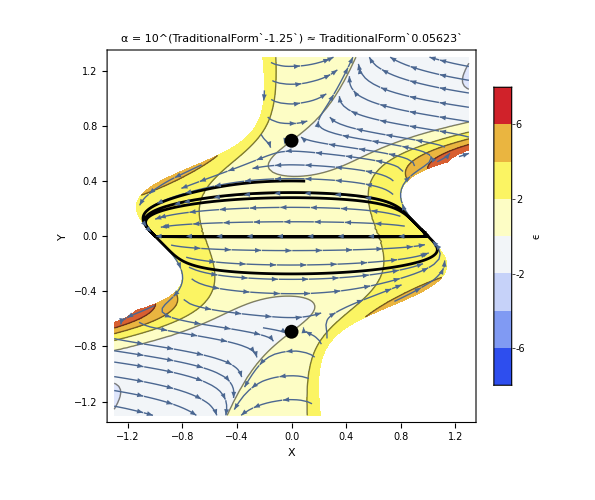

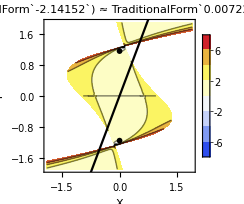
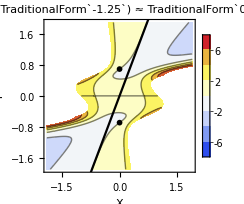
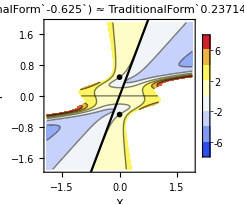
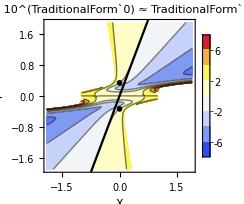

```mathematica
Subscript[χ, 34]=Subscript[χ, 3]+Subscript[χ, 4]; {ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]}={1,10^r,0,0,0,0,0,0,0,0,0,0};
mincol=-8; maxcol=8; sep=8; size=500; color="TemperatureMap"; L=1.3; Print[]; 
{Subscript[Q, κ],Subscript[Q, λ],Subscript[Q, 4],Subscript[C, 1],Subscript[C, 2],Subscript[C, 3],Subscript[C, 4],Subscript[Q, 1]}={κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[θ, 1]}/α;

points1=Graphics[{PointSize[0.02],Point[{{0,-Sqrt[(3 Subscript[θ, 1]+√(308 α+9 Subscript[θ, 1]^2-64 Subscript[θ, 4]-36 κ-8 Subscript[χ, 34]))/(2 (77 α-16 Subscript[θ, 4]-9 κ-2 Subscript[χ, 34]))]},{0,Sqrt[(3 Subscript[θ, 1]+√(308 α+9 Subscript[θ, 1]^2-64 Subscript[θ, 4]-36 κ-8 Subscript[χ, 34]))/(2 (77 α-16 Subscript[θ, 4]-9 κ-2 Subscript[χ, 34]))]}}]}];

r=-1.25; 
pp=ParametricPlot[Evaluate[{x[t],y[t]}/.NumSol[{500,0,0,0.1,0.4001001},α,Subscript[Q, κ],Subscript[Q, λ],Subscript[Q, 4],Subscript[C, 1],Subscript[C, 2],Subscript[C, 3],Subscript[C, 4],Subscript[Q, 1]]],{t,0,3},PlotTheme->"Scientific", PlotStyle->{Thickness[0.004],Black}]/.Line[x_]->Sequence[Arrowheads->Table[.02,{40}],Arrow[x]];
Show[{Legended[ ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->(ColorData[color,Rescale[#,{mincol,maxcol}]]&),
ColorFunctionScaling->False,PlotRange->{mincol,maxcol},ImageSize->size,RegionFunction->Function[{X,Y},Z4≥0]],BarLegend[{color,{mincol,maxcol}},Range[-6,6,2],LegendMarkerSize->size*0.72,LegendLabel->Style["ϵ   ",14]] ],
StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},RegionFunction->Function[{X,Y},Z4≥0]],pp,points1
},PlotLabel->Style[StringForm["α = 10^(``) ≈ ``",r,Round[α,0.00001]],15.5] ,RotateLabel->False, FrameLabel->{Style["X",Bold,12],Style["Y",Bold,12]}]
 Clear[r];

L=1.9;
Table[Show[{
Legended[ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->(ColorData[color,Rescale[#,{mincol,maxcol}]]&),ColorFunctionScaling->False,PlotRange->{mincol,maxcol},RegionFunction->Function[{X,Y},Z4≥0],ImageSize->205],BarLegend[{color,{mincol,maxcol}},Range[-6,6,2]]],Plot[βval X,{X,-L,L},PlotStyle->Black],points1},PlotLabel->Style[StringForm["α = 10^(``) ≈ ``",r,Round[α,0.00001]],13] ,RotateLabel->False, FrameLabel->{Style["X",Bold,12],Style["Y",Bold,12]}],{r,{-2.14152,-1.25,-0.625,0}}]


Unset[{Subscript[Q, κ],Subscript[Q, λ],Subscript[Q, 4],Subscript[C, 1],Subscript[C, 2],Subscript[C, 3],Subscript[C, 4],Subscript[Q, 1]}]; Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],r];
```

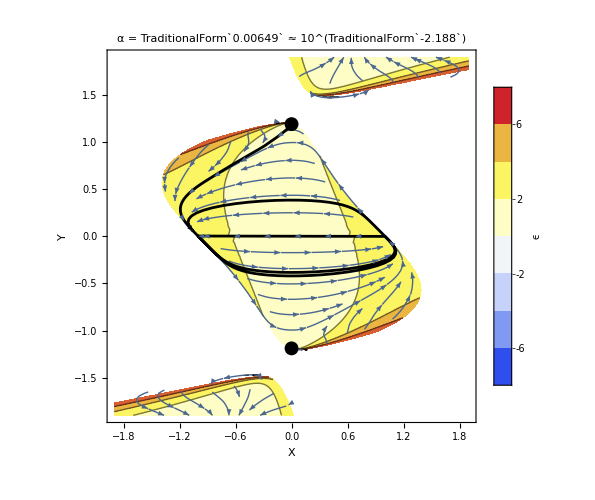

```mathematica
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]}={1,0.00649,0,0,0,0,0,0,0,0,0,0,0}; r=Round[Log10[α],0.001];
mincol=-8; maxcol=8; sep=8; size=500; color="TemperatureMap"; L=1.9; Print[];
{Subscript[Q, κ],Subscript[Q, λ],Subscript[Q, 4],Subscript[C, 1],Subscript[C, 2],Subscript[C, 3],Subscript[C, 4],Subscript[Q, 1]}={κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[θ, 1]}/α;


pp=ParametricPlot[Evaluate[{x[t],y[t]}/.NumSol[{500,0,0,0.0011,1.189},α,Subscript[Q, κ],Subscript[Q, λ],Subscript[Q, 4],Subscript[C, 1],Subscript[C, 2],Subscript[C, 3],Subscript[C, 4],Subscript[Q, 1]]],{t,0,86},PlotTheme->"Scientific", PlotStyle->{Thickness[0.004],Black}]/.Line[x_]->Sequence[Arrowheads->Table[.02,{40}],Arrow[x]];
Show[{Legended[ ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->(ColorData[color,Rescale[#,{mincol,maxcol}]]&),
ColorFunctionScaling->False,PlotRange->{mincol,maxcol},ImageSize->size,RegionFunction->Function[{X,Y},Z4≥0]],BarLegend[{color,{mincol,maxcol}},Range[-6,6,2],LegendMarkerSize->size*0.72,LegendLabel->Style["ϵ   ",14]] ],
StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},RegionFunction->Function[{X,Y},Z4≥0]],pp,points1
},PlotLabel->Style[StringForm["α = `` ≈ 10^(``)",Round[α,0.00001],r],15.5] ,RotateLabel->False, FrameLabel->{Style["X",Bold,12],Style["Y",Bold,12]}]

Unset[{Subscript[Q, κ],Subscript[Q, λ],Subscript[Q, 4],Subscript[C, 1],Subscript[C, 2],Subscript[C, 3],Subscript[C, 4],Subscript[Q, 1]}]; Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],r];
```

#### Rupture points

```mathematica
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[θ, 1]}={1,α,0,0,0,0,0,0,0,0};
Reduce[(Need[2]&&α>10^(-3))/.{κ->0,Subscript[θ, 4]->0,Subscript[χ, 34]->0},{R},Reals]//Factor

(αα=(-19799209+273208 √5254)/572250);( RR=Root[52+(73+50 α) #1+(-10-940 α) #1^2+(-31+4418 α) #1^3&,2]/.{α->αα});
(XX=Need[1][[2]]^(1/4)/.{α->αα,R->RR}); (YY=RR XX); 

StringForm["\nα_crit ≈ 10^(``)\nR ≈ ``≈ Tan^-1((``)^(.ba))\nX ≈ ``\nY ≈ ``\n",
Log10[αα]//N,Round[RR,0.001],Round[ArcTan[RR]/Degree,0.001],Round[XX,0.001],Round[YY,0.001]]

Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]];
```

(1/1000<α<31/4418&&R==Root[52+(73+50 α) #1+(-10-940 α) #1^2+(-31+4418 α) #1^3&,3])||(α==31/4418&&R==1/705 (1558+√3984709))||(31/4418<α<(-19799209+273208 √5254)/572250&&(R==Root[52+(73+50 α) #1+(-10-940 α) #1^2+(-31+4418 α) #1^3&,2]||R==Root[52+(73+50 α) #1+(-10-940 α) #1^2+(-31+4418 α) #1^3&,3]))||(α==(-19799209+273208 √5254)/572250&&R==Root[52+(73+50 α) #1+(-10-940 α) #1^2+(-31+4418 α) #1^3&,2])

α_crit ≈ 10^-2.14152
R ≈ 9.699≈ Tan^-1(84.113^(.ba))
X ≈ 0.132
Y ≈ 1.282

### Only κ [ β < 0 ]

#### General expressions

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]];
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,0,κ,0,0,0,0,0,0,0,0};
SolveForThis={κ}; AssumeThis=(κ≠0);

Print["\n",fried==0/.F->Fval,"\n",eq1==0/.F->Fval,"\n",eq2==0/.F->Fval,"\n\n","Z^4 = ",Z4=(Zval^4//Factor//FullSimplify),"\n","P = ",(Pval//Factor//FullSimplify),"\n","ϵ = ",ϵxy=(ϵval//Factor//FullSimplify),"\nλ_+ + λ_- = ",lambdaSum,"\nλ_+ * λ_- = ",lambdaPrd,"\n\nc_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum,"\nc_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",csprd,"\n\nβ = ",(βval//FullSimplify)," , γ^4 = ",(γvalAbs^4//Simplify),"\n"]
```

-1+X^2+2 X Y+Y^2+2 Z^4+(2 X^2 Y^2-20 X Y^3-12 Y^4) κ+Ω_m+Ω_r==0
3+X^2+2 X Y+Y^2+2 Z^4-2 ϵ+(70 X^2 Y^2+12 √2 P Y^3+108 X Y^3+24 Y^4-4 Y^4 ϵ) κ+Ω_r==0
P/(√2)+3 X+2 Y+(4 Z^4)/Y-Y ϵ+(2 X^2 Y+√2 P Y^2+6 X Y^2-6 Y^3+10 Y^3 ϵ) κ==0

Z^4 = 1/2 (1-(X+Y)^2+2 Y^2 (-X^2+10 X Y+6 Y^2) κ-Ω_m-Ω_r)
P = (X^2 (4+4 Y^2 κ (1+19 Y^2-168 Y^4 κ))+2 X Y (1-2 Y^2 κ (23-33 Y^2+366 Y^4 κ))+4 (-1+Ω_m+Ω_r)+Y^2 (4-Ω_m+2 Y^2 κ (-42+18 Y^2-216 Y^4 κ+9 Ω_m+4 Ω_r)))/(√2 Y (1+2 Y^2 κ (1-5 Y^2+62 Y^4 κ)))
ϵ = (4-Ω_m+2 Y^2 κ (-20+2 (29 X^2+38 X Y+9 Y^2+2 (X-5 Y) Y^2 (23 X+9 Y) κ)+23 Ω_m+24 Ω_r))/(2+4 Y^2 κ (1-5 Y^2+62 Y^4 κ))
λ_+ + λ_- = 5/4+κ (ψ̂)^2+(19 κ (ψ̂)^4)/8
λ_+ * λ_- = 1/8 (2+2 κ (ψ̂)^2+19 κ (ψ̂)^4+κ^2 (ψ̂)^6)

c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (4+4 κ (ψ̂)^2+18 κ (ψ̂)^4+30 κ^2 (ψ̂)^6)/(2+2 κ (ψ̂)^2+19 κ (ψ̂)^4+κ^2 (ψ̂)^6)
c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (2+2 κ (ψ̂)^2-κ (ψ̂)^4-3 κ^2 (ψ̂)^6)/(2+2 κ (ψ̂)^2+19 κ (ψ̂)^4+κ^2 (ψ̂)^6)

β = -23/9 , γ^4 = (180389 κ)/2187

#### Constraints - external region

```mathematica
t0=AbsoluteTime[]; aux1={}; aux2={}; NumSum={};NumPrd={}; Den={}; 
cons01=Reduce[βval<0&&γval^4>0,Reals,Backsubstitution->True]; 
cons02=Reduce[βval>0&&γval^4>0,Reals,Backsubstitution->True];
consJ0=Reduce[(cons01||cons02)&&AssumeThis,SolveForThis,Reals];Print[
"\n0. Expressions involving β,γ","\n\n   β = ",(βval//FullSimplify)," , γ^4 = ",(γvalAbs^4//Simplify),
"\n\n0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]\n\n   ",cons01,
"\n\n\n0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]\n\n   ",cons02,
"\n\n J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) \n\n   ",consJ0,"\n"];

tt=CoefficientList[lambdaSum,OverHat[ψ],{5}]//FullSimplify;
dd=CoefficientList[lambdaPrd,OverHat[ψ],{7}]//FullSimplify;
For[i=1,i≤Length[consT],i++,AppendTo[aux1,((consT[[i]]/.Subscript[t,k_]:>tt[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[aux2,((consD[[i]]/.Subscript[d,k_]:>dd[[k+1]]))//Simplify]];
cons11=Reduce[Apply[Or,aux1],Reals,Backsubstitution->True];
cons12=Reduce[Apply[Or,aux2],Reals,Backsubstitution->True];
consJ1=Reduce[cons11&&cons12&&AssumeThis,SolveForThis,Reals];Print[
"\n\n1. Expressions involving Eigenvalues[ 𝕂 ]","\n\n   λ_+ + λ_- = ",lambdaSum,"\n   λ_+ * λ_- = ",lambdaPrd,
"\n\n\n1.1. Conditions for  [ λ_+ + λ_- > 0 ]\n\n   ",cons11,
"\n\n\n1.2. Conditions for  [ λ_+ * λ_- > 0 ]\n\n   ",cons12,
"\n\n\n J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) \n\n   ",consJ1,"\n"]

ns=CoefficientList[Numerator[cssum],OverHat[ψ],7]//FullSimplify;
np=CoefficientList[Numerator[csprd],OverHat[ψ],7]//FullSimplify;
dsp=CoefficientList[Denominator[cssum],OverHat[ψ],7]//FullSimplify;
For[i=1,i≤Length[consD],i++,AppendTo[NumSum,((consD[[i]]/.Subscript[d,k_]:>ns[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[NumPrd,((consD[[i]]/.Subscript[d,k_]:>np[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[Den,((consD[[i]]/.Subscript[d,k_]:>dsp[[k+1]]))//Simplify]];
cons21=Reduce[Apply[Or,NumSum]&&AssumeThis,SolveForThis,Reals];
cons22=Reduce[Apply[Or,NumPrd]&&AssumeThis,SolveForThis,Reals];
cons23=Reduce[Apply[Or,Den]&&AssumeThis,SolveForThis,Reals];
consJ2=Reduce[cons21&&cons22&&cons23&&AssumeThis,SolveForThis,Reals];Print[
"\n2. Expressions involving  c_s^2 ","\n\n   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum,"\n   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = ",csprd,
"\n\n2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons21,
"\n\n\n2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons22,
"\n\n\n2.3. Conditions for Denominator > 0\n\n   ",cons23,
"\n\n\n J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) \n\n   ",consJ2,"\n"]

cons31=Reduce[Resolve[ForAll[OverHat[ψ],cs21≤1],Reals]&&AssumeThis,SolveForThis,Reals];
cons32=Reduce[Resolve[ForAll[OverHat[ψ],cs22≤1],Reals]&&AssumeThis,SolveForThis,Reals];
consJ3=Reduce[cons31&&cons32&&AssumeThis,SolveForThis,Reals];
Print["\n3.1 Conditions for c_(s, SubscriptBox[h, ±])^2 ≤ 1\n\n   ",cons31,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,cons31],
"\n\n3.2 Conditions for  c_(s, SubscriptBox[γ, ±])^2 ≤ 1\n\n   ",cons32,"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,cons32],
"\n\n J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) \n\n   ",consJ3,"\n"]

consJ4=Reduce[Resolve[ForAll[OverHat[ψ],cs21==1],Reals]&&AssumeThis,SolveForThis,Reals];Print[
"\n 4. Joint constraints for [ GRAVITATIONAL WAVES ]  \n\n   ",
consJ4,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,consJ4],"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,consJ4],"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&AssumeThis,SolveForThis,Reals],"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3∧J4) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&consJ4&&AssumeThis,SolveForThis,Reals],"\n"]

Print["\n\nThis process took about ",Round[(AbsoluteTime[]-t0)/60,0.001]," minutes.\n"];
```

0. Expressions involving β,γ

   β = -23/9 , γ^4 = (180389 κ)/2187

0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]

   κ>0


0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]

   False

 J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) 

   κ>0

1. Expressions involving Eigenvalues[ 𝕂 ]

   λ_+ + λ_- = 5/4+κ (ψ̂)^2+(19 κ (ψ̂)^4)/8
   λ_+ * λ_- = 1/8 (2+2 κ (ψ̂)^2+19 κ (ψ̂)^4+κ^2 (ψ̂)^6)


1.1. Conditions for  [ λ_+ + λ_- > 0 ]

   κ≥0


1.2. Conditions for  [ λ_+ * λ_- > 0 ]

   κ≥0


 J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) 

   κ>0

2. Expressions involving  c_s^2 

   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (4+4 κ (ψ̂)^2+18 κ (ψ̂)^4+30 κ^2 (ψ̂)^6)/(2+2 κ (ψ̂)^2+19 κ (ψ̂)^4+κ^2 (ψ̂)^6)
   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = (2+2 κ (ψ̂)^2-κ (ψ̂)^4-3 κ^2 (ψ̂)^6)/(2+2 κ (ψ̂)^2+19 κ (ψ̂)^4+κ^2 (ψ̂)^6)

2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0

   1/20 (-297-63 √21)<κ<1/20 (-297+63 √21)||κ>0


2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0

   False


2.3. Conditions for Denominator > 0

   κ>0


 J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) 

   False

3.1 Conditions for c_(s, SubscriptBox[h, ±])^2 ≤ 1

   κ>0

   c_(s, SubscriptBox[h, ±])^2 = (2+2 κ (ψ̂)^2+9 κ (ψ̂)^4+15 κ^2 (ψ̂)^6-2 κ Abs[ψ̂]^3 √(16+(25+16 κ) (ψ̂)^2+82 κ (ψ̂)^4+57 κ^2 (ψ̂)^6))/(2+2 κ (ψ̂)^2+19 κ (ψ̂)^4+κ^2 (ψ̂)^6)

3.2 Conditions for  c_(s, SubscriptBox[γ, ±])^2 ≤ 1

   False

   c_(s, SubscriptBox[γ, ±])^2 = (2+2 κ (ψ̂)^2+9 κ (ψ̂)^4+15 κ^2 (ψ̂)^6+2 κ (ψ̂)^3 √(16+(25+16 κ) (ψ̂)^2+82 κ (ψ̂)^4+57 κ^2 (ψ̂)^6))/(2+2 κ (ψ̂)^2+19 κ (ψ̂)^4+κ^2 (ψ̂)^6)

 J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) 

   False

4. Joint constraints for [ GRAVITATIONAL WAVES ]  

   False

   c_(s, SubscriptBox[h, ±])^2 = (2+2 κ (ψ̂)^2+9 κ (ψ̂)^4+15 κ^2 (ψ̂)^6-2 κ (ψ̂)^3 √(16+(25+16 κ) (ψ̂)^2+82 κ (ψ̂)^4+57 κ^2 (ψ̂)^6))/(2+2 κ (ψ̂)^2+19 κ (ψ̂)^4+κ^2 (ψ̂)^6)

   c_(s, SubscriptBox[γ, ±])^2 = (2+2 κ (ψ̂)^2+9 κ (ψ̂)^4+15 κ^2 (ψ̂)^6+2 κ (ψ̂)^3 √(16+(25+16 κ) (ψ̂)^2+82 κ (ψ̂)^4+57 κ^2 (ψ̂)^6))/(2+2 κ (ψ̂)^2+19 κ (ψ̂)^4+κ^2 (ψ̂)^6)

Summary of CONSTRAINTS (J1∧J2∧J3) 

   False

Summary of CONSTRAINTS (J1∧J2∧J3∧J4) 

   False

This process took about 0.019 minutes.

#### Phase portrait

```mathematica
t0=AbsoluteTime[]; Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]];ξ=1;
NumΩmp=((Ωmp//NoMoreFPϵ)/.{X->x[t],Y->y[t],Subscript[Ω, m]->0,Subscript[Ω, r]->0,Subscript[χ, 34]->Subscript[χ, 3]+Subscript[χ, 4]}//Simplify);
NumΩrp=((Ωrp//NoMoreFPϵ)/.{X->x[t],Y->y[t],Subscript[Ω, m]->0,Subscript[Ω, r]->0,Subscript[χ, 34]->Subscript[χ, 3]+Subscript[χ, 4]}//Simplify);
NumXp=((Xp//NoMoreFPϵ)/.{X->x[t],Y->y[t],Subscript[Ω, m]->0,Subscript[Ω, r]->0,Subscript[χ, 34]->Subscript[χ, 3]+Subscript[χ, 4]}//Simplify);
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]]; 

NumSol[{tmax_,Ωm0_,Ωr0_,x0_,y0_}]:=NDSolve[{ 
Ωm'[t]==NumΩmp, Ωr'[t]==NumΩrp, x'[t]==NumXp, y'[t]==x[t], Ωm[0]==Ωm0, Ωr[0]==Ωr0, x[0]==x0, y[0]==y0},{Ωm,Ωr,x,y}, {t,0,tmax},
Method->{StiffnessSwitching,Method->{ExplicitRungeKutta,Automatic}},MaxSteps->10^10,PrecisionGoal->16] (* 16 *)
Print["\nProcess ended within ",Round[(AbsoluteTime[]-t0)/60,0.01]," minutes. → The specified PDE solver has been defined.\n"];
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]];
```

Process ended within 0.06 minutes. → The specified PDE solver has been defined.

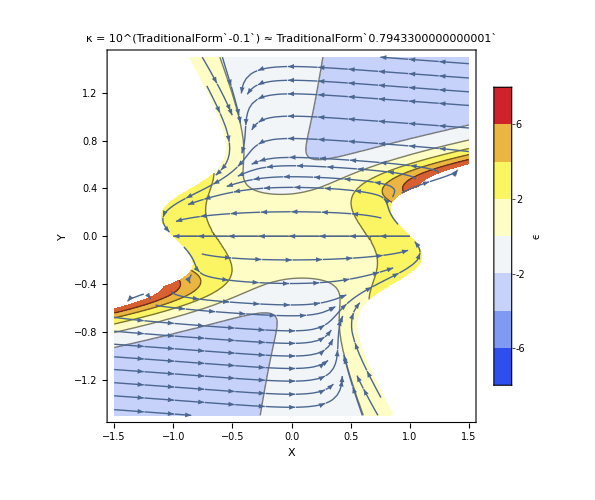

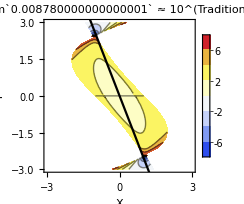
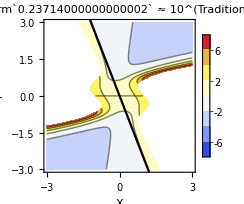
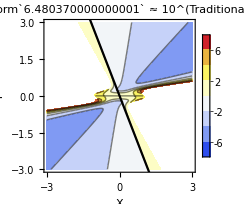

```mathematica
{Subscript[Ω, m],Subscript[Ω, r]}={0,0}; mincol=-8; maxcol=8; sep=8; size=500; color="TemperatureMap"; L=1.5; Print[];
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,0,10^r,0,0,0,0,0,0,0,0};

r=-0.1;
pp=ParametricPlot[Evaluate[{x[t],y[t]}/.NumSol[{100,0,0,0.60432,1.2345}]],{t,0,4.3},PlotTheme->"Scientific", PlotStyle->{Thickness[0.004],Black}]/.Line[x_]->Sequence[Arrowheads->Table[.02,{40}],Arrow[x]];
Show[{Legended[ ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->(ColorData[color,Rescale[#,{mincol,maxcol}]]&),
ColorFunctionScaling->False,PlotRange->{mincol,maxcol},ImageSize->size,RegionFunction->Function[{X,Y},Z4≥0]],BarLegend[{color,{mincol,maxcol}},Range[-6,6,2],LegendMarkerSize->size*0.72,LegendLabel->Style["ϵ   ",14]] ],
StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},RegionFunction->Function[{X,Y},Z4≥0]],pp
},PlotLabel->Style[StringForm["κ = 10^(``) ≈ ``",r,Round[κ,0.00001]],15.5] ,RotateLabel->False, FrameLabel->{Style["X",Bold,12],Style["Y",Bold,12]}]
Clear[r];

L=3;
Table[Show[{
Legended[ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->(ColorData[color,Rescale[#,{mincol,maxcol}]]&),ColorFunctionScaling->False,PlotRange->{mincol,maxcol},RegionFunction->Function[{X,Y},Z4≥0],ImageSize->205],BarLegend[{color,{mincol,maxcol}},Range[-6,6,2]]],Plot[βval X,{X,-L,L},PlotStyle->Black]},PlotLabel->Style[StringForm["       κ = ``  ≈ 10^(``)",Round[κ,0.00001],r],13] ,RotateLabel->False, FrameLabel->{Style["X",Bold,12],Style["Y",Bold,12]}],{r,{-2.0564,-0.625,0.8116}}]
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],r];
```

#### Rupture points

```mathematica
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,0,κ,0,0,0,0,0,0,0,0}; (* Estimated rupture points *)
Reduce[(Zval^4/.{Y->R X}//FullSimplify)==0&&Abs[R]>2&&X>0,Reals]//Factor
κκ=%[[-1,2]]/.{X->1.2511,R->Tan[2.5/1.2511]};
RR=Tan[2.5/1.2511]; 
XX=1.2511;
YY=RR XX;

 StringForm["κ_crit ≈ 10^(``)\nR ≈ ``≈ Tan^-1((``)^(.ba))\nX ≈ ``\nY ≈ ``\n",
Log10[κκ]//N,Round[RR,0.001],Round[ArcTan[RR]/Degree,0.001],Round[XX,0.001],Round[YY,0.001]]
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]];
```

X>0&&(R<-2||R>2)&&κ==((-1+X+R X) (1+X+R X))/(2 R^2 (-1+10 R+6 R^2) X^4)

κ_crit ≈ 10^-2.0565
R ≈ -2.195≈ Tan^-1((-65.509)^(.ba))
X ≈ 1.251
Y ≈ -2.746

### Only θ_4 [ β < 0 ]

#### General expressions

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]]; 
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,0,0,0,Subscript[θ, 4],0,0,0,0,0,0};
SolveForThis={Subscript[θ, 4]}; AssumeThis=(Subscript[θ, 4]≠0);

Print["\n",fried==0/.F->Fval,"\n",eq1==0/.F->Fval,"\n",eq2==0/.F->Fval,"\n\n","Z^4 = ",Z4=(Zval^4//Factor//FullSimplify),"\n","P = ",(Pval//Factor//FullSimplify),"\n","ϵ = ",ϵxy=(ϵval//Factor//FullSimplify),"\nλ_+ + λ_- = ",lambdaSum,"\nλ_+ * λ_- = ",lambdaPrd,"\n\nc_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum,"\nc_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",csprd,"\n\nβ = ",(βval//FullSimplify)," , γ^4 = ",(γvalAbs^4//Simplify),"\n"]
```

-1+X^2+2 X Y+Y^2+2 Z^4+(-64 X Y^3-32 Y^4) θ_4+Ω_m+Ω_r==0
3+X^2+2 X Y+Y^2+2 Z^4-2 ϵ+(192 X^2 Y^2+32 √2 P Y^3+256 X Y^3+32 Y^4) θ_4+Ω_r==0
P/(√2)+3 X+2 Y+(4 Z^4)/Y-Y ϵ+(-32 Y^3+32 Y^3 ϵ) θ_4==0

Z^4 = 1/2 (1-(X+Y)^2+32 Y^3 (2 X+Y) θ_4-Ω_m-Ω_r)
P = (X^2 (4+192 Y^4 θ_4 (1-32 Y^2 θ_4))+2 X Y (1-32 Y^2 θ_4 (4-5 Y^2+160 Y^4 θ_4))-Y^2 (-4+32 Y^2 θ_4 (6-2 Y^2+64 Y^4 θ_4-Ω_m)+Ω_m)+4 (-1+Ω_m+Ω_r))/(√2 Y (1+32 Y^4 θ_4 (-1+32 Y^2 θ_4)))
ϵ = (4-Ω_m+64 Y^2 θ_4 (5 X^2+6 X Y+Y^2-32 Y^3 (4 X+Y) θ_4+2 (-1+Ω_m+Ω_r)))/(2+64 Y^4 θ_4 (-1+32 Y^2 θ_4))
λ_+ + λ_- = 5/4-2 θ_4 (ψ̂)^4
λ_+ * λ_- = 1/8 (2-16 θ_4 (ψ̂)^4-128 θ_4^2 (ψ̂)^6)

c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (4-16 θ_4 (ψ̂)^4)/(2-16 θ_4 (ψ̂)^4-128 θ_4^2 (ψ̂)^6)
c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = 2/(2-16 θ_4 (ψ̂)^4-128 θ_4^2 (ψ̂)^6)

β = -4 , γ^4 = 2048 θ_4

#### Constraints - external region

```mathematica
t0=AbsoluteTime[]; aux1={}; aux2={}; NumSum={};NumPrd={}; Den={}; 
cons01=Reduce[βval<0&&γval^4>0,Reals,Backsubstitution->True]; 
cons02=Reduce[βval>0&&γval^4>0,Reals,Backsubstitution->True];
consJ0=Reduce[(cons01||cons02)&&AssumeThis,SolveForThis,Reals];Print[
"\n0. Expressions involving β,γ","\n\n   β = ",(βval//FullSimplify)," , γ^4 = ",(γvalAbs^4//Simplify),
"\n\n0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]\n\n   ",cons01,
"\n\n\n0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]\n\n   ",cons02,
"\n\n J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) \n\n   ",consJ0,"\n"];

tt=CoefficientList[lambdaSum,OverHat[ψ],{5}]//FullSimplify;
dd=CoefficientList[lambdaPrd,OverHat[ψ],{7}]//FullSimplify;
For[i=1,i≤Length[consT],i++,AppendTo[aux1,((consT[[i]]/.Subscript[t,k_]:>tt[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[aux2,((consD[[i]]/.Subscript[d,k_]:>dd[[k+1]]))//Simplify]];
cons11=Reduce[Apply[Or,aux1],Reals,Backsubstitution->True];
cons12=Reduce[Apply[Or,aux2],Reals,Backsubstitution->True];
consJ1=Reduce[cons11&&cons12&&AssumeThis,SolveForThis,Reals];Print[
"\n\n1. Expressions involving Eigenvalues[ 𝕂 ]","\n\n   λ_+ + λ_- = ",lambdaSum,"\n   λ_+ * λ_- = ",lambdaPrd,
"\n\n\n1.1. Conditions for  [ λ_+ + λ_- > 0 ]\n\n   ",cons11,
"\n\n\n1.2. Conditions for  [ λ_+ * λ_- > 0 ]\n\n   ",cons12,
"\n\n\n J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) \n\n   ",consJ1,"\n"]

ns=CoefficientList[Numerator[cssum],OverHat[ψ],7]//FullSimplify;
np=CoefficientList[Numerator[csprd],OverHat[ψ],7]//FullSimplify;
dsp=CoefficientList[Denominator[cssum],OverHat[ψ],7]//FullSimplify;
For[i=1,i≤Length[consD],i++,AppendTo[NumSum,((consD[[i]]/.Subscript[d,k_]:>ns[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[NumPrd,((consD[[i]]/.Subscript[d,k_]:>np[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[Den,((consD[[i]]/.Subscript[d,k_]:>dsp[[k+1]]))//Simplify]];
cons21=Reduce[Apply[Or,NumSum]&&AssumeThis,SolveForThis,Reals];
cons22=Reduce[Apply[Or,NumPrd]&&AssumeThis,SolveForThis,Reals];
cons23=Reduce[Apply[Or,Den]&&AssumeThis,SolveForThis,Reals];
consJ2=Reduce[cons21&&cons22&&cons23&&AssumeThis,SolveForThis,Reals];Print[
"\n2. Expressions involving  c_s^2 ","\n\n   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum,"\n   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = ",csprd,
"\n\n2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons21,
"\n\n\n2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons22,
"\n\n\n2.3. Conditions for Denominator > 0\n\n   ",cons23,
"\n\n\n J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) \n\n   ",consJ2,"\n"]

cons31=Reduce[Resolve[ForAll[OverHat[ψ],cs21≤1],Reals]&&AssumeThis,SolveForThis,Reals];
cons32=Reduce[Resolve[ForAll[OverHat[ψ],cs22≤1],Reals]&&AssumeThis,SolveForThis,Reals];
consJ3=Reduce[cons31&&cons32&&AssumeThis,SolveForThis,Reals];
Print["\n3.1 Conditions for c_(s, SubscriptBox[h, ±])^2 ≤ 1\n\n   ",cons31,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,cons31],
"\n\n3.2 Conditions for  c_(s, SubscriptBox[γ, ±])^2 ≤ 1\n\n   ",cons32,"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,cons32],
"\n\n J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) \n\n   ",consJ3,"\n"]

consJ4=Reduce[Resolve[ForAll[OverHat[ψ],cs21==1],Reals]&&AssumeThis,SolveForThis,Reals];Print[
"\n 4. Joint constraints for [ GRAVITATIONAL WAVES ]  \n\n   ",
consJ4,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,consJ4],"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,consJ4],"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&AssumeThis,SolveForThis,Reals],"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3∧J4) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&consJ4&&AssumeThis,SolveForThis,Reals],"\n"]

Print["\n\nThis process took about ",Round[(AbsoluteTime[]-t0)/60,0.001]," minutes.\n"];
```

0. Expressions involving β,γ

   β = -4 , γ^4 = 2048 θ_4

0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]

   θ_4>0


0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]

   False

 J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) 

   θ_4>0

1. Expressions involving Eigenvalues[ 𝕂 ]

   λ_+ + λ_- = 5/4-2 θ_4 (ψ̂)^4
   λ_+ * λ_- = 1/8 (2-16 θ_4 (ψ̂)^4-128 θ_4^2 (ψ̂)^6)


1.1. Conditions for  [ λ_+ + λ_- > 0 ]

   θ_4≤0


1.2. Conditions for  [ λ_+ * λ_- > 0 ]

   θ_4==0


 J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) 

   False

2. Expressions involving  c_s^2 

   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (4-16 θ_4 (ψ̂)^4)/(2-16 θ_4 (ψ̂)^4-128 θ_4^2 (ψ̂)^6)
   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = 2/(2-16 θ_4 (ψ̂)^4-128 θ_4^2 (ψ̂)^6)

2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0

   θ_4<0


2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0

   θ_4<0||θ_4>0


2.3. Conditions for Denominator > 0

   False


 J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) 

   False

3.1 Conditions for c_(s, SubscriptBox[h, ±])^2 ≤ 1

   False

   c_(s, SubscriptBox[h, ±])^2 = (-1+4 θ_4 (ψ̂)^4+4 θ_4 (ψ̂)^3 √(4+(ψ̂)^2))/(-1+8 θ_4 (ψ̂)^4+64 θ_4^2 (ψ̂)^6)

3.2 Conditions for  c_(s, SubscriptBox[γ, ±])^2 ≤ 1

   False

   c_(s, SubscriptBox[γ, ±])^2 = (-1+4 θ_4 (ψ̂)^4+4 θ_4 (ψ̂)^3 √(4+(ψ̂)^2))/(-1+8 θ_4 (ψ̂)^4+64 θ_4^2 (ψ̂)^6)

 J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) 

   False

4. Joint constraints for [ GRAVITATIONAL WAVES ]  

   False

   c_(s, SubscriptBox[h, ±])^2 = (-1+4 θ_4 (ψ̂)^4+4 θ_4 (ψ̂)^3 √(4+(ψ̂)^2))/(-1+8 θ_4 (ψ̂)^4+64 θ_4^2 (ψ̂)^6)

   c_(s, SubscriptBox[γ, ±])^2 = (-1+4 θ_4 (ψ̂)^4+4 θ_4 (ψ̂)^3 √(4+(ψ̂)^2))/(-1+8 θ_4 (ψ̂)^4+64 θ_4^2 (ψ̂)^6)

Summary of CONSTRAINTS (J1∧J2∧J3) 

   False

Summary of CONSTRAINTS (J1∧J2∧J3∧J4) 

   False

This process took about 0.008 minutes.

#### Phase portrait

```mathematica
t0=AbsoluteTime[]; Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]];ξ=1;
NumΩmp=((Ωmp//NoMoreFPϵ)/.{X->x[t],Y->y[t],Subscript[Ω, m]->0,Subscript[Ω, r]->0,Subscript[χ, 34]->Subscript[χ, 3]+Subscript[χ, 4]}//Simplify);
NumΩrp=((Ωrp//NoMoreFPϵ)/.{X->x[t],Y->y[t],Subscript[Ω, m]->0,Subscript[Ω, r]->0,Subscript[χ, 34]->Subscript[χ, 3]+Subscript[χ, 4]}//Simplify);
NumXp=((Xp//NoMoreFPϵ)/.{X->x[t],Y->y[t],Subscript[Ω, m]->0,Subscript[Ω, r]->0,Subscript[χ, 34]->Subscript[χ, 3]+Subscript[χ, 4]}//Simplify);
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]]; 

NumSol[{tmax_,Ωm0_,Ωr0_,x0_,y0_}]:=NDSolve[{ 
Ωm'[t]==NumΩmp, Ωr'[t]==NumΩrp, x'[t]==NumXp, y'[t]==x[t], Ωm[0]==Ωm0, Ωr[0]==Ωr0, x[0]==x0, y[0]==y0},{Ωm,Ωr,x,y}, {t,0,tmax},
Method->{StiffnessSwitching,Method->{ExplicitRungeKutta,Automatic}},MaxSteps->10^10,PrecisionGoal->22] (* 16 *)
Print["\nProcess ended within ",Round[(AbsoluteTime[]-t0)/60,0.01]," minutes. → The specified PDE solver has been defined.\n"];
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]];
```

Process ended within 0.04 minutes. → The specified PDE solver has been defined.

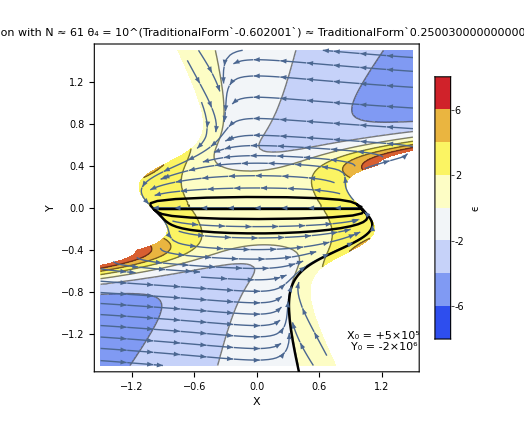
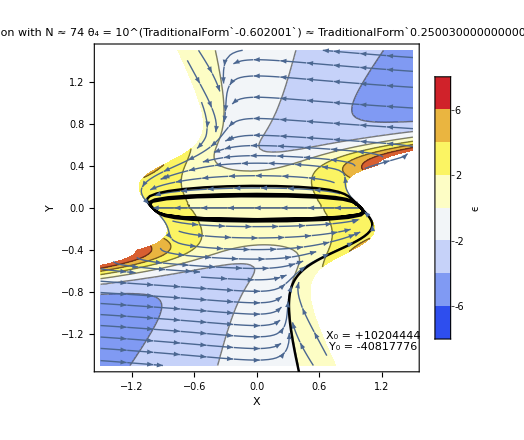
-Graphics- | -Graphics-

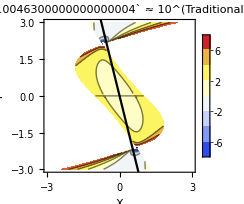
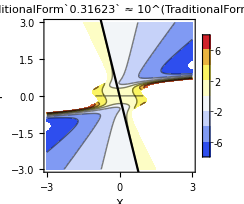
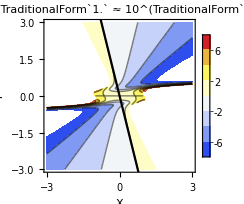

```mathematica
{Subscript[Ω, m],Subscript[Ω, r]}={0,0}; mincol=-8; maxcol=8; sep=8; size=440; color="TemperatureMap"; L=1.5; Print[];
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,0,0,0,10^r,0,0,0,0,0,0};

r=-0.602001;
pp61=ParametricPlot[Evaluate[{x[t],y[t]}/.NumSol[{500,0,0,500000,-4*500000}]],{t,0,61},PlotTheme->"Scientific", PlotStyle->{Thickness[0.004],Black}]/.Line[x_]->Sequence[Arrowheads->Table[.02,{4}],Arrow[x]];
pp74=ParametricPlot[Evaluate[{x[t],y[t]}/.NumSol[{500,0,0,10204444,-4*10204444}]],{t,0,74},PlotTheme->"Scientific", PlotStyle->{Thickness[0.004],Black}]/.Line[x_]->Sequence[Arrowheads->Table[.02,{4}],Arrow[x]];

Grid[{{
Show[{Legended[ ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->(ColorData[color,Rescale[#,{mincol,maxcol}]]&),
ColorFunctionScaling->False,PlotRange->{mincol,maxcol},ImageSize->size,RegionFunction->Function[{X,Y},Z4≥0]],BarLegend[{color,{mincol,maxcol}},Range[-6,6,2],LegendMarkerSize->size*0.72,LegendLabel->Style["ϵ   ",14]] ],
StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},RegionFunction->Function[{X,Y},Z4≥0]],pp61
},PlotLabel->Style[StringForm["Solution with N ≈ 61\nθ_4 = 10^(``) ≈ ``",r,Round[Subscript[θ, 4],0.00001]],15.5] ,RotateLabel->False, FrameLabel->{Style["X",Bold,12],Style["Y",Bold,12]},Epilog->Style[Text["X_0 = +5×10^5\nY_0 = -2×10^6",{1.22,-1.27}],13] ],
Show[{Legended[ ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->(ColorData[color,Rescale[#,{mincol,maxcol}]]&),
ColorFunctionScaling->False,PlotRange->{mincol,maxcol},ImageSize->size,RegionFunction->Function[{X,Y},Z4≥0]],BarLegend[{color,{mincol,maxcol}},Range[-6,6,2],LegendMarkerSize->size*0.72,LegendLabel->Style["ϵ   ",14]] ],
StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},RegionFunction->Function[{X,Y},Z4≥0]],pp74
},PlotLabel->Style[StringForm["Solution with N ≈ 74\nθ_4 = 10^(``) ≈ ``",r,Round[Subscript[θ, 4],0.00001]],15.5] ,RotateLabel->False, FrameLabel->{Style["X",Bold,12],Style["Y",Bold,12]},Epilog->Style[Text["X_0 = +10204444\nY_0 = -40817776",{1.12,-1.27}],13]]  }}]

Clear[r]; L=3; name[Log10[1/216]]="θ_4 = 1/216 ≈ `` ≈ 10^(``)"; name[0]="       θ_4 = ``  ≈ 10^(``)"; name[-0.5]=name[0];
Table[Show[{
Legended[ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->(ColorData[color,Rescale[#,{mincol,maxcol}]]&),ColorFunctionScaling->False,PlotRange->{mincol,maxcol},RegionFunction->Function[{X,Y},Z4≥0],ImageSize->205],BarLegend[{color,{mincol,maxcol}},Range[-6,6,2]]],Plot[βval X,{X,-L,L},PlotStyle->Black]},PlotLabel->Style[StringForm[name[r],Round[Subscript[θ, 4],0.00001],Round[r,0.0001]],13] ,RotateLabel->False, FrameLabel->{Style["X",Bold,12],Style["Y",Bold,12]}],{r,{Log10[1/216],-0.5,0}}]

Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],r];
```

#### Rupture points

```mathematica
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,0,0,0,Subscript[θ, 4],0,0,0,0,0,0};(* Estimated rupture points *)
Reduce[(Zval^4/.{Y->R X}//FullSimplify)==0&&Abs[R]>2&&X>0,Reals]//FullSimplify
Reduce[((Denominator[ϵval]/.{Y->R X})//FullSimplify)==0&&R>2&&0<X<1,{Subscript[θ, 4],R},Reals]//ToRadicals

θ44=1/216;YY=3/(√2); XX=(Solve[(-1+(1+R)^2 X^2)/(32 R^3 (2+R) X^4)==θ44/.{R->RR},X]//DeleteDuplicates)[[1,1,2]];RR=3/(√2 XX);
StringForm["θ_(4, crit) ≈ 10^(``)\nR ≈ ``≈ Tan^-1((``)^(.ba))\nX ≈ ``\nY ≈ ``",
Log10[θ44]//N,Round[RR,0.001],Round[ArcTan[RR]/Degree,0.001],Round[XX,0.001],Round[YY,0.001]]
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]];
```

X>0&&(R<-2||R>2)&&θ_4==(-1+(1+R)^2 X^2)/(32 R^3 (2+R) X^4)

0<X<1&&((0<θ_4<1/216&&(R==√(1/(96 X^2 θ_4)-X^2/(192 (X^12 θ_4^3-432 X^12 θ_4^4+12 √6 √(-X^24 θ_4^7+216 X^24 θ_4^8))^(1/3))-(ⅈ X^2)/(64 √3 (X^12 θ_4^3-432 X^12 θ_4^4+12 √6 √(-X^24 θ_4^7+216 X^24 θ_4^8))^(1/3))-((X^12 θ_4^3-432 X^12 θ_4^4+12 √6 √(-X^24 θ_4^7+216 X^24 θ_4^8))^(1/3))/(192 X^6 θ_4^2)+(ⅈ (X^12 θ_4^3-432 X^12 θ_4^4+12 √6 √(-X^24 θ_4^7+216 X^24 θ_4^8))^(1/3))/(64 √3 X^6 θ_4^2))||R==-√(1/(96 X^2 θ_4)-X^2/(192 (X^12 θ_4^3-432 X^12 θ_4^4+12 √6 √(-X^24 θ_4^7+216 X^24 θ_4^8))^(1/3))-(ⅈ X^2)/(64 √3 (X^12 θ_4^3-432 X^12 θ_4^4+12 √6 √(-X^24 θ_4^7+216 X^24 θ_4^8))^(1/3))-((X^12 θ_4^3-432 X^12 θ_4^4+12 √6 √(-X^24 θ_4^7+216 X^24 θ_4^8))^(1/3))/(192 X^6 θ_4^2)+(ⅈ (X^12 θ_4^3-432 X^12 θ_4^4+12 √6 √(-X^24 θ_4^7+216 X^24 θ_4^8))^(1/3))/(64 √3 X^6 θ_4^2))))||(θ_4==1/216&&R==3/(√2 X)))

θ_(4, crit) ≈ 10^-2.33445
R ≈ -1.93≈ Tan^-1((-62.613)^(.ba))
X ≈ -1.099
Y ≈ 2.121

### α, κ - [ Toy model ] - Its phase diagram exhibits a smooth transition betwwen β > 0 and β < 0 when Q_κ grows.

#### General expressions

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]]; 
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,α,Subscript[Q, κ] α,0,0,0,0,0,0,0,0};
SolveForThis={α,Subscript[Q, κ]}; AssumeThis=(α≠0)&&(Subscript[Q, κ]≠0);

Print["\n",fried==0/.F->Fval,"\n",eq1==0/.F->Fval,"\n",eq2==0/.F->Fval,"\n\n","Z^4 = ",Z4=(Zval^4//Factor//FullSimplify),"\n","P = ",(Pval//Factor//FullSimplify),"\n","ϵ = ",ϵxy=(ϵval//Factor//FullSimplify),"\nλ_+ + λ_- = ",lambdaSum,"\nλ_+ * λ_- = ",lambdaPrd,"\n\nc_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum,"\nc_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",csprd,"\n\nβ = ",(βval//FullSimplify)," , γ^4 = ",(γvalAbs^4//Simplify),"\n"]
```

-1+X^2+2 X Y+Y^2+2 Z^4+(10 X^2 Y^2-188 X Y^3-32 Y^4) α+Q_κ (2 X^2 Y^2-20 X Y^3-12 Y^4) α+Ω_m+Ω_r==0
3+X^2+2 X Y+Y^2+2 Z^4-2 ϵ+Q_κ α (70 X^2 Y^2+12 √2 P Y^3+108 X Y^3+24 Y^4-4 Y^4 ϵ)+α (614 X^2 Y^2+104 √2 P Y^3+316 X Y^3-340 Y^4+124 Y^4 ϵ)+Ω_r==0
P/(√2)+3 X+2 Y+(4 Z^4)/Y-Y ϵ+Q_κ α (2 X^2 Y+√2 P Y^2+6 X Y^2-6 Y^3+10 Y^3 ϵ)+α (10 X^2 Y+5 √2 P Y^2+30 X Y^2-218 Y^3+94 Y^3 ϵ)==0

Z^4 = 1/2 (1-(X+Y)^2+2 Y^2 (-(5+Q_κ) X^2+2 (47+5 Q_κ) X Y+2 (8+3 Q_κ) Y^2) α-Ω_m-Ω_r)
P = ((4 (-77+9 Q_κ) Y^6 α-16 (8+3 Q_κ) (-77+9 Q_κ) Y^8 α^2+4 X^2 (1+Y^2 (5+Q_κ+(89+19 Q_κ) Y^2) α-8 (1813+Q_κ (395+21 Q_κ)) Y^6 α^2)+2 X Y (1+2 Y^2 (-203-23 Q_κ+(95+33 Q_κ) Y^2) α-4 (-371+Q_κ (1624+183 Q_κ)) Y^6 α^2)-Y^2 (-4+Ω_m)+4 (-1+Ω_m+Ω_r)+2 Y^4 α (90-42 Q_κ-77 Ω_m+9 Q_κ Ω_m+4 (-31+Q_κ) Ω_r))/(√2 Y (1+2 Y^2 α (5+Q_κ-83 Y^2-5 Q_κ Y^2+2 (2289+Q_κ (516+31 Q_κ)) Y^4 α))))
ϵ = ((4+8 (89+19 Q_κ) X Y^3 α-16 (4963+Q_κ (1064+53 Q_κ)) X Y^5 α^2-8 (47+5 Q_κ) (-77+9 Q_κ) Y^6 α^2+4 Y^4 α (-77+9 Q_κ+2 (5+Q_κ) (203+23 Q_κ) X^2 α)-Ω_m+2 Y^2 α (-188+510 X^2+203 Ω_m+208 Ω_r+Q_κ (-20+58 X^2+23 Ω_m+24 Ω_r)))/(2+4 Y^2 (5+Q_κ-(83+5 Q_κ) Y^2) α+8 (2289+Q_κ (516+31 Q_κ)) Y^6 α^2))
λ_+ + λ_- = 5/4+(5 α+Q_κ α) (ψ̂)^2+1/8 (61 α+19 Q_κ α) (ψ̂)^4
λ_+ * λ_- = 1/8 (2+2 (5 α+Q_κ α) (ψ̂)^2+(61 α+19 Q_κ α) (ψ̂)^4+(105 α^2+36 Q_κ α^2+Q_κ^2 α^2) (ψ̂)^6)

c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (4+4 (5 α+Q_κ α) (ψ̂)^2+2 (71 α+9 Q_κ α) (ψ̂)^4+2 (155 α^2+76 Q_κ α^2+15 Q_κ^2 α^2) (ψ̂)^6)/(2+2 (5 α+Q_κ α) (ψ̂)^2+(61 α+19 Q_κ α) (ψ̂)^4+(105 α^2+36 Q_κ α^2+Q_κ^2 α^2) (ψ̂)^6)
c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (2+2 (5 α+Q_κ α) (ψ̂)^2+(81 α-Q_κ α) (ψ̂)^4+(205 α^2+116 Q_κ α^2-3 Q_κ^2 α^2) (ψ̂)^6)/(2+2 (5 α+Q_κ α) (ψ̂)^2+(61 α+19 Q_κ α) (ψ̂)^4+(105 α^2+36 Q_κ α^2+Q_κ^2 α^2) (ψ̂)^6)

β = (203+23 Q_κ)/(77-9 Q_κ) , γ^4 = ((203+23 Q_κ)^2 (917+33 Q_κ) (2289+516 Q_κ+31 Q_κ^2) α)/(77-9 Q_κ)^4

#### Constraints - external region

```mathematica
t0=AbsoluteTime[]; aux1={}; aux2={}; NumSum={};NumPrd={}; Den={}; 
cons01=Reduce[βval<0&&γval^4>0,Reals,Backsubstitution->True]; 
cons02=Reduce[βval>0&&γval^4>0,Reals,Backsubstitution->True];
consJ0=Reduce[(cons01||cons02)&&AssumeThis,SolveForThis,Reals];Print[
"\n0. Expressions involving β,γ","\n\n   β = ",(βval//FullSimplify)," , γ^4 = ",(γvalAbs^4//Simplify),
"\n\n0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]\n\n   ",cons01,
"\n\n\n0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]\n\n   ",cons02,
"\n\n J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) \n\n   ",consJ0,"\n"];

tt=CoefficientList[lambdaSum,OverHat[ψ],{5}]//FullSimplify;
dd=CoefficientList[lambdaPrd,OverHat[ψ],{7}]//FullSimplify;
For[i=1,i≤Length[consT],i++,AppendTo[aux1,((consT[[i]]/.Subscript[t,k_]:>tt[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[aux2,((consD[[i]]/.Subscript[d,k_]:>dd[[k+1]]))//Simplify]];
cons11=Reduce[Apply[Or,aux1],Reals,Backsubstitution->True];
cons12=Reduce[Apply[Or,aux2],Reals,Backsubstitution->True];
consJ1=Reduce[cons11&&cons12&&AssumeThis,SolveForThis,Reals];Print[
"\n\n1. Expressions involving Eigenvalues[ 𝕂 ]","\n\n   λ_+ + λ_- = ",lambdaSum,"\n   λ_+ * λ_- = ",lambdaPrd,
"\n\n\n1.1. Conditions for  [ λ_+ + λ_- > 0 ]\n\n   ",cons11,
"\n\n\n1.2. Conditions for  [ λ_+ * λ_- > 0 ]\n\n   ",cons12,
"\n\n\n J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) \n\n   ",consJ1,"\n"]

ns=CoefficientList[Numerator[cssum],OverHat[ψ],7]//FullSimplify;
np=CoefficientList[Numerator[csprd],OverHat[ψ],7]//FullSimplify;
dsp=CoefficientList[Denominator[cssum],OverHat[ψ],7]//FullSimplify;
For[i=1,i≤Length[consD],i++,AppendTo[NumSum,((consD[[i]]/.Subscript[d,k_]:>ns[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[NumPrd,((consD[[i]]/.Subscript[d,k_]:>np[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[Den,((consD[[i]]/.Subscript[d,k_]:>dsp[[k+1]]))//Simplify]];
cons21=Reduce[Apply[Or,NumSum]&&AssumeThis,SolveForThis,Reals];
cons22=Reduce[Apply[Or,NumPrd]&&AssumeThis,SolveForThis,Reals];
cons23=Reduce[Apply[Or,Den]&&AssumeThis,SolveForThis,Reals];
consJ2=Reduce[cons21&&cons22&&cons23&&AssumeThis,SolveForThis,Reals];Print[
"\n2. Expressions involving  c_s^2 ","\n\n   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum,"\n   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = ",csprd,
"\n\n2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons21,
"\n\n\n2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons22,
"\n\n\n2.3. Conditions for Denominator > 0\n\n   ",cons23,
"\n\n\n J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) \n\n   ",consJ2,"\n"]

cons31=Reduce[Resolve[ForAll[OverHat[ψ],cs21≤1],Reals]&&AssumeThis,SolveForThis,Reals];
cons32=Reduce[Resolve[ForAll[OverHat[ψ],cs22≤1],Reals]&&AssumeThis,SolveForThis,Reals];
consJ3=Reduce[cons31&&cons32&&AssumeThis,SolveForThis,Reals];
Print["\n3.1 Conditions for c_(s, SubscriptBox[h, ±])^2 ≤ 1\n\n   ",cons31,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,cons31],
"\n\n3.2 Conditions for  c_(s, SubscriptBox[γ, ±])^2 ≤ 1\n\n   ",cons32,"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,cons32],
"\n\n J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) \n\n   ",consJ3,"\n"]

consJ4=Reduce[Resolve[ForAll[OverHat[ψ],cs21==1],Reals]&&AssumeThis,SolveForThis,Reals];Print[
"\n 4. Joint constraints for [ GRAVITATIONAL WAVES ]  \n\n   ",
consJ4,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,consJ4],"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,consJ4],"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&AssumeThis,SolveForThis,Reals],"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3∧J4) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&consJ4&&AssumeThis,SolveForThis,Reals],"\n"]

Print["\n\nThis process took about ",Round[(AbsoluteTime[]-t0)/60,0.001]," minutes.\n"];
```

0. Expressions involving β,γ

   β = (203+23 Q_κ)/(77-9 Q_κ) , γ^4 = ((203+23 Q_κ)^2 (917+33 Q_κ) (2289+516 Q_κ+31 Q_κ^2) α)/(77-9 Q_κ)^4

0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]

   (α<0&&Q_κ<-917/33)||(α>0&&-917/33<Q_κ<-203/23)||(α>0&&Q_κ>77/9)


0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]

   α>0&&-203/23<Q_κ<77/9

 J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) 

   (α<0&&Q_κ<-917/33)||(α>0&&(-917/33<Q_κ<-203/23||-203/23<Q_κ<0||0<Q_κ<77/9||Q_κ>77/9))

1. Expressions involving Eigenvalues[ 𝕂 ]

   λ_+ + λ_- = 5/4+(5 α+Q_κ α) (ψ̂)^2+1/8 (61 α+19 Q_κ α) (ψ̂)^4
   λ_+ * λ_- = 1/8 (2+2 (5 α+Q_κ α) (ψ̂)^2+(61 α+19 Q_κ α) (ψ̂)^4+(105 α^2+36 Q_κ α^2+Q_κ^2 α^2) (ψ̂)^6)


1.1. Conditions for  [ λ_+ + λ_- > 0 ]

   (Q_κ≤-5&&α≤0)||(-5<Q_κ<-61/19&&(5 (61+19 Q_κ))/(8 (5+Q_κ)^2)<α≤0)||(Q_κ≥-61/19&&α≥0)


1.2. Conditions for  [ λ_+ * λ_- > 0 ]

   (Q_κ≤-18-√219&&α≤0)||(-18-√219<Q_κ<-18+√219&&α==0)||(Q_κ≥-18+√219&&α≥0)


 J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) 

   (α<0&&Q_κ≤-18-√219)||(α>0&&(-18+√219≤Q_κ<0||Q_κ>0))

2. Expressions involving  c_s^2 

   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (4+4 (5 α+Q_κ α) (ψ̂)^2+2 (71 α+9 Q_κ α) (ψ̂)^4+2 (155 α^2+76 Q_κ α^2+15 Q_κ^2 α^2) (ψ̂)^6)/(2+2 (5 α+Q_κ α) (ψ̂)^2+(61 α+19 Q_κ α) (ψ̂)^4+(105 α^2+36 Q_κ α^2+Q_κ^2 α^2) (ψ̂)^6)
   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = (2+2 (5 α+Q_κ α) (ψ̂)^2+(81 α-Q_κ α) (ψ̂)^4+(205 α^2+116 Q_κ α^2-3 Q_κ^2 α^2) (ψ̂)^6)/(2+2 (5 α+Q_κ α) (ψ̂)^2+(61 α+19 Q_κ α) (ψ̂)^4+(105 α^2+36 Q_κ α^2+Q_κ^2 α^2) (ψ̂)^6)

2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0

   (α≤Root[-389782449+59670992844 #1+69545079324 #1^2-25933942400 #1^3+5074560000 #1^4&,1]&&Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1])||(Root[-389782449+59670992844 #1+69545079324 #1^2-25933942400 #1^3+5074560000 #1^4&,1]<α<0&&(Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]||Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]<Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,3]))||(0<α<Root[-389782449+59670992844 #1+69545079324 #1^2-25933942400 #1^3+5074560000 #1^4&,2]&&(Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]<Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]||Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,3]<Q_κ<0||Q_κ>0))||(α==Root[-389782449+59670992844 #1+69545079324 #1^2-25933942400 #1^3+5074560000 #1^4&,2]&&(Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]<Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]||Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]<Q_κ<0||Q_κ>0))||(α>Root[-389782449+59670992844 #1+69545079324 #1^2-25933942400 #1^3+5074560000 #1^4&,2]&&(Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]<Q_κ<0||Q_κ>0))


2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0

   α>0&&(1/3 (58-√3979)≤Q_κ<0||0<Q_κ≤1/3 (58+√3979))


2.3. Conditions for Denominator > 0

   (α<0&&Q_κ≤-18-√219)||(α>0&&(-18+√219≤Q_κ<0||Q_κ>0))


 J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) 

   α>0&&(1/3 (58-√3979)≤Q_κ<0||0<Q_κ≤1/3 (58+√3979))

3.1 Conditions for c_(s, SubscriptBox[h, ±])^2 ≤ 1

   (α<0&&Q_κ≤-18-√219)||(α>0&&(-18+√219≤Q_κ<0||Q_κ>0))

   c_(s, SubscriptBox[h, ±])^2 = ((2+2 (5+Q_κ) α (ψ̂)^2+(71+9 Q_κ) α (ψ̂)^4+(155+76 Q_κ+15 Q_κ^2) α^2 (ψ̂)^6-2 Abs[α] Abs[ψ̂]^3 √(16 Q_κ^2+(25-50 Q_κ+16 Q_κ^3 α+5 Q_κ^2 (5+16 α)) (ψ̂)^2+2 (125-25 Q_κ+179 Q_κ^2+41 Q_κ^3) α (ψ̂)^4+(625+1000 Q_κ+1590 Q_κ^2+568 Q_κ^3+57 Q_κ^4) α^2 (ψ̂)^6))/(2+2 (5+Q_κ) α (ψ̂)^2+(61+19 Q_κ) α (ψ̂)^4+(105+36 Q_κ+Q_κ^2) α^2 (ψ̂)^6))

3.2 Conditions for  c_(s, SubscriptBox[γ, ±])^2 ≤ 1

   False

   c_(s, SubscriptBox[γ, ±])^2 = ((2+2 (5+Q_κ) α (ψ̂)^2+(71+9 Q_κ) α (ψ̂)^4+(155+76 Q_κ+15 Q_κ^2) α^2 (ψ̂)^6+2 α (ψ̂)^3 √(16 Q_κ^2+(25-50 Q_κ+16 Q_κ^3 α+5 Q_κ^2 (5+16 α)) (ψ̂)^2+2 (125-25 Q_κ+179 Q_κ^2+41 Q_κ^3) α (ψ̂)^4+(625+1000 Q_κ+1590 Q_κ^2+568 Q_κ^3+57 Q_κ^4) α^2 (ψ̂)^6))/(2+2 (5+Q_κ) α (ψ̂)^2+(61+19 Q_κ) α (ψ̂)^4+(105+36 Q_κ+Q_κ^2) α^2 (ψ̂)^6))

 J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) 

   False

4. Joint constraints for [ GRAVITATIONAL WAVES ]  

   False

   c_(s, SubscriptBox[h, ±])^2 = ((2+2 (5+Q_κ) α (ψ̂)^2+(71+9 Q_κ) α (ψ̂)^4+(155+76 Q_κ+15 Q_κ^2) α^2 (ψ̂)^6-2 α (ψ̂)^3 √(16 Q_κ^2+(25-50 Q_κ+16 Q_κ^3 α+5 Q_κ^2 (5+16 α)) (ψ̂)^2+2 (125-25 Q_κ+179 Q_κ^2+41 Q_κ^3) α (ψ̂)^4+(625+1000 Q_κ+1590 Q_κ^2+568 Q_κ^3+57 Q_κ^4) α^2 (ψ̂)^6))/(2+2 (5+Q_κ) α (ψ̂)^2+(61+19 Q_κ) α (ψ̂)^4+(105+36 Q_κ+Q_κ^2) α^2 (ψ̂)^6))

   c_(s, SubscriptBox[γ, ±])^2 = ((2+2 (5+Q_κ) α (ψ̂)^2+(71+9 Q_κ) α (ψ̂)^4+(155+76 Q_κ+15 Q_κ^2) α^2 (ψ̂)^6+2 α (ψ̂)^3 √(16 Q_κ^2+(25-50 Q_κ+16 Q_κ^3 α+5 Q_κ^2 (5+16 α)) (ψ̂)^2+2 (125-25 Q_κ+179 Q_κ^2+41 Q_κ^3) α (ψ̂)^4+(625+1000 Q_κ+1590 Q_κ^2+568 Q_κ^3+57 Q_κ^4) α^2 (ψ̂)^6))/(2+2 (5+Q_κ) α (ψ̂)^2+(61+19 Q_κ) α (ψ̂)^4+(105+36 Q_κ+Q_κ^2) α^2 (ψ̂)^6))

Summary of CONSTRAINTS (J1∧J2∧J3) 

   False

Summary of CONSTRAINTS (J1∧J2∧J3∧J4) 

   False

This process took about 0.199 minutes.

#### Phase portrait

```mathematica
t0=AbsoluteTime[]; Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]];ξ=1;
NumΩmp=((Ωmp//NoMoreFPϵ)/.{X->x[t],Y->y[t],Subscript[Ω, m]->0,Subscript[Ω, r]->0,Subscript[χ, 34]->Subscript[χ, 3]+Subscript[χ, 4]}//Simplify);
NumΩrp=((Ωrp//NoMoreFPϵ)/.{X->x[t],Y->y[t],Subscript[Ω, m]->0,Subscript[Ω, r]->0,Subscript[χ, 34]->Subscript[χ, 3]+Subscript[χ, 4]}//Simplify);
NumXp=((Xp//NoMoreFPϵ)/.{X->x[t],Y->y[t],Subscript[Ω, m]->0,Subscript[Ω, r]->0,Subscript[χ, 34]->Subscript[χ, 3]+Subscript[χ, 4]}//Simplify);
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]]; 

NumSol[{tmax_,Ωm0_,Ωr0_,x0_,y0_}]:=NDSolve[{ 
Ωm'[t]==NumΩmp, Ωr'[t]==NumΩrp, x'[t]==NumXp, y'[t]==x[t], Ωm[0]==Ωm0, Ωr[0]==Ωr0, x[0]==x0, y[0]==y0},{Ωm,Ωr,x,y}, {t,0,tmax},
Method->{StiffnessSwitching,Method->{ExplicitRungeKutta,Automatic}},MaxSteps->10^10,PrecisionGoal->22] (* 16 *)
Print["\nProcess ended within ",Round[(AbsoluteTime[]-t0)/60,0.01]," minutes. → The specified PDE solver has been defined.\n"];
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]];

Print["Asymptotic behaviour, ghosts & Laplacian instabilities:\n"]
cons012=Reduce[consJ0&&consJ1&&consJ2,{α,Subscript[Q, κ]},Reals] 
Qκmin=Minimize[{Subscript[Q, κ],cons012[[2]]},Subscript[Q, κ]][[1]];Qκmax=Maximize[{Subscript[Q, κ],cons012[[2]]},Subscript[Q, κ]][[1]]; cons012//N
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,α,Subscript[Q, κ] α,0,0,0,0,0,0,0,0};

TTT=Mod[ArcTan[βval/.Subscript[Q, κ]->Qκmin]/Degree//N,180];  (* Lowest angle *)
BBB=Mod[ArcTan[βval/.Subscript[Q, κ]->Qκmax]/Degree//N,180];  (* Highest angle *)
θ̄ == Median[{TTT,BBB}]
Δ==Abs[TTT-BBB]/2
```

Process ended within 0.04 minutes. → The specified PDE solver has been defined.

Asymptotic behaviour, ghosts & Laplacian instabilities:

α>0&&(1/3 (58-√3979)≤Q_κ<0||0<Q_κ<77/9||77/9<Q_κ≤1/3 (58+√3979))

α>0.&&(-1.69311≤Q_κ<0.||0.<Q_κ<8.55556||8.55556<Q_κ≤40.3598)

θ̄==82.4267

Δ==21.7725

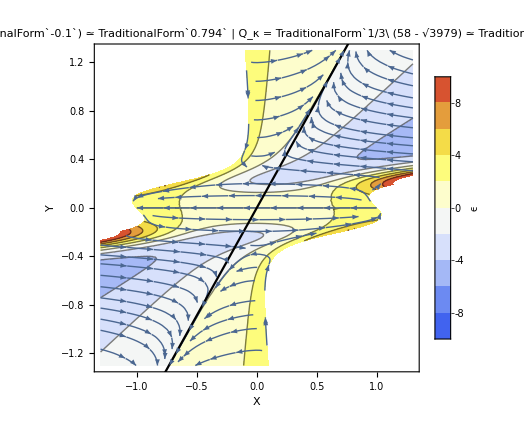
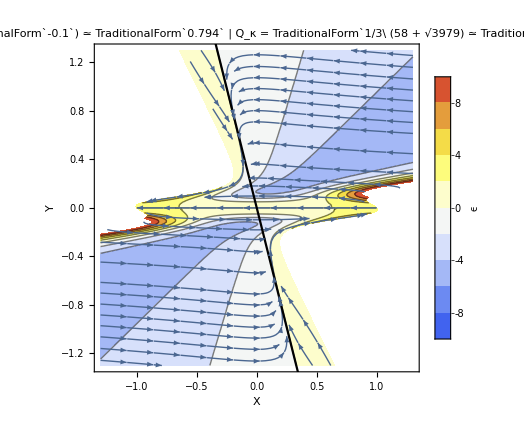
-Graphics- | -Graphics-

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Subscript[Ω, m],Subscript[Ω, r]}={0,0}; mincol=-10; maxcol=10; sep=10; size=440; color="TemperatureMap"; Clear[r];Unset[Subscript[Q, κ]];Print[]; 
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,α,Subscript[Q, κ] α,0,0,0,0,0,0,0,0};

cons012=Reduce[consJ0&&consJ1&&consJ2,{α,Subscript[Q, κ]},Reals]; 
Qκmin=Minimize[{Subscript[Q, κ],cons012[[2]]},Subscript[Q, κ]][[1]];
Qκmax=Maximize[{Subscript[Q, κ],cons012[[2]]},Subscript[Q, κ]][[1]];
α=10^r;r=-0.1; L=1.3;Subscript[Q, κ]=Qκmin;

pp1=Show[{Legended[ ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->(ColorData[color,Rescale[#,{mincol,maxcol}]]&),
ColorFunctionScaling->False,PlotRange->{mincol,maxcol},ImageSize->size,RegionFunction->Function[{X,Y},Z4≥0]],BarLegend[{color,{mincol,maxcol}},Range[mincol,maxcol,2],LegendMarkerSize->size*0.72,LegendLabel->Style["ϵ   ",14]] ],
StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},RegionFunction->Function[{X,Y},Z4≥0]],Plot[βval X,{X,-L,L},PlotStyle->Black]},PlotLabel->Style[StringForm["α = 10^(``) ≃ `` | Q_κ = `` ≃ ``",r,Round[α//N,0.001],Subscript[Q, κ],Round[Subscript[Q, κ]//N,0.001]],15] ,RotateLabel->False, FrameLabel->{Style["X",Bold,15],Style["Y",Bold,15]} ];

 Subscript[Q, κ]=Qκmax;
pp2=Show[{Legended[ ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->(ColorData[color,Rescale[#,{mincol,maxcol}]]&),
ColorFunctionScaling->False,PlotRange->{mincol,maxcol},ImageSize->size,RegionFunction->Function[{X,Y},Z4≥0]],BarLegend[{color,{mincol,maxcol}},Range[mincol,maxcol,2],LegendMarkerSize->size*0.72,LegendLabel->Style["ϵ   ",14]] ],
StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},RegionFunction->Function[{X,Y},Z4≥0]],Plot[βval X,{X,-L,L},PlotStyle->Black]},PlotLabel->Style[StringForm["α = 10^(``) ≃ `` | Q_κ = `` ≃ ``",r,Round[α//N,0.001],Subscript[Q, κ],Round[Subscript[Q, κ]//N,0.001]],15] ,RotateLabel->False, FrameLabel->{Style["X",Bold,15],Style["Y",Bold,15]} ];

Grid[{{pp1,pp2}}]

name[1/3 (58-√3979)]=StringForm["α = 10^(``) | Q_κ = `` ≃ ``",r,Subscript[Q, κ],Round[Subscript[Q, κ]//N,0.001]];
name[1/3 (58+√3979)]=name[1/3 (58-√3979)];name[8.55]=StringForm["α = 10^(``) | Q_κ → 77/9 ≃ ``",r,Round[Subscript[Q, κ]//N,0.001]];

Table[Show[{
Legended[ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->(ColorData[color,Rescale[#,{mincol,maxcol}]]&),ColorFunctionScaling->False,PlotRange->{mincol,maxcol},RegionFunction->Function[{X,Y},Z4≥0],ImageSize->260],BarLegend[{color,{mincol,maxcol}},Range[mincol,maxcol,2]]],StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},RegionFunction->Function[{X,Y},Z4≥0]],Plot[βval X,{X,-L,L},PlotStyle->Black]},PlotLabel->Style[name[Subscript[Q, κ]],13] ,RotateLabel->False, FrameLabel->{Style["X",Bold,12],Style["Y",Bold,12]}],{Subscript[Q, κ],{1/3 (58-√3979),8.55,1/3 (58+√3979)}}]

Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],r]; Unset[Subscript[Q, κ]];
```

### α, θ_4 - Its phase diagram exhibits β > 0.

#### General expressions

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]]; 
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,α,0,0,Subscript[Q, 4] α,0,0,0,0,0,0};
SolveForThis={α,Subscript[Q, 4]}; AssumeThis=(α≠0)&&(Subscript[Q, 4]≠0);

Print["\n",fried==0/.F->Fval,"\n",eq1==0/.F->Fval,"\n",eq2==0/.F->Fval,"\n\n","Z^4 = ",Z4=(Zval^4//Factor//FullSimplify),"\n","P = ",(Pval//Factor//FullSimplify),"\n","ϵ = ",ϵxy=(ϵval//Factor//FullSimplify),"\nλ_+ + λ_- = ",lambdaSum,"\nλ_+ * λ_- = ",lambdaPrd,"\n\nc_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum,"\nc_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",csprd,"\n\nβ = ",(βval//Simplify)," , γ^4 = ",(γvalAbs^4//Simplify),"\n"]
```

-1+X^2+2 X Y+Y^2+2 Z^4+(10 X^2 Y^2-188 X Y^3-32 Y^4) α+Q_4 (-64 X Y^3-32 Y^4) α+Ω_m+Ω_r==0
3+X^2+2 X Y+Y^2+2 Z^4+Q_4 (192 X^2 Y^2+32 √2 P Y^3+256 X Y^3+32 Y^4) α-2 ϵ+α (614 X^2 Y^2+104 √2 P Y^3+316 X Y^3-340 Y^4+124 Y^4 ϵ)+Ω_r==0
P/(√2)+3 X+2 Y+(4 Z^4)/Y-Y ϵ+Q_4 α (-32 Y^3+32 Y^3 ϵ)+α (10 X^2 Y+5 √2 P Y^2+30 X Y^2-218 Y^3+94 Y^3 ϵ)==0

Z^4 = 1/2 (1-(X+Y)^2+2 Y^2 (-5 X^2+2 (47+16 Q_4) X Y+16 (1+Q_4) Y^2) α-Ω_m-Ω_r)
P = ((4 X^2 (1+Y^2 α (5+(89+48 Q_4) Y^2-8 (1813+16 Q_4 (73+12 Q_4)) Y^4 α))+2 X Y (1+2 Y^2 α (-203-64 Q_4+95 Y^2+80 Q_4 Y^2-2 (-371+16 Q_4 (237+80 Q_4)) Y^4 α))+4 (-1+Ω_m+Ω_r)-Y^2 (-4+4 (77-16 Q_4) Y^4 α+128 (1+Q_4) (-77+16 Q_4) Y^6 α^2+Ω_m+2 Y^2 α (-90-16 Q_4 (-6+Ω_m)+77 Ω_m+124 Ω_r)))/(√2 Y (1+2 Y^2 α (5-(83+16 Q_4) Y^2+2 (2289+16 Q_4 (99+16 Q_4)) Y^4 α))))
ϵ = ((4-Ω_m+2 Y^2 α (-188+510 X^2+203 Ω_m+208 Ω_r+2 (-512 Q_4^2 Y^3 (4 X+Y) α+Y (178 X-77 Y+14 (5 X-47 Y) (29 X-11 Y) Y α)+16 Q_4 (Y^2+60 Y^4 α+5 X^2 (1+8 Y^2 α)+X (6 Y-772 Y^3 α)+2 (-1+Ω_m+Ω_r)))))/(2+4 Y^2 α (5-(83+16 Q_4) Y^2+2 (2289+16 Q_4 (99+16 Q_4)) Y^4 α)))
λ_+ + λ_- = 5/4+5 α (ψ̂)^2+1/8 (61 α-16 Q_4 α) (ψ̂)^4
λ_+ * λ_- = 1/8 (2+10 α (ψ̂)^2+(61 α-16 Q_4 α) (ψ̂)^4+(105 α^2+240 Q_4 α^2-128 Q_4^2 α^2) (ψ̂)^6)

c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (4+20 α (ψ̂)^2+2 (71 α-8 Q_4 α) (ψ̂)^4+2 (155 α^2+120 Q_4 α^2) (ψ̂)^6)/(2+10 α (ψ̂)^2+(61 α-16 Q_4 α) (ψ̂)^4+(105 α^2+240 Q_4 α^2-128 Q_4^2 α^2) (ψ̂)^6)
c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (2+10 α (ψ̂)^2+81 α (ψ̂)^4+205 α^2 (ψ̂)^6)/(2+10 α (ψ̂)^2+(61 α-16 Q_4 α) (ψ̂)^4+(105 α^2+240 Q_4 α^2-128 Q_4^2 α^2) (ψ̂)^6)

β = (203+64 Q_4)/(77-16 Q_4) , γ^4 = ((203+64 Q_4)^2 (917+128 Q_4) (2289+1584 Q_4+256 Q_4^2) α)/(77-16 Q_4)^4

#### Constraints - external region

```mathematica
t0=AbsoluteTime[]; aux1={}; aux2={}; NumSum={};NumPrd={}; Den={}; 
cons01=Reduce[βval<0&&γval^4>0,Reals,Backsubstitution->True]; 
cons02=Reduce[βval>0&&γval^4>0,Reals,Backsubstitution->True];
consJ0=Reduce[(cons01||cons02)&&AssumeThis,SolveForThis,Reals];Print[
"\n0. Expressions involving β,γ","\n\n   β = ",(βval//Simplify)," , γ^4 = ",(γvalAbs^4//Simplify),
"\n\n0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]\n\n   ",cons01,
"\n\n\n0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]\n\n   ",cons02,
"\n\n J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) \n\n   ",consJ0,"\n"];

tt=CoefficientList[lambdaSum,OverHat[ψ],{5}]//FullSimplify;
dd=CoefficientList[lambdaPrd,OverHat[ψ],{7}]//FullSimplify;
For[i=1,i≤Length[consT],i++,AppendTo[aux1,((consT[[i]]/.Subscript[t,k_]:>tt[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[aux2,((consD[[i]]/.Subscript[d,k_]:>dd[[k+1]]))//Simplify]];
cons11=Reduce[Apply[Or,aux1],Reals,Backsubstitution->True];
cons12=Reduce[Apply[Or,aux2],Reals,Backsubstitution->True];
consJ1=Reduce[cons11&&cons12&&AssumeThis,SolveForThis,Reals];Print[
"\n\n1. Expressions involving Eigenvalues[ 𝕂 ]","\n\n   λ_+ + λ_- = ",lambdaSum,"\n   λ_+ * λ_- = ",lambdaPrd,
"\n\n\n1.1. Conditions for  [ λ_+ + λ_- > 0 ]\n\n   ",cons11,
"\n\n\n1.2. Conditions for  [ λ_+ * λ_- > 0 ]\n\n   ",cons12,
"\n\n\n J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) \n\n   ",consJ1,"\n"]

ns=CoefficientList[Numerator[cssum],OverHat[ψ],7]//FullSimplify;
np=CoefficientList[Numerator[csprd],OverHat[ψ],7]//FullSimplify;
dsp=CoefficientList[Denominator[cssum],OverHat[ψ],7]//FullSimplify;
For[i=1,i≤Length[consD],i++,AppendTo[NumSum,((consD[[i]]/.Subscript[d,k_]:>ns[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[NumPrd,((consD[[i]]/.Subscript[d,k_]:>np[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[Den,((consD[[i]]/.Subscript[d,k_]:>dsp[[k+1]]))//Simplify]];
cons21=Reduce[Apply[Or,NumSum]&&AssumeThis,SolveForThis,Reals];
cons22=Reduce[Apply[Or,NumPrd]&&AssumeThis,SolveForThis,Reals];
cons23=Reduce[Apply[Or,Den]&&AssumeThis,SolveForThis,Reals];
consJ2=Reduce[cons21&&cons22&&cons23&&AssumeThis,SolveForThis,Reals];Print[
"\n2. Expressions involving  c_s^2 ","\n\n   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum,"\n   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = ",csprd,
"\n\n2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons21,
"\n\n\n2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons22,
"\n\n\n2.3. Conditions for Denominator > 0\n\n   ",cons23,
"\n\n\n J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) \n\n   ",consJ2,"\n"]

cons31=Reduce[Resolve[ForAll[OverHat[ψ],cs21≤1],Reals]&&AssumeThis,SolveForThis,Reals];
cons32=Reduce[Resolve[ForAll[OverHat[ψ],cs22≤1],Reals]&&AssumeThis,SolveForThis,Reals];
consJ3=Reduce[cons31&&cons32&&AssumeThis,SolveForThis,Reals];
Print["\n3.1 Conditions for c_(s, SubscriptBox[h, ±])^2 ≤ 1\n\n   ",cons31,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,cons31],
"\n\n3.2 Conditions for  c_(s, SubscriptBox[γ, ±])^2 ≤ 1\n\n   ",cons32,"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,cons32],
"\n\n J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) \n\n   ",consJ3,"\n"]

consJ4=Reduce[Resolve[ForAll[OverHat[ψ],cs21==1],Reals]&&AssumeThis,SolveForThis,Reals];Print[
"\n 4. Joint constraints for [ GRAVITATIONAL WAVES ]  \n\n   ",
consJ4,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,consJ4],"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,consJ4],"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&AssumeThis,SolveForThis,Reals],"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3∧J4) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&consJ4&&AssumeThis,SolveForThis,Reals],"\n"]

Print["\n\nThis process took about ",Round[(AbsoluteTime[]-t0)/60,0.001]," minutes.\n"];
```

0. Expressions involving β,γ

   β = (203+64 Q_4)/(77-16 Q_4) , γ^4 = ((203+64 Q_4)^2 (917+128 Q_4) (2289+1584 Q_4+256 Q_4^2) α)/(77-16 Q_4)^4

0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]

   (α<0&&Q_4<-917/128)||(α<0&&1/32 (-99-√645)<Q_4<-203/64)||(α>0&&-917/128<Q_4<1/32 (-99-√645))||(α>0&&Q_4>77/16)


0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]

   (α<0&&-203/64<Q_4<1/32 (-99+√645))||(α>0&&1/32 (-99+√645)<Q_4<77/16)

 J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) 

   (α<0&&(Q_4<-917/128||1/32 (-99-√645)<Q_4<-203/64||-203/64<Q_4<1/32 (-99+√645)))||(α>0&&(-917/128<Q_4<1/32 (-99-√645)||1/32 (-99+√645)<Q_4<0||0<Q_4<77/16||Q_4>77/16))

1. Expressions involving Eigenvalues[ 𝕂 ]

   λ_+ + λ_- = 5/4+5 α (ψ̂)^2+1/8 (61 α-16 Q_4 α) (ψ̂)^4
   λ_+ * λ_- = 1/8 (2+10 α (ψ̂)^2+(61 α-16 Q_4 α) (ψ̂)^4+(105 α^2+240 Q_4 α^2-128 Q_4^2 α^2) (ψ̂)^6)


1.1. Conditions for  [ λ_+ + λ_- > 0 ]

   (α<0&&Q_4>1/16 (61-40 α))||α==0||(α>0&&Q_4≤61/16)


1.2. Conditions for  [ λ_+ * λ_- > 0 ]

   (Q_4<1/16 (15-√435)&&α==0)||(1/16 (15-√435)≤Q_4≤1/16 (15+√435)&&α≥0)||(Q_4>1/16 (15+√435)&&α==0)


 J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) 

   α>0&&(1/16 (15-√435)≤Q_4<0||0<Q_4≤1/16 (15+√435))

2. Expressions involving  c_s^2 

   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (4+20 α (ψ̂)^2+2 (71 α-8 Q_4 α) (ψ̂)^4+2 (155 α^2+120 Q_4 α^2) (ψ̂)^6)/(2+10 α (ψ̂)^2+(61 α-16 Q_4 α) (ψ̂)^4+(105 α^2+240 Q_4 α^2-128 Q_4^2 α^2) (ψ̂)^6)
   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = (2+10 α (ψ̂)^2+81 α (ψ̂)^4+205 α^2 (ψ̂)^6)/(2+10 α (ψ̂)^2+(61 α-16 Q_4 α) (ψ̂)^4+(105 α^2+240 Q_4 α^2-128 Q_4^2 α^2) (ψ̂)^6)

2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0

   (α≤-61/450&&Q_4>Root[-357911+233900 α-77500 α^2+(120984-188800 α-60000 α^2) #1+(-13632-236800 α) #1^2+512 #1^3&,3])||(-61/450<α<0&&Q_4>Root[-357911+233900 α-77500 α^2+(120984-188800 α-60000 α^2) #1+(-13632-236800 α) #1^2+512 #1^3&,1])||(0<α<1647/350&&(-31/24≤Q_4<0||0<Q_4<Root[-357911+233900 α-77500 α^2+(120984-188800 α-60000 α^2) #1+(-13632-236800 α) #1^2+512 #1^3&,1]))||(α≥1647/350&&(-31/24≤Q_4<0||0<Q_4<Root[-357911+233900 α-77500 α^2+(120984-188800 α-60000 α^2) #1+(-13632-236800 α) #1^2+512 #1^3&,3]))


2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0

   α>0&&(Q_4<0||Q_4>0)


2.3. Conditions for Denominator > 0

   α>0&&(1/16 (15-√435)≤Q_4<0||0<Q_4≤1/16 (15+√435))


 J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) 

   α>0&&(1/16 (15-√435)≤Q_4<0||0<Q_4≤1/16 (15+√435))

3.1 Conditions for c_(s, SubscriptBox[h, ±])^2 ≤ 1

   α>0&&(1/16 (15-√435)≤Q_4<0||0<Q_4≤1/16 (15+√435))

   c_(s, SubscriptBox[h, ±])^2 = (-10 α (ψ̂)^2+(-71+8 Q_4) α (ψ̂)^4-5 (31+24 Q_4) α^2 (ψ̂)^6+2 (-1+α Abs[ψ̂]^3 √((1+5 α (ψ̂)^2) (64 Q_4^2+(5+4 Q_4)^2 (ψ̂)^2+(125-600 Q_4+2032 Q_4^2) α (ψ̂)^4))))/(-2-10 α (ψ̂)^2+(-61+16 Q_4) α (ψ̂)^4+(-105-240 Q_4+128 Q_4^2) α^2 (ψ̂)^6)

3.2 Conditions for  c_(s, SubscriptBox[γ, ±])^2 ≤ 1

   False

   c_(s, SubscriptBox[γ, ±])^2 = (-2-10 α (ψ̂)^2+(-71+8 Q_4) α (ψ̂)^4-5 (31+24 Q_4) α^2 (ψ̂)^6-2 α (ψ̂)^3 √((1+5 α (ψ̂)^2) (64 Q_4^2+(5+4 Q_4)^2 (ψ̂)^2+(125-600 Q_4+2032 Q_4^2) α (ψ̂)^4)))/(-2-10 α (ψ̂)^2+(-61+16 Q_4) α (ψ̂)^4+(-105-240 Q_4+128 Q_4^2) α^2 (ψ̂)^6)

 J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) 

   False

4. Joint constraints for [ GRAVITATIONAL WAVES ]  

   False

   c_(s, SubscriptBox[h, ±])^2 = (-2-10 α (ψ̂)^2+(-71+8 Q_4) α (ψ̂)^4-5 (31+24 Q_4) α^2 (ψ̂)^6+2 α (ψ̂)^3 √((1+5 α (ψ̂)^2) (64 Q_4^2+(5+4 Q_4)^2 (ψ̂)^2+(125-600 Q_4+2032 Q_4^2) α (ψ̂)^4)))/(-2-10 α (ψ̂)^2+(-61+16 Q_4) α (ψ̂)^4+(-105-240 Q_4+128 Q_4^2) α^2 (ψ̂)^6)

   c_(s, SubscriptBox[γ, ±])^2 = (-2-10 α (ψ̂)^2+(-71+8 Q_4) α (ψ̂)^4-5 (31+24 Q_4) α^2 (ψ̂)^6-2 α (ψ̂)^3 √((1+5 α (ψ̂)^2) (64 Q_4^2+(5+4 Q_4)^2 (ψ̂)^2+(125-600 Q_4+2032 Q_4^2) α (ψ̂)^4)))/(-2-10 α (ψ̂)^2+(-61+16 Q_4) α (ψ̂)^4+(-105-240 Q_4+128 Q_4^2) α^2 (ψ̂)^6)

Summary of CONSTRAINTS (J1∧J2∧J3) 

   False

Summary of CONSTRAINTS (J1∧J2∧J3∧J4) 

   False

This process took about 0.101 minutes.

#### Phase portrait

```mathematica
t0=AbsoluteTime[]; Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]];ξ=1;
NumΩmp=((Ωmp//NoMoreFPϵ)/.{X->x[t],Y->y[t],Subscript[Ω, m]->0,Subscript[Ω, r]->0,Subscript[χ, 34]->Subscript[χ, 3]+Subscript[χ, 4]}//Simplify);
NumΩrp=((Ωrp//NoMoreFPϵ)/.{X->x[t],Y->y[t],Subscript[Ω, m]->0,Subscript[Ω, r]->0,Subscript[χ, 34]->Subscript[χ, 3]+Subscript[χ, 4]}//Simplify);
NumXp=((Xp//NoMoreFPϵ)/.{X->x[t],Y->y[t],Subscript[Ω, m]->0,Subscript[Ω, r]->0,Subscript[χ, 34]->Subscript[χ, 3]+Subscript[χ, 4]}//Simplify);
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]]; 

NumSol[{tmax_,Ωm0_,Ωr0_,x0_,y0_}]:=NDSolve[{ 
Ωm'[t]==NumΩmp, Ωr'[t]==NumΩrp, x'[t]==NumXp, y'[t]==x[t], Ωm[0]==Ωm0, Ωr[0]==Ωr0, x[0]==x0, y[0]==y0},{Ωm,Ωr,x,y}, {t,0,tmax},
Method->{StiffnessSwitching,Method->{ExplicitRungeKutta,Automatic}},MaxSteps->10^10,PrecisionGoal->22] (* 16 *)
Print["\nProcess ended within ",Round[(AbsoluteTime[]-t0)/60,0.01]," minutes. → The specified PDE solver has been defined.\n"];
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]];

Print["Asymptotic behaviour, ghosts & Laplacian instabilities:\n"]
cons012=Reduce[consJ0&&consJ1&&consJ2,{α,Subscript[Q, 4]},Reals] 
Q4min=Minimize[{Subscript[Q, 4],cons012[[2]]},Subscript[Q, 4]][[1]];
Q4max=Maximize[{Subscript[Q, 4],cons012[[2]]},Subscript[Q, 4]][[1]]; 
cons012//N

{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,α,0,0,Subscript[Q, 4] α,0,0,0,0,0,0};
TTT=Mod[ArcTan[βval/.Subscript[Q, 4]->Q4min]/Degree//N,180];  (* Lowest angle *)
BBB=Mod[ArcTan[βval/.Subscript[Q, 4]->Q4max]/Degree//N,180];  (* Highest angle *)
θ̄ == Median[{TTT,BBB}]
Δ==Abs[TTT-BBB]/2
```

Process ended within 0.05 minutes. → The specified PDE solver has been defined.

Asymptotic behaviour, ghosts & Laplacian instabilities:

α>0&&(1/16 (15-√435)≤Q_4<0||0<Q_4≤1/16 (15+√435))

α>0.&&(-0.366041≤Q_4<0.||0.<Q_4≤2.24104)

θ̄==74.229

Δ==8.99799

```mathematica
{Subscript[Ω, m],Subscript[Ω, r]}={0,0}; mincol=-10; maxcol=10; sep=10; size=460; color="TemperatureMap"; Clear[r];Unset[Subscript[Q, 4]];Print[]; 
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,α,0,0,Subscript[Q, 4] α,0,0,0,0,0,0};

cons012=Reduce[consJ0&&consJ1&&consJ2,{α,Subscript[Q, 4]},Reals] 
Q4min=Minimize[{Subscript[Q, 4],cons012[[2]]},Subscript[Q, 4]][[1]];
Q4max=Maximize[{Subscript[Q, 4],cons012[[2]]},Subscript[Q, 4]][[1]]; 
cons012//N
Print[];
points1=Graphics[{PointSize[0.02],Point[{{0,-Sqrt[(3 Subscript[θ, 1]+√(308 α+9 Subscript[θ, 1]^2-64 Subscript[θ, 4]-36 κ-8 Subscript[χ, 34]))/(2 (77 α-16 Subscript[θ, 4]-9 κ-2 Subscript[χ, 34]))]},{0,Sqrt[(3 Subscript[θ, 1]+√(308 α+9 Subscript[θ, 1]^2-64 Subscript[θ, 4]-36 κ-8 Subscript[χ, 34]))/(2 (77 α-16 Subscript[θ, 4]-9 κ-2 Subscript[χ, 34]))]}}]}];
 α=10^r;r=-0.1; L=1.3;
Table[Show[{
Legended[ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->(ColorData[color,Rescale[#,{mincol,maxcol}]]&),ColorFunctionScaling->False,PlotRange->{mincol,maxcol},RegionFunction->Function[{X,Y},Z4≥0],ImageSize->size],BarLegend[{color,{mincol,maxcol}},Range[mincol,maxcol,2]]],points1,StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},RegionFunction->Function[{X,Y},Z4≥0]],Plot[βval X,{X,-L,L},PlotStyle->Black]},PlotLabel->Style[StringForm["α = 10^(``) | Q_κ = `` ≃ ``",r,Subscript[Q, 4],Round[Subscript[Q, 4]//N,0.001]],15] ,RotateLabel->False, FrameLabel->{Style["X",Bold,12],Style["Y",Bold,12]}],{Subscript[Q, 4],{1/16 (15-√435),1/16 (15+√435)}}]

Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],r]; Unset[Subscript[Q, 4]];
```

α>0&&(1/16 (15-√435)≤Q_4<0||0<Q_4≤1/16 (15+√435))

α>0.&&(-0.366041≤Q_4<0.||0.<Q_4≤2.24104)

{-Graphics-,-Graphics-}

### Only χ_3, χ_4 [ Takes part in: Laplacian instabilities | Not in: Asymptotic behaviour, Ghosts conditions ] - Cannot have a phase diagram on its own.

#### General expressions

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]];
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,0,0,0,0,0,0,Subscript[χ, 3],Subscript[χ, 3]+Subscript[χ, 4],Subscript[χ, 4],0};
SolveForThis={Subscript[χ, 3],Subscript[χ, 4]};AssumeThis=True;

Print["\n",fried==0/.F->Fval,"\n",eq1==0/.F->Fval,"\n",eq2==0/.F->Fval,"\n\n","Z^4 = ",Z4=(Zval^4//Factor//FullSimplify),"\n","P = ",(Pval//Factor//FullSimplify),"\n","ϵ = ",ϵxy=(ϵval//Factor//FullSimplify),"\nλ_+ + λ_- = ",lambdaSum,"\nλ_+ * λ_- = ",lambdaPrd,"\n\nc_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum,"\nc_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",csprd,"\n\nβ = ",(βval//FullSimplify)," , γ^4 = ",(γvalAbs^4//Simplify),"\n"]
```

-1+X^2+2 X Y+Y^2+2 Z^4+(-4 X^2 Y^2-8 X Y^3-4 Y^4) χ_3+(-4 X^2 Y^2-8 X Y^3-4 Y^4) χ_4+Ω_m+Ω_r==0
3+X^2+2 X Y+Y^2+2 Z^4-2 ϵ+(4 X^2 Y^2+8 X Y^3+4 Y^4) χ_3+(4 X^2 Y^2+8 X Y^3+4 Y^4) χ_4+Ω_r==0
P/(√2)+3 X+2 Y+(4 Z^4)/Y-Y ϵ+(-4 X^2 Y-2 √2 P Y^2-12 X Y^2-4 Y^3+4 Y^3 ϵ) χ_3+(-4 X^2 Y-2 √2 P Y^2-12 X Y^2-4 Y^3+4 Y^3 ϵ) χ_4==0

Z^4 = 1/2 (1+(X+Y)^2 (-1+4 Y^2 (χ_3+χ_4))-Ω_m-Ω_r)
P = (2 X Y (-1+4 Y^2 (χ_3+χ_4)) (1+8 Y^4 (χ_3+χ_4))+4 X^2 (-1+2 Y^2 (χ_3+χ_4) (1-Y^2+4 Y^4 (χ_3+χ_4)))+Y^2 (-4+4 Y^2 (χ_3+χ_4) (6-2 Y^2+8 Y^4 (χ_3+χ_4)-Ω_m)+Ω_m)-4 (-1+Ω_m+Ω_r))/(√2 Y (-1+4 Y^2 (χ_3+χ_4)))
ϵ = 2+4 Y^2 (X+Y)^2 (χ_3+χ_4)-Ω_m/2
λ_+ + λ_- = 5/4-2 (χ_3+χ_4) (ψ̂)^2
λ_+ * λ_- = 1/8 (2-4 (χ_3+χ_4) (ψ̂)^2)

c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (4+4 (χ_4-3 (χ_3+χ_4)) (ψ̂)^2)/(2-4 (χ_3+χ_4) (ψ̂)^2)
c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (2+2 (2 χ_4-4 (χ_3+χ_4)) (ψ̂)^2)/(2-4 (χ_3+χ_4) (ψ̂)^2)

β = -1 , γ^4 = 0

#### Constraints - external region

```mathematica
t0=AbsoluteTime[]; aux1={}; aux2={}; NumSum={};NumPrd={}; Den={}; 
cons01=Reduce[βval<0&&γval^4>0,Reals,Backsubstitution->True]; 
cons02=Reduce[βval>0&&γval^4>0,Reals,Backsubstitution->True];
consJ0=Reduce[(cons01||cons02)&&AssumeThis,SolveForThis,Reals];Print[
"\n0. Expressions involving β,γ","\n\n   β = ",(βval//FullSimplify)," , γ^4 = ",(γvalAbs^4//Simplify),
"\n\n0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]\n\n   ",cons01,
"\n\n\n0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]\n\n   ",cons02,
"\n\n J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) \n\n   ",consJ0,"\n"];

tt=CoefficientList[lambdaSum,OverHat[ψ],{5}]//FullSimplify;
dd=CoefficientList[lambdaPrd,OverHat[ψ],{7}]//FullSimplify;
For[i=1,i≤Length[consT],i++,AppendTo[aux1,((consT[[i]]/.Subscript[t,k_]:>tt[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[aux2,((consD[[i]]/.Subscript[d,k_]:>dd[[k+1]]))//Simplify]];
cons11=Reduce[Apply[Or,aux1],Reals,Backsubstitution->True];
cons12=Reduce[Apply[Or,aux2],Reals,Backsubstitution->True];
consJ1=Reduce[cons11&&cons12&&AssumeThis,SolveForThis,Reals];Print[
"\n\n1. Expressions involving Eigenvalues[ 𝕂 ]","\n\n   λ_+ + λ_- = ",lambdaSum,"\n   λ_+ * λ_- = ",lambdaPrd,
"\n\n\n1.1. Conditions for  [ λ_+ + λ_- > 0 ]\n\n   ",cons11,
"\n\n\n1.2. Conditions for  [ λ_+ * λ_- > 0 ]\n\n   ",cons12,
"\n\n\n J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) \n\n   ",consJ1,"\n"]

ns=CoefficientList[Numerator[cssum],OverHat[ψ],7]//FullSimplify;
np=CoefficientList[Numerator[csprd],OverHat[ψ],7]//FullSimplify;
dsp=CoefficientList[Denominator[cssum],OverHat[ψ],7]//FullSimplify;
For[i=1,i≤Length[consD],i++,AppendTo[NumSum,((consD[[i]]/.Subscript[d,k_]:>ns[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[NumPrd,((consD[[i]]/.Subscript[d,k_]:>np[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[Den,((consD[[i]]/.Subscript[d,k_]:>dsp[[k+1]]))//Simplify]];
cons21=Reduce[Apply[Or,NumSum]&&AssumeThis,SolveForThis,Reals];
cons22=Reduce[Apply[Or,NumPrd]&&AssumeThis,SolveForThis,Reals];
cons23=Reduce[Apply[Or,Den]&&AssumeThis,SolveForThis,Reals];
consJ2=Reduce[cons21&&cons22&&cons23&&AssumeThis,SolveForThis,Reals];Print[
"\n2. Expressions involving  c_s^2 ","\n\n   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum,"\n   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = ",csprd,
"\n\n2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons21,
"\n\n\n2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons22,
"\n\n\n2.3. Conditions for Denominator > 0\n\n   ",cons23,
"\n\n\n J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) \n\n   ",consJ2,"\n"]

cons31=Reduce[Resolve[ForAll[OverHat[ψ],cs21≤1],Reals]&&AssumeThis,SolveForThis,Reals];
cons32=Reduce[Resolve[ForAll[OverHat[ψ],cs22≤1],Reals]&&AssumeThis,SolveForThis,Reals];
consJ3=Reduce[cons31&&cons32&&AssumeThis,SolveForThis,Reals];
Print["\n3.1 Conditions for c_(s, SubscriptBox[h, ±])^2 ≤ 1\n\n   ",cons31,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,cons31],
"\n\n3.2 Conditions for  c_(s, SubscriptBox[γ, ±])^2 ≤ 1\n\n   ",cons32,"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,cons32],
"\n\n J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) \n\n   ",consJ3,"\n"]

consJ4=Reduce[Resolve[ForAll[OverHat[ψ],cs21==1],Reals]&&AssumeThis,SolveForThis,Reals];Print[
"\n 4. Joint constraints for [ GRAVITATIONAL WAVES ]  \n\n   ",
consJ4,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,consJ4],"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,consJ4],"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&AssumeThis,SolveForThis,Reals],"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3∧J4) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&consJ4&&AssumeThis,SolveForThis,Reals],"\n"]

Print["\n\nThis process took about ",Round[(AbsoluteTime[]-t0)/60,0.001]," minutes.\n"];
```

0. Expressions involving β,γ

   β = -1 , γ^4 = 0

0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]

   False


0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]

   False

 J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) 

   False

1. Expressions involving Eigenvalues[ 𝕂 ]

   λ_+ + λ_- = 5/4-2 (χ_3+χ_4) (ψ̂)^2
   λ_+ * λ_- = 1/8 (2-4 (χ_3+χ_4) (ψ̂)^2)


1.1. Conditions for  [ λ_+ + λ_- > 0 ]

   χ_3≤-χ_4


1.2. Conditions for  [ λ_+ * λ_- > 0 ]

   χ_3≤-χ_4


 J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) 

   χ_4≤-χ_3

2. Expressions involving  c_s^2 

   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (4+4 (χ_4-3 (χ_3+χ_4)) (ψ̂)^2)/(2-4 (χ_3+χ_4) (ψ̂)^2)
   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = (2+2 (2 χ_4-4 (χ_3+χ_4)) (ψ̂)^2)/(2-4 (χ_3+χ_4) (ψ̂)^2)

2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0

   χ_4≤-(3 χ_3)/2


2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0

   χ_4≤-2 χ_3


2.3. Conditions for Denominator > 0

   χ_4≤-χ_3


 J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) 

   (χ_3≤0&&χ_4≤-χ_3)||(χ_3>0&&χ_4≤-2 χ_3)

3.1 Conditions for c_(s, SubscriptBox[h, ±])^2 ≤ 1

   χ_4≤-χ_3

   c_(s, SubscriptBox[h, ±])^2 = (-1+(3 χ_3+2 χ_4+Abs[χ_3]) (ψ̂)^2)/(-1+2 (χ_3+χ_4) (ψ̂)^2)

3.2 Conditions for  c_(s, SubscriptBox[γ, ±])^2 ≤ 1

   χ_3≥0&&χ_4≤-χ_3

   c_(s, SubscriptBox[γ, ±])^2 = 1

 J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) 

   χ_3≥0&&χ_4≤-χ_3

4. Joint constraints for [ GRAVITATIONAL WAVES ]  

   χ_3≤0&&χ_4≤-χ_3

   c_(s, SubscriptBox[h, ±])^2 = 1

   c_(s, SubscriptBox[γ, ±])^2 = (-1+2 (2 χ_3+χ_4) (ψ̂)^2)/(-1+2 (χ_3+χ_4) (ψ̂)^2)

Summary of CONSTRAINTS (J1∧J2∧J3) 

   χ_3≥0&&χ_4≤-2 χ_3

Summary of CONSTRAINTS (J1∧J2∧J3∧J4) 

   χ_3==0&&χ_4≤0

This process took about 0.007 minutes.

#### Phase portrait

```mathematica
t0=AbsoluteTime[]; Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]];ξ=1;
NumΩmp=((Ωmp//NoMoreFPϵ)/.{X->x[t],Y->y[t],Subscript[Ω, m]->0,Subscript[Ω, r]->0}//Simplify);
NumΩrp=((Ωrp//NoMoreFPϵ)/.{X->x[t],Y->y[t],Subscript[Ω, m]->0,Subscript[Ω, r]->0}//Simplify);
NumXp=((Xp//NoMoreFPϵ)/.{X->x[t],Y->y[t],Subscript[Ω, m]->0,Subscript[Ω, r]->0}//Simplify);
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]]; 

NumSol[{tmax_,Ωm0_,Ωr0_,x0_,y0_}]:=NDSolve[{ 
Ωm'[t]==NumΩmp, Ωr'[t]==NumΩrp, x'[t]==NumXp, y'[t]==x[t], Ωm[0]==Ωm0, Ωr[0]==Ωr0, x[0]==x0, y[0]==y0},{Ωm,Ωr,x,y}, {t,0,tmax},
Method->{StiffnessSwitching,Method->{ExplicitRungeKutta,Automatic}},MaxSteps->10^10,PrecisionGoal->22] (* 16 *)
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]];
```

```mathematica
{Subscript[Ω, m],Subscript[Ω, r]}={0,0}; mincol=-8; maxcol=8; sep=8; size=500; color="TemperatureMap"; Print[];
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,0,0,0,0,0,0,Subscript[χ, 3],Subscript[χ, 3]+Subscript[χ, 4],Subscript[χ, 4],0};

Subscript[χ, 3]=0;
Subscript[χ, 4]=-10^r;
r=-0.0001;
L=1.5;

pp=ParametricPlot[Evaluate[{x[t],y[t]}/.NumSol[{100,0,0,-0.5,-0.312}]],{t,0,100},PlotTheme->"Scientific", PlotStyle->{Thickness[0.004],Black}]/.Line[x_]->Sequence[Arrowheads->Table[.02,{40}],Arrow[x]];
Show[{Legended[ ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->(ColorData[color,Rescale[#,{mincol,maxcol}]]&),
ColorFunctionScaling->False,PlotRange->{mincol,maxcol},ImageSize->size,RegionFunction->Function[{X,Y},Z4≥0]],BarLegend[{color,{mincol,maxcol}},Range[-6,6,2],LegendMarkerSize->size*0.72,LegendLabel->Style["ϵ   ",14]] ],
StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},RegionFunction->Function[{X,Y},Z4≥0]],pp
},PlotLabel->Style[StringForm["χ_3 = 0 | χ_4 = ``",Subscript[χ, 4],Round[Subscript[χ, 4],0.00001]],15.5] ,RotateLabel->False, FrameLabel->{Style["X",Bold,12],Style["Y",Bold,12]}]
Clear[r];

L=1;
Table[Show[{
Legended[ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->(ColorData[color,Rescale[#,{mincol,maxcol}]]&),ColorFunctionScaling->False,PlotRange->{mincol,maxcol},RegionFunction->Function[{X,Y},Z4≥0],ImageSize->205],BarLegend[{color,{mincol,maxcol}},Range[-6,6,2]]],Plot[βval X,{X,-L,L},PlotStyle->Black]},PlotLabel->Style[StringForm["χ_3 = 0 | χ_4 = ``",Subscript[χ, 4],Round[Subscript[χ, 4],0.00001]],13] ,RotateLabel->False, FrameLabel->{Style["X",Bold,12],Style["Y",Bold,12]}],{r,{-2.0564,-0.625,0.8116}}]
Clear[κ];
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-}

#### Rupture points

```mathematica
Clear[κ,R,X,Y] (* Estimated rupture points *)
Reduce[(Zval^4/.{Y->R X}//FullSimplify)==0&&Abs[R]>2&&X>0,Reals]//Factor
Log10[%[[-1,2]]/.{X->1.2511,R->Tan[2.5/1.2511]}//N]
X=1.2511
R=Tan[2.5/1.2511]//N
Y=R X
Clear[κ,R,X,Y]
```

X>0&&(R<-2||R>2)&&κ==((-1+X+R X) (1+X+R X))/(2 R^2 (-1+10 R+6 R^2) X^4)

-2.0565

1.2511

-2.19523

-2.74646

### α, θ_4, χ_3, χ_4

#### General expressions

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]]; t0=AbsoluteTime[];
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,α,0,0,Subscript[θ, 4],0,0,Subscript[χ, 34]-Subscript[χ, 4],Subscript[χ, 34],Subscript[χ, 4],0};
Print["\n",fried==0/.F->Fval,"\n",eq1==0/.F->Fval,"\n",eq2==0/.F->Fval,"\n\n","Z^4 = ",Z4=(Zval^4//Factor//FullSimplify),"\n","P = ",(Pval//Factor//FullSimplify),"\n","ϵ = ",ϵxy=(ϵval//Factor//FullSimplify),"\n\nλ_+ + λ_- = ",lambdaSum,"\nλ_+ * λ_- = ",lambdaPrd,"\n\nc_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum,"\nc_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",csprd,"\n\nβ = ",(βval//Simplify)," , γ^4 = ",(γvalAbs^4//Simplify),"\n\n\nThis process took about ",Round[(AbsoluteTime[]-t0)/60,0.001]," minutes.\n"];
```

-1+X^2+2 X Y+Y^2+2 Z^4+(10 X^2 Y^2-188 X Y^3-32 Y^4) α+(-64 X Y^3-32 Y^4) θ_4+(-4 X^2 Y^2-8 X Y^3-4 Y^4) (χ_34-χ_4)+(-4 X^2 Y^2-8 X Y^3-4 Y^4) χ_4+Ω_m+Ω_r==0
3+X^2+2 X Y+Y^2+2 Z^4-2 ϵ+α (614 X^2 Y^2+104 √2 P Y^3+316 X Y^3-340 Y^4+124 Y^4 ϵ)+(192 X^2 Y^2+32 √2 P Y^3+256 X Y^3+32 Y^4) θ_4+(4 X^2 Y^2+8 X Y^3+4 Y^4) (χ_34-χ_4)+(4 X^2 Y^2+8 X Y^3+4 Y^4) χ_4+Ω_r==0
P/(√2)+3 X+2 Y+(4 Z^4)/Y-Y ϵ+α (10 X^2 Y+5 √2 P Y^2+30 X Y^2-218 Y^3+94 Y^3 ϵ)+(-32 Y^3+32 Y^3 ϵ) θ_4+(-4 X^2 Y-2 √2 P Y^2-12 X Y^2-4 Y^3+4 Y^3 ϵ) (χ_34-χ_4)+(-4 X^2 Y-2 √2 P Y^2-12 X Y^2-4 Y^3+4 Y^3 ϵ) χ_4==0

Z^4 = 1/2 (1-Y^2+4 Y^4 (8 (α+θ_4)+χ_34)+X^2 (-1+Y^2 (-10 α+4 χ_34))+2 X Y (-1+Y^2 (94 α+32 θ_4+4 χ_34))-Ω_m-Ω_r)
P = ((16 Y^8 (8 (α+θ_4)+χ_34) (77 α-2 (8 θ_4+χ_34))+Y^6 (-308 α+8 (8 θ_4+χ_34))+2 X (Y-2 Y^3 (203 α+64 θ_4+2 χ_34)+2 Y^5 (95 α+80 θ_4+4 χ_34)+4 Y^7 (371 α^2-8 (8 θ_4+χ_34) (20 θ_4+χ_34)-6 α (632 θ_4+63 χ_34)))-4 X^2 (-1+Y^2 (-5 α+2 χ_34)-Y^4 (89 α+48 θ_4+2 χ_34)+4 Y^6 (3626 α^2+2 (8 θ_4+χ_34) (24 θ_4+χ_34)+α (2336 θ_4+167 χ_34)))-Y^2 (-4+Ω_m)+4 (-1+Ω_m+Ω_r)-2 Y^4 (-2 (8 θ_4+χ_34) (-6+Ω_m)+α (-90+77 Ω_m+124 Ω_r)))/(√2 Y (1-2 Y^4 (83 α+16 θ_4)+2 Y^2 (5 α-2 χ_34)+4 Y^6 (2289 α^2+32 θ_4 (8 θ_4+χ_34)+2 α (792 θ_4+83 χ_34)))))
ϵ = ((4-Ω_m+2 Y^2 (28 (5 X-47 Y) (29 X-11 Y) Y^2 α^2+α (-188-154 Y^2+2 X^2 (255+8 Y^2 (80 θ_4-99 χ_34))+240 Y^4 (8 θ_4+χ_34)-4 X Y (-89+16 Y^2 (386 θ_4+21 χ_34))+203 Ω_m+208 Ω_r)-2 (512 Y^3 (4 X+Y) θ_4^2+χ_34 (4+2 (X+Y)^2 (-1+4 Y^2 χ_34)-Ω_m)+16 θ_4 ((X+Y) (-5 X-Y+8 Y^2 (2 X+Y) χ_34)-2 (-1+Ω_m+Ω_r)))))/(2 (1-2 Y^4 (83 α+16 θ_4)+2 Y^2 (5 α-2 χ_34)+4 Y^6 (2289 α^2+32 θ_4 (8 θ_4+χ_34)+2 α (792 θ_4+83 χ_34)))))

λ_+ + λ_- = 5/4+(5 α-2 χ_34) (ψ̂)^2+1/8 (61 α-16 θ_4) (ψ̂)^4
λ_+ * λ_- = 1/8 (2+2 (5 α-2 χ_34) (ψ̂)^2+(61 α-16 θ_4) (ψ̂)^4+(105 α^2-128 θ_4^2+2 α (120 θ_4-61 χ_34)+32 θ_4 χ_34) (ψ̂)^6)

c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ((4+4 (5 α-3 χ_34+χ_4) (ψ̂)^2+2 (71 α-8 θ_4) (ψ̂)^4+2 (155 α^2-8 θ_4 (-4 χ_34+2 χ_4)+α (120 θ_4-203 χ_34+61 χ_4)) (ψ̂)^6)/(2+2 (5 α-2 χ_34) (ψ̂)^2+(61 α-16 θ_4) (ψ̂)^4+(105 α^2-128 θ_4^2+2 α (120 θ_4-61 χ_34)+32 θ_4 χ_34) (ψ̂)^6))
c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ((2+2 (5 α-4 χ_34+2 χ_4) (ψ̂)^2+81 α (ψ̂)^4+(205 α^2+162 α (-2 χ_34+χ_4)) (ψ̂)^6)/(2+2 (5 α-2 χ_34) (ψ̂)^2+(61 α-16 θ_4) (ψ̂)^4+(105 α^2-128 θ_4^2+2 α (120 θ_4-61 χ_34)+32 θ_4 χ_34) (ψ̂)^6))

β = (203 α+64 θ_4+2 χ_34)/(77 α-2 (8 θ_4+χ_34)) , γ^4 = (((917 α+128 θ_4-2 χ_34) (203 α+64 θ_4+2 χ_34)^2 (2289 α^2+32 θ_4 (8 θ_4+χ_34)+2 α (792 θ_4+83 χ_34)))/(-77 α+16 θ_4+2 χ_34)^4)


This process took about 0.199 minutes.

#### Constraints - external region

```mathematica
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,α,0,0,Subscript[Q, 4] α,0,0,(Subscript[C, 34]-Subscript[C, 3])α,Subscript[C, 34] α,Subscript[C, 4] α,0};
SolveForThis={α,Subscript[Q, 4],Subscript[C, 34],Subscript[C, 4]}; AssumeThis=(α≠0);
cons01=Reduce[βval<0&&γval^4>0,SolveForThis,Reals]; 
cons02=Reduce[βval>0&&γval^4>0,SolveForThis,Reals];
consJ0=Reduce[(cons01||cons02)&&AssumeThis,SolveForThis,Reals];Print[
"\n0. Expressions involving β,γ","\n\n   β = ",(βval//Simplify)," , γ^4 = ",(γvalAbs^4//Simplify),
"\n\n0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]\n\n   ",cons01,
"\n\n\n0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]\n\n   ",cons02,
"\n\n J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) \n\n   ",consJ0,"\n"];

aux1={}; aux2={};
tt=CoefficientList[lambdaSum,OverHat[ψ],{5}]//FullSimplify;
dd=CoefficientList[lambdaPrd,OverHat[ψ],{7}]//FullSimplify;
For[i=1,i≤Length[consT],i++,AppendTo[aux1,((consT[[i]]/.Subscript[t,k_]:>tt[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[aux2,((consD[[i]]/.Subscript[d,k_]:>dd[[k+1]]))//Simplify]];
cons11=Reduce[Apply[Or,aux1],Reals];
cons12=Reduce[Apply[Or,aux2],Reals];
consJ1=Reduce[cons11&&cons12&&AssumeThis,SolveForThis,Reals];Print[
"\n1. Expressions involving Eigenvalues[ 𝕂 ]","\n\n   λ_+ + λ_- = ",lambdaSum,"\n   λ_+ * λ_- = ",lambdaPrd,
"\n\n\n1.1. Conditions for  [ λ_+ + λ_- > 0 ]\n\n   ",cons11,
"\n\n\n1.2. Conditions for  [ λ_+ * λ_- > 0 ]\n\n   ",cons12,
"\n\n\n J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) \n\n   ",consJ1,"\n"]

SolveForThis={α,Subscript[Q, 4],Subscript[C, 34],Subscript[C, 4]}; AssumeThis=(α≠0);
NumSum={};NumPrd={}; Den={}; 
ns=CoefficientList[Numerator[cssum],OverHat[ψ],7]//FullSimplify;
np=CoefficientList[Numerator[csprd],OverHat[ψ],7]//FullSimplify;
dsp=CoefficientList[Denominator[cssum],OverHat[ψ],7]//FullSimplify;
For[i=1,i≤Length[consD],i++,AppendTo[NumSum,((consD[[i]]/.Subscript[d,k_]:>ns[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[NumPrd,((consD[[i]]/.Subscript[d,k_]:>np[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[Den,((consD[[i]]/.Subscript[d,k_]:>dsp[[k+1]]))//Simplify]];

cons22=Reduce[Apply[Or,NumPrd]&&AssumeThis,SolveForThis,Reals];
cons23=Reduce[Apply[Or,Den]&&AssumeThis,SolveForThis,Reals];
cons223=Reduce[cons22&&cons23&&AssumeThis,SolveForThis,Reals];  (* Parameters required for [PROD>0] && [DEN>0] *)

l1=Reduce[NumSum[[1,1]]&&cons223&&AssumeThis,SolveForThis,Reals]; (* NumSum[[1]]&&cons223 gives false *)
l2=Reduce[NumSum[[2,1]]&&cons223&&AssumeThis,SolveForThis,Reals]; (* NumSum[[2]]&&cons223 gives false *)
l3=Reduce[NumSum[[3]]&&AssumeThis,SolveForThis,Reals];
l4=Reduce[NumSum[[4]]&&AssumeThis,SolveForThis,Reals];

(* Joint window of parameters that result from combining [PROD>0] [DEN>0] with [SUM>0] *)
Reduce[cons223&&(l1||l3)&&AssumeThis,SolveForThis,Reals];
Reduce[cons223&&(l2||l4)&&AssumeThis,SolveForThis,Reals];
consJ2=Reduce[(%||%%),SolveForThis,Reals];
Print["\n J2. Joint constraints for  [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) \n\n   ",consJ2,"\n"]

consJ3=Reduce[Resolve[ForAll[OverHat[ψ],(Numerator[cssum]-Numerator[csprd]≤Denominator[cssum])//Simplify],Reals]&&AssumeThis,SolveForThis,Reals]//Factor; Print["\n J3. Joint constraints for  [ CAUSALITY ] (3.1∧3.2) \n\n   ",consJ3,"\n"]
consJ4=Reduce[Resolve[ForAll[OverHat[ψ],(Numerator[cssum]-Numerator[csprd]==Denominator[cssum])//Simplify],Reals]&&AssumeThis,SolveForThis,Reals]//Factor; Print["\n J4. Joint constraints for  [ GRAVITATIONAL WAVES ] \n\n   ",consJ4,"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3) \n\n   ",cons123=Reduce[consJ1&&consJ2&&consJ3&&AssumeThis,SolveForThis,Reals],"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3∧J4) \n\n   ",cons1234=Reduce[consJ1&&consJ2&&consJ3&&consJ4&&AssumeThis,SolveForThis,Reals],"\n"]
```

0. Expressions involving β,γ

   β = (203+2 C_34+64 Q_4)/(77-2 C_34-16 Q_4) , γ^4 = -((-917+2 C_34-128 Q_4) (203+2 C_34+64 Q_4)^2 (2289+1584 Q_4+256 Q_4^2+2 C_34 (83+16 Q_4)) α)/(-77+2 C_34+16 Q_4)^4

0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]

   (α<0&&((Q_4<-35/6&&1/2 (917+128 Q_4)<C_34<(-2289-1584 Q_4-256 Q_4^2)/(166+32 Q_4))||(-35/6<Q_4<-83/16&&1/2 (917+128 Q_4)<C_34<(-2289-1584 Q_4-256 Q_4^2)/(166+32 Q_4))||(Q_4==-83/16&&C_34>253/2)||(-83/16<Q_4≤-13/4&&(C_34<(-2289-1584 Q_4-256 Q_4^2)/(166+32 Q_4)||C_34>1/2 (917+128 Q_4)))||(Q_4>-13/4&&(C_34<1/2 (-203-64 Q_4)||C_34>1/2 (917+128 Q_4)))))||(α>0&&((Q_4≤-35/6&&(C_34<1/2 (917+128 Q_4)||(-2289-1584 Q_4-256 Q_4^2)/(166+32 Q_4)<C_34<1/2 (77-16 Q_4)||C_34>1/2 (-203-64 Q_4)))||(-35/6<Q_4<-83/16&&(C_34<1/2 (-203-64 Q_4)||1/2 (77-16 Q_4)<C_34<1/2 (917+128 Q_4)||C_34>(-2289-1584 Q_4-256 Q_4^2)/(166+32 Q_4)))||(Q_4==-83/16&&(C_34<129/2||80<C_34<253/2))||(-83/16<Q_4≤-13/4&&((-2289-1584 Q_4-256 Q_4^2)/(166+32 Q_4)<C_34<1/2 (-203-64 Q_4)||1/2 (77-16 Q_4)<C_34<1/2 (917+128 Q_4)))||(Q_4>-13/4&&1/2 (77-16 Q_4)<C_34<1/2 (917+128 Q_4))))


0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]

   (α<0&&Q_4>-13/4&&1/2 (-203-64 Q_4)<C_34<(-2289-1584 Q_4-256 Q_4^2)/(166+32 Q_4))||(α>0&&((Q_4<-35/6&&1/2 (77-16 Q_4)<C_34<1/2 (-203-64 Q_4))||(-35/6<Q_4≤-13/4&&1/2 (-203-64 Q_4)<C_34<1/2 (77-16 Q_4))||(Q_4>-13/4&&(-2289-1584 Q_4-256 Q_4^2)/(166+32 Q_4)<C_34<1/2 (77-16 Q_4))))

 J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) 

   (α<0&&((Q_4<-35/6&&1/2 (917+128 Q_4)<C_34<(-2289-1584 Q_4-256 Q_4^2)/(166+32 Q_4))||(-35/6<Q_4<-83/16&&1/2 (917+128 Q_4)<C_34<(-2289-1584 Q_4-256 Q_4^2)/(166+32 Q_4))||(Q_4==-83/16&&C_34>253/2)||(-83/16<Q_4≤-13/4&&(C_34<(-2289-1584 Q_4-256 Q_4^2)/(166+32 Q_4)||C_34>1/2 (917+128 Q_4)))||(Q_4>-13/4&&(C_34<1/2 (-203-64 Q_4)||1/2 (-203-64 Q_4)<C_34<(-2289-1584 Q_4-256 Q_4^2)/(166+32 Q_4)||C_34>1/2 (917+128 Q_4)))))||(α>0&&((Q_4≤-35/6&&(C_34<1/2 (917+128 Q_4)||(-2289-1584 Q_4-256 Q_4^2)/(166+32 Q_4)<C_34<1/2 (77-16 Q_4)||1/2 (77-16 Q_4)<C_34<1/2 (-203-64 Q_4)||C_34>1/2 (-203-64 Q_4)))||(-35/6<Q_4<-83/16&&(C_34<1/2 (-203-64 Q_4)||1/2 (-203-64 Q_4)<C_34<1/2 (77-16 Q_4)||1/2 (77-16 Q_4)<C_34<1/2 (917+128 Q_4)||C_34>(-2289-1584 Q_4-256 Q_4^2)/(166+32 Q_4)))||(Q_4==-83/16&&(C_34<129/2||129/2<C_34<80||80<C_34<253/2))||(-83/16<Q_4≤-13/4&&((-2289-1584 Q_4-256 Q_4^2)/(166+32 Q_4)<C_34<1/2 (-203-64 Q_4)||1/2 (-203-64 Q_4)<C_34<1/2 (77-16 Q_4)||1/2 (77-16 Q_4)<C_34<1/2 (917+128 Q_4)))||(Q_4>-13/4&&((-2289-1584 Q_4-256 Q_4^2)/(166+32 Q_4)<C_34<1/2 (77-16 Q_4)||1/2 (77-16 Q_4)<C_34<1/2 (917+128 Q_4)))))

1. Expressions involving Eigenvalues[ 𝕂 ]

   λ_+ + λ_- = 5/4+(5 α-2 C_34 α) (ψ̂)^2+1/8 (61 α-16 Q_4 α) (ψ̂)^4
   λ_+ * λ_- = 1/8 (2+2 (5 α-2 C_34 α) (ψ̂)^2+(61 α-16 Q_4 α) (ψ̂)^4+(105 α^2+32 C_34 Q_4 α^2-128 Q_4^2 α^2+2 α (-61 C_34 α+120 Q_4 α)) (ψ̂)^6)


1.1. Conditions for  [ λ_+ + λ_- > 0 ]

   (Q_4<61/16&&((C_34≤5/2&&α≥0)||(C_34>5/2&&0≤α<(305-80 Q_4)/(200-160 C_34+32 C_34^2))))||(Q_4==61/16&&((C_34<5/2&&α≥0)||C_34==5/2||(C_34>5/2&&α≤0)))||(Q_4>61/16&&((C_34<5/2&&(305-80 Q_4)/(200-160 C_34+32 C_34^2)<α≤0)||(C_34≥5/2&&α≤0)))


1.2. Conditions for  [ λ_+ * λ_- > 0 ]

   (Q_4<61/16&&((C_34≤(-105-240 Q_4+128 Q_4^2)/(-122+32 Q_4)&&α≥0)||(C_34>(-105-240 Q_4+128 Q_4^2)/(-122+32 Q_4)&&α==0)))||(Q_4==61/16&&α==0)||(Q_4>61/16&&((C_34<(-105-240 Q_4+128 Q_4^2)/(-122+32 Q_4)&&α==0)||(C_34≥(-105-240 Q_4+128 Q_4^2)/(-122+32 Q_4)&&α≤0)))


 J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) 

   (α<0&&Q_4>61/16&&C_34≥(-105-240 Q_4+128 Q_4^2)/(-122+32 Q_4))||(α>0&&Q_4<61/16&&C_34≤(-105-240 Q_4+128 Q_4^2)/(-122+32 Q_4))

J2. Joint constraints for  [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) 

   α>0&&Q_4<61/16&&C_34≤(-105-240 Q_4+128 Q_4^2)/(-122+32 Q_4)&&C_4≥1/162 (-205+324 C_34)

J3. Joint constraints for  [ CAUSALITY ] (3.1∧3.2) 

   (α<0||α>0)&&((Q_4<-5/4&&C_4≤(5 C_34+4 C_34 Q_4+16 Q_4^2)/(5+4 Q_4))||(Q_4>-5/4&&C_4≥(5 C_34+4 C_34 Q_4+16 Q_4^2)/(5+4 Q_4)))

J4. Joint constraints for  [ GRAVITATIONAL WAVES ] 

   ((α<0&&(Q_4<-5/4||Q_4>-5/4))||(α>0&&(Q_4<-5/4||Q_4>-5/4)))&&C_4==(5 C_34+4 C_34 Q_4+16 Q_4^2)/(5+4 Q_4)

Summary of CONSTRAINTS (J1∧J2∧J3) 

   α>0&&((Q_4<-5/4&&((C_34<(1025+820 Q_4+2592 Q_4^2)/(810+648 Q_4)&&1/162 (-205+324 C_34)≤C_4≤(5 C_34+4 C_34 Q_4+16 Q_4^2)/(5+4 Q_4))||(C_34==(1025+820 Q_4+2592 Q_4^2)/(810+648 Q_4)&&C_4==(5 C_34+4 C_34 Q_4+16 Q_4^2)/(5+4 Q_4))))||(-5/4<Q_4<61/16&&C_34≤(-105-240 Q_4+128 Q_4^2)/(-122+32 Q_4)&&C_4≥(5 C_34+4 C_34 Q_4+16 Q_4^2)/(5+4 Q_4)))

Summary of CONSTRAINTS (J1∧J2∧J3∧J4) 

   α>0&&((Q_4<-5/4&&C_34≤(1025+820 Q_4+2592 Q_4^2)/(810+648 Q_4))||(-5/4<Q_4<61/16&&C_34≤(-105-240 Q_4+128 Q_4^2)/(-122+32 Q_4)))&&C_4==(5 C_34+4 C_34 Q_4+16 Q_4^2)/(5+4 Q_4)

```mathematica
(* It's readilly seen that the allowed {α,Subscript[Q, 4],Subscript[C, 34]} subspaces for DE and INFLATION coincide - checked by comparing cons123 with cons1234 *)

consForDEorINFL=(Subscript[Q, 4]<-5/4&&Subscript[C, 34]≤(1025+820 Subscript[Q, 4]+2592 Subscript[Q, 4]^2)/(810+648 Subscript[Q, 4]))||(-5/4<Subscript[Q, 4]<61/16&&Subscript[C, 34]≤(-105-240 Subscript[Q, 4]+128 Subscript[Q, 4]^2)/(-122+32 Subscript[Q, 4])); 
Grid[{{
Show[{  
RegionPlot[{cons01/.{α->1},cons02/.{α->1},cons01/.{α->-1},cons02/.{α->-1}},{Subscript[Q, 4],-20,10},{Subscript[C, 34],-300,400},PlotPoints->200,PlotLegends->{"Zona 1","Zona 2","Zona 3","Zona 4"}], Plot[1/2 (77-16 Subscript[Q, 4]),{Subscript[Q, 4],-20,10}]  },RotateLabel->False,PlotLabel-> Style["\nDistribución de zonas viables de energía\noscura e inflación en el espacio de parámetros\n",Bold,14],FrameLabel->{Style["Q_4",Bold,14],Style["C_34",Bold,14]},ImageSize->450, Epilog->{ 
Style[Text["β > 0\nα > 0",{-16,260}],14],Style[Text["β < 0\nα > 0",{6,260}],14],
Style[Text["β < 0\nα < 0",{-16,-160}],14],Style[Text["β > 0\nα < 0",{6,-160}],14]} ],
Show[{  
RegionPlot[{cons01/.{α->1},cons02/.{α->1},cons01/.{α->-1},cons02/.{α->-1},consForDEorINFL},{Subscript[Q, 4],-20,10},{Subscript[C, 34],-300,400},PlotPoints->200], 
RegionPlot[ConsForDEorINFL&&(cons01/.{α->1}),{Subscript[Q, 4],-20,10},{Subscript[C, 34],-300,400},PlotPoints->200,PlotStyle->ColorData["DarkBands",1],PlotLegends->Automatic], 
RegionPlot[ConsForDEorINFL&&(cons02/.{α->1}),{Subscript[Q, 4],-20,10},{Subscript[C, 34],-300,400},PlotPoints->200,PlotStyle->ColorData["DarkBands",1],PlotLegends->Automatic] },RotateLabel->False,PlotLabel-> Style["\nRegiones saludables de energía oscura e inflación\nal incorporar criterios de estabilidad\n",Bold,14],FrameLabel->{Style["Q_4",Bold,14],Style["C_34",Bold,14]},ImageSize->450, Epilog->{ 
Style[Text["β > 0\nα > 0",{-16,260}],14],Style[Text["β < 0\nα > 0",{6,260}],14],
Style[Text["β < 0\nα < 0",{-16,0}],14],Style[Text["β > 0\nα < 0",{6,-160}],14],
Style[Text["Región estable de\nenergía oscura",{4.5,110}],14],Arrow[{{3.5,70},{2,-10}}],
Style[Text["Región\ninflacionaria\nestable",{-16,-235}],14],Arrow[{{-12.5,-235},{-9.5,-225}}]} ]  
}}]
```

-Graphics- | -Graphics-

```mathematica
Reduce[cons01&&cons123,SolveForThis,Reals,Backsubstitution->True]; (* INFLATION - these restrictions can be recast into: *)

α>0&&((Subscript[Q, 4]≤(-10879-2 √15526054)/2430&&Subscript[C, 34]<1/2 (917+128 Subscript[Q, 4]))||((-10879-2 √15526054)/2430<Subscript[Q, 4]≤-83/16&&Subscript[C, 34]≤(1025+820 Subscript[Q, 4]+2592 Subscript[Q, 4]^2)/(162 (5+4 Subscript[Q, 4])))||(-83/16<Subscript[Q, 4]<Root[126515+183452 #1+105644 #1^2+15552 #1^3&,1]&&(-2289-1584 Subscript[Q, 4]-256 Subscript[Q, 4]^2)/(2 (83+16 Subscript[Q, 4]))<Subscript[C, 34]≤(1025+820 Subscript[Q, 4]+2592 Subscript[Q, 4]^2)/(162 (5+4 Subscript[Q, 4]))))&&1/162 (-205+324 Subscript[C, 34])≤Subscript[C, 4]≤(5 Subscript[C, 34]+4 Subscript[C, 34] Subscript[Q, 4]+16 Subscript[Q, 4]^2)/(5+4 Subscript[Q, 4])
```

α>0&&((Q_4≤(-10879-2 √15526054)/2430&&C_34<1/2 (917+128 Q_4))||((-10879-2 √15526054)/2430<Q_4≤-83/16&&C_34≤(1025+820 Q_4+2592 Q_4^2)/(162 (5+4 Q_4)))||(-83/16<Q_4<Root[126515+183452 #1+105644 #1^2+15552 #1^3&,1]&&(-2289-1584 Q_4-256 Q_4^2)/(2 (83+16 Q_4))<C_34≤(1025+820 Q_4+2592 Q_4^2)/(162 (5+4 Q_4))))&&1/162 (-205+324 C_34)≤C_4≤(5 C_34+4 C_34 Q_4+16 Q_4^2)/(5+4 Q_4)

```mathematica
Reduce[cons01&&cons1234,SolveForThis,Reals,Backsubstitution->True] (* INFLATION - Look that only Subscript[C, 4] changes when adding GWs cons. *)

GoldInf=(Subscript[Q, 4]≤(-10879-2 √15526054)/2430&&Subscript[C, 34]<1/2 (917+128 Subscript[Q, 4]))||((-10879-2 √15526054)/2430<Subscript[Q, 4]≤-83/16&&Subscript[C, 34]≤(1025+820 Subscript[Q, 4]+2592 Subscript[Q, 4]^2)/(162 (5+4 Subscript[Q, 4])))||(-83/16<Subscript[Q, 4]<Root[126515+183452 #1+105644 #1^2+15552 #1^3&,1]&&(-2289-1584 Subscript[Q, 4]-256 Subscript[Q, 4]^2)/(2 (83+16 Subscript[Q, 4]))<Subscript[C, 34]≤(1025+820 Subscript[Q, 4]+2592 Subscript[Q, 4]^2)/(162 (5+4 Subscript[Q, 4])));
```

(α>0&&Q_4≤(-10879-2 √15526054)/2430&&C_34<1/2 (917+128 Q_4)&&C_4==(5 C_34+4 C_34 Q_4+16 Q_4^2)/(5+4 Q_4))||(α>0&&(-10879-2 √15526054)/2430<Q_4≤-83/16&&C_34≤(1025+820 Q_4+2592 Q_4^2)/(162 (5+4 Q_4))&&C_4==(5 C_34+4 C_34 Q_4+16 Q_4^2)/(5+4 Q_4))||(α>0&&-83/16<Q_4<Root[126515+183452 #1+105644 #1^2+15552 #1^3&,1]&&(-2289-1584 Q_4-256 Q_4^2)/(2 (83+16 Q_4))<C_34≤(1025+820 Q_4+2592 Q_4^2)/(162 (5+4 Q_4))&&C_4==(5 C_34+4 C_34 Q_4+16 Q_4^2)/(5+4 Q_4))

```mathematica
Reduce[cons02&&cons1234,SolveForThis,Reals,Backsubstitution->True] (* DARK ENERGY *)

GoldDE=-5/4<Subscript[Q, 4]<Root[-6181-3400 #1+688 #1^2+256 #1^3&,3]&&(-2289-1584 Subscript[Q, 4]-256 Subscript[Q, 4]^2)/(2 (83+16 Subscript[Q, 4]))<Subscript[C, 34]≤(-105-240 Subscript[Q, 4]+128 Subscript[Q, 4]^2)/(2 (-61+16 Subscript[Q, 4]));
```

α>0&&-5/4<Q_4<Root[-6181-3400 #1+688 #1^2+256 #1^3&,3]&&(-2289-1584 Q_4-256 Q_4^2)/(2 (83+16 Q_4))<C_34≤(-105-240 Q_4+128 Q_4^2)/(2 (-61+16 Q_4))&&C_4==(5 C_34+4 C_34 Q_4+16 Q_4^2)/(5+4 Q_4)

#### Phase portrait (not done yet)

```mathematica
t0=AbsoluteTime[]; Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]];ξ=1; Subscript[χ, 3]=Subscript[χ, 34]-Subscript[χ, 4];
NumΩmp=((Ωmp//NoMoreFPϵ)/.{X->x[t],Y->y[t],Subscript[Ω, m]->0,Subscript[Ω, r]->0}//Simplify);
NumΩrp=((Ωrp//NoMoreFPϵ)/.{X->x[t],Y->y[t],Subscript[Ω, m]->0,Subscript[Ω, r]->0}//Simplify);
NumXp=((Xp//NoMoreFPϵ)/.{X->x[t],Y->y[t],Subscript[Ω, m]->0,Subscript[Ω, r]->0}//Simplify);
NumSol[{tmax_,Ωm0_,Ωr0_,x0_,y0_}]:=NDSolve[{ 
Ωm'[t]==NumΩmp, Ωr'[t]==NumΩrp, x'[t]==NumXp, y'[t]==x[t], Ωm[0]==Ωm0, Ωr[0]==Ωr0, x[0]==x0, y[0]==y0},{Ωm,Ωr,x,y}, {t,0,tmax},
Method->{StiffnessSwitching,Method->{ExplicitRungeKutta,Automatic}},MaxSteps->10^10,PrecisionGoal->22] (* 16 *)
Print["\nProcess ended within ",Round[(AbsoluteTime[]-t0)/60,0.01]," minutes. → The specified PDE solver has been defined.\n"];

{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,α,0,0,Subscript[Q, 4] α,0,0,0,Subscript[C, 34] α,Subscript[C, 4] α,0};
Print["\n<<< DARK ENERGY asymptotes >>>\n"]
Maximize[{βval//Simplify,GoldDE},{Subscript[Q, 4],Subscript[C, 34]}]//N
TTT=Mod[ArcTan[βval/.{Subscript[Q, 4]->%[[2,1,2]],Subscript[C, 34]->%[[2,2,2]]}]/Degree//N,180];
Minimize[{βval//Simplify,GoldDE},{Subscript[Q, 4],Subscript[C, 34]}]//N
BBB=Mod[ArcTan[βval/.{Subscript[Q, 4]->%[[2,1,2]],Subscript[C, 34]->%[[2,2,2]]}]/Degree//N,180];
θ̄ == Median[{TTT,BBB}]
Δ==Abs[TTT-BBB]/2
Reduce[D[βval, Subscript[Q, 4]]<0&&GoldDE]//N
Reduce[D[βval, Subscript[Q, 4]]>0&&GoldDE]//N
Reduce[D[βval, Subscript[C, 34]]<0&&GoldDE]//N
Reduce[D[βval, Subscript[C, 34]]>0&&GoldDE]//N
Print["\nThis implies that variations in Q_4 and C_34 are directly proportional to variations in the slope of the dark energy asymptote.\n"]

Print["\n<<< INFLATIONARY asymptotes >>>\n"]
Maximize[{βval//Simplify,GoldInf},{Subscript[Q, 4],Subscript[C, 34]}]//N
TTT=Mod[ArcTan[βval/.{Subscript[Q, 4]->%[[2,1,2]],Subscript[C, 34]->%[[2,2,2]]}]/Degree//N,180];
Minimize[{βval//Simplify,GoldInf},{Subscript[Q, 4],Subscript[C, 34]}]//N
BBB=Mod[ArcTan[βval/.{Subscript[Q, 4]->%[[2,1,2]],Subscript[C, 34]->%[[2,2,2]]}]/Degree//N,180];
θ̄ == Median[{TTT,BBB}]
Δ==Abs[TTT-BBB]/2
Reduce[D[βval, Subscript[Q, 4]]<0&&GoldInf]//N
Reduce[D[βval, Subscript[Q, 4]]>0&&GoldInf]//N
Reduce[D[βval, Subscript[C, 34]]<0&&GoldInf]//N
Reduce[D[βval, Subscript[C, 34]]>0&&GoldInf]//N
Print["\nThis implies that variations in Q_4 are directly proportional to variations in the slope of the inflationary asymptote,\nbut, variations in C_34 are related to the slope in an interval-dependent way.\n"]
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]];
```

Process ended within 0.04 minutes. → The specified PDE solver has been defined.

<<< DARK ENERGY asymptotes >>>

{8.6389,{Q_4→2.46614,C_34→-1.89407}}

{1.03226,{Q_4→-1.25,C_34→-5.62698}}

θ̄==64.6532

Δ==18.7439

False

α∈Reals&&-1.25<Q_4<3.37277&&(-2289.-1584. Q_4-256. Q_4^2)/(166.+32. Q_4)<C_34≤(-105.-240. Q_4+128. Q_4^2)/(-122.+32. Q_4)

False

α∈Reals&&-1.25<Q_4<3.37277&&(-2289.-1584. Q_4-256. Q_4^2)/(166.+32. Q_4)<C_34≤(-105.-240. Q_4+128. Q_4^2)/(-122.+32. Q_4)

This implies that variations in Q_4 and C_34 are directly proportional to variations in the slope of the dark energy asymptote.

<<< INFLATIONARY asymptotes >>>

{-0.707793,{Q_4→-4.62135,C_34→-24.0738}}

{-1.33333,{Q_4→-7.72001,C_34→-35.5806}}

θ̄==135.79

Δ==8.91975

False

α∈Reals&&((Q_4≤-7.72001&&C_34<0.5 (917.+128. Q_4))||(-7.72001<Q_4≤-5.1875&&C_34≤(1025.+820. Q_4+2592. Q_4^2)/(810.+648. Q_4))||(-5.1875<Q_4<-4.62135&&(-2289.-1584. Q_4-256. Q_4^2)/(166.+32. Q_4)<C_34≤(1025.+820. Q_4+2592. Q_4^2)/(810.+648. Q_4)))

α∈Reals&&((Q_4≤-7.72001&&C_34<0.5 (917.+128. Q_4))||(-7.72001<Q_4<-5.83333&&C_34≤(1025.+820. Q_4+2592. Q_4^2)/(810.+648. Q_4)))

α∈Reals&&((-5.83333<Q_4≤-5.1875&&C_34≤(1025.+820. Q_4+2592. Q_4^2)/(810.+648. Q_4))||(-5.1875<Q_4<-4.62135&&(-2289.-1584. Q_4-256. Q_4^2)/(166.+32. Q_4)<C_34≤(1025.+820. Q_4+2592. Q_4^2)/(810.+648. Q_4)))

This implies that variations in Q_4 are directly proportional to variations in the slope of the inflationary asymptote,
but, variations in C_34 are related to the slope in an interval-dependent way.

```mathematica
Reduce[-5/4<Subscript[Q, 4]<3.37277&&(-2289-1584 Subscript[Q, 4]-256 Subscript[Q, 4]^2)/(2 (83+16 Subscript[Q, 4]))<Subscript[C, 34]≤(-105-240 Subscript[Q, 4]+128 Subscript[Q, 4]^2)/(2 (-61+16 Subscript[Q, 4]))&&Subscript[C, 4]==(5 Subscript[C, 34]+4 Subscript[C, 34] Subscript[Q, 4]+16 Subscript[Q, 4]^2)/(5+4 Subscript[Q, 4]),SolveForThis,Integers];
Reduce[%&&Subscript[Q, 4]≠0&&Subscript[C, 34]≠0&&Subscript[C, 4]≠0,SolveForThis,Integers,Backsubstitution->True]
```

α∈Integers&&((Q_4==-1&&C_34==-7&&C_4==9)||(Q_4==-1&&C_34==-6&&C_4==10)||(Q_4==-1&&C_34==-5&&C_4==11)||(Q_4==-1&&C_34==-4&&C_4==12)||(Q_4==-1&&C_34==-3&&C_4==13)||(Q_4==-1&&C_34==-2&&C_4==14))

```mathematica
Reduce[(α>0&&Subscript[Q, 4]≤(-10879-2 √15526054)/2430&&Subscript[C, 34]<1/2 (917+128 Subscript[Q, 4])&&Subscript[C, 4]==(5 Subscript[C, 34]+4 Subscript[C, 34] Subscript[Q, 4]+16 Subscript[Q, 4]^2)/(5+4 Subscript[Q, 4]))||(α>0&&(-10879-2 √15526054)/2430<Subscript[Q, 4]≤-83/16&&Subscript[C, 34]≤(1025+820 Subscript[Q, 4]+2592 Subscript[Q, 4]^2)/(162 (5+4 Subscript[Q, 4]))&&Subscript[C, 4]==(5 Subscript[C, 34]+4 Subscript[C, 34] Subscript[Q, 4]+16 Subscript[Q, 4]^2)/(5+4 Subscript[Q, 4]))||(α>0&&-83/16<Subscript[Q, 4]<Root[126515+183452 #1+105644 #1^2+15552 #1^3&,1]&&(-2289-1584 Subscript[Q, 4]-256 Subscript[Q, 4]^2)/(2 (83+16 Subscript[Q, 4]))<Subscript[C, 34]≤(1025+820 Subscript[Q, 4]+2592 Subscript[Q, 4]^2)/(162 (5+4 Subscript[Q, 4]))&&Subscript[C, 4]==(5 Subscript[C, 34]+4 Subscript[C, 34] Subscript[Q, 4]+16 Subscript[Q, 4]^2)/(5+4 Subscript[Q, 4])),SolveForThis,Integers]
```

(α|Q_4|C_34|C_4)∈Integers&&α≥1&&Q_4≤-8&&C_34<1/2 (917+128 Q_4)&&C_4==(5 C_34+4 C_34 Q_4+16 Q_4^2)/(5+4 Q_4)

## 4.1 Discarded combinations ( many of them involving κ or λ that must be avoided in order to ensure the secondary Hessian constraint )

### Only θ_1 [ Takes part in: Ghosts, Laplacian instabilities | Not in: Asymptotic behaviour ] - Cannot have a phase diagram on its own.

#### General expressions

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]]; Print[]; aux1={}; aux2={}; NumSum={};NumPrd={}; Den={}; 
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,0,0,0,0,0,0,0,0,0,Subscript[θ, 1]}; t0=AbsoluteTime[];
SolveForThis={Subscript[θ, 1]}; AssumeThis=(Subscript[θ, 1]≠0);

Print[" J0. It doesn't take part in [ ASYMPTOTIC BEHAVIOUR ] conditions (0.1||0.2) "]

tt=CoefficientList[lambdaSum,OverHat[ψ],{5}]//FullSimplify;
dd=CoefficientList[lambdaPrd,OverHat[ψ],{7}]//FullSimplify;
For[i=1,i≤Length[consT],i++,AppendTo[aux1,((consT[[i]]/.Subscript[t,k_]:>tt[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[aux2,((consD[[i]]/.Subscript[d,k_]:>dd[[k+1]]))//Simplify]];
cons11=Reduce[Apply[Or,aux1],Reals,Backsubstitution->True];
cons12=Reduce[Apply[Or,aux2],Reals,Backsubstitution->True];
consJ1=Reduce[cons11&&cons12&&AssumeThis,SolveForThis,Reals];Print[
"\n\n1. Expressions involving Eigenvalues[ 𝕂 ]","\n\n   λ_+ + λ_- = ",lambdaSum,"\n   λ_+ * λ_- = ",lambdaPrd,
"\n\n\n1.1. Conditions for  [ λ_+ + λ_- > 0 ]\n\n   ",cons11,
"\n\n\n1.2. Conditions for  [ λ_+ * λ_- > 0 ]\n\n   ",cons12,
"\n\n\n J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) \n\n   ",consJ1,"\n"]

ns=CoefficientList[Numerator[cssum],OverHat[ψ],7]//FullSimplify;
np=CoefficientList[Numerator[csprd],OverHat[ψ],7]//FullSimplify;
dsp=CoefficientList[Denominator[cssum],OverHat[ψ],7]//FullSimplify;
For[i=1,i≤Length[consD],i++,AppendTo[NumSum,((consD[[i]]/.Subscript[d,k_]:>ns[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[NumPrd,((consD[[i]]/.Subscript[d,k_]:>np[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[Den,((consD[[i]]/.Subscript[d,k_]:>dsp[[k+1]]))//Simplify]];
cons21=Reduce[Apply[Or,NumSum]&&AssumeThis,SolveForThis,Reals];
cons22=Reduce[Apply[Or,NumPrd]&&AssumeThis,SolveForThis,Reals];
cons23=Reduce[Apply[Or,Den]&&AssumeThis,SolveForThis,Reals];
consJ2=Reduce[cons21&&cons22&&cons23&&AssumeThis,SolveForThis,Reals];Print[
"\n2. Expressions involving  c_s^2 ","\n\n   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum,"\n   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = ",csprd,
"\n\n2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons21,
"\n\n\n2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons22,
"\n\n\n2.3. Conditions for Denominator > 0\n\n   ",cons23,
"\n\n\n J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) \n\n   ",consJ2,"\n"]

cons31=Reduce[Resolve[ForAll[OverHat[ψ],cs21≤1],Reals]&&AssumeThis,SolveForThis,Reals];
cons32=Reduce[Resolve[ForAll[OverHat[ψ],cs22≤1],Reals]&&AssumeThis,SolveForThis,Reals];
consJ3=Reduce[cons31&&cons32&&AssumeThis,SolveForThis,Reals];
Print["\n3.1 Conditions for c_(s, SubscriptBox[h, ±])^2 ≤ 1\n\n   ",cons31,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,cons31],
"\n\n3.2 Conditions for c_(s, SubscriptBox[γ, ±])^2 ≤ 1\n\n   ",cons32,"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,cons32],
"\n\n J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) \n\n   ",consJ3,"\n"]

consJ4=Reduce[Resolve[ForAll[OverHat[ψ],cs21==1],Reals]&&AssumeThis,SolveForThis,Reals];Print[
"\n 4. Joint constraints for [ GRAVITATIONAL WAVES ] \n\n   ",consJ4,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,consJ4],"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,consJ4],"\n"]

Print["\n Summary of CONSTRAINTS (J1∧J2∧J3) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&AssumeThis,SolveForThis,Reals],"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3∧J4) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&consJ4&&AssumeThis,SolveForThis,Reals],"\n"]

Clear[α,ξ,κ,λ,Subscript[θ, 1],Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4]];
Print["\n\nThis process took about ",Round[(AbsoluteTime[]-t0)/60,0.001]," minutes.\n"];
```

J0. It doesn't take part in [ ASYMPTOTIC BEHAVIOUR ] conditions (0.1||0.2)

1. Expressions involving Eigenvalues[ 𝕂 ]

   λ_+ + λ_- = 5/4+1/4 θ_1 (ψ̂)^2
   λ_+ * λ_- = 1/8 (2+2 (1-4 θ_1) θ_1 (ψ̂)^2)


1.1. Conditions for  [ λ_+ + λ_- > 0 ]

   θ_1≥0


1.2. Conditions for  [ λ_+ * λ_- > 0 ]

   0≤θ_1≤1/4


 J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) 

   0<θ_1≤1/4

2. Expressions involving  c_s^2 

   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (4+8 (1-2 θ_1) θ_1 (ψ̂)^2)/(2+2 (1-4 θ_1) θ_1 (ψ̂)^2)
   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = (2+2 (3 θ_1-4 θ_1^2) (ψ̂)^2)/(2+2 (1-4 θ_1) θ_1 (ψ̂)^2)

2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0

   0<θ_1≤1/2


2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0

   0<θ_1≤3/4


2.3. Conditions for Denominator > 0

   0<θ_1≤1/4


 J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) 

   0<θ_1≤1/4

3.1 Conditions for c_(s, SubscriptBox[h, ±])^2 ≤ 1

   0<θ_1≤1/4

   c_(s, SubscriptBox[h, ±])^2 = 1

3.2 Conditions for c_(s, SubscriptBox[γ, ±])^2 ≤ 1

   False

   c_(s, SubscriptBox[γ, ±])^2 = (-1+θ_1 (-3+4 θ_1) (ψ̂)^2)/(-1+θ_1 (-1+4 θ_1) (ψ̂)^2)

 J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) 

   False

4. Joint constraints for [ GRAVITATIONAL WAVES ] 

   0<θ_1≤1/4

   c_(s, SubscriptBox[h, ±])^2 = 1

   c_(s, SubscriptBox[γ, ±])^2 = (-1+θ_1 (-3+4 θ_1) (ψ̂)^2)/(-1+θ_1 (-1+4 θ_1) (ψ̂)^2)

Summary of CONSTRAINTS (J1∧J2∧J3) 

   False

Summary of CONSTRAINTS (J1∧J2∧J3∧J4) 

   False

This process took about 0.005 minutes.

### α, κ, θ_4

```mathematica
Clear[α]; Print[]; Reduce[consJ0&&consJ1&&consJ2,{α,Subscript[Q, κ]},Reals]

copy=Log[FindMinimum[1+1/((βval/.Subscript[Q, κ]->1/3 (58-√3979))(βval/.Subscript[Q, κ]->1/3 (58+√3979))),α][[2,1,2]]]; r=-1;

{Subscript[Ω, m],Subscript[Ω, r]}={0,0}; α=10^(r); κ=Subscript[Q, κ] α; mincol=-7; maxcol=7.0; sep=7; size=500; color="TemperatureMap"; Print[]; 


L=1.3;
Subscript[Q, κ]=1/3 (58-√3979);
Show[{ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->color,PlotRange->{mincol,maxcol},ImageSize->size,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->size*0.72,LegendLabel->Style["ϵ   ",14]],{After,0.54}],RegionFunction->Function[{X,Y},Z4≥0]],StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},RegionFunction->Function[{X,Y},Z4≥0]],Plot[βval X,{X,-L,L},PlotStyle->Black]},
PlotLabel->Style[StringForm["       α = 10^(``) | Q_κ = `` ≃ ``",r,Subscript[Q, κ],Round[Subscript[Q, κ]//N,0.001]],13] ,RotateLabel->False,FrameLabel->{Style["X",Bold,12],Style["Y",Bold,12]}]
Unset[Subscript[Q, κ]];

Subscript[Q, κ]=1/3 (58+√3979);
Show[{ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->color,PlotRange->{mincol,maxcol},ImageSize->size,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->size*0.72,LegendLabel->Style["ϵ   ",14]],{After,0.54}],RegionFunction->Function[{X,Y},Z4≥0]],StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},RegionFunction->Function[{X,Y},Z4≥0]],Plot[βval X,{X,-L,L},PlotStyle->Black]},
PlotLabel->Style[StringForm["       α = 10^(``) | Q_κ = `` ≃ ``",r,Subscript[Q, κ],Round[Subscript[Q, κ]//N,0.001]],13] ,RotateLabel->False,FrameLabel->{Style["X",Bold,12],Style["Y",Bold,12]}]
Unset[Subscript[Q, κ]];


Table[Show[{
ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->color,PlotRange->{mincol,maxcol},PlotLegends->BarLegend[{color,{mincol,maxcol}},Range[mincol,maxcol,(maxcol-mincol)/sep]],RegionFunction->Function[{X,Y},Z4≥0]],
StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},StreamColorFunction->Black,RegionFunction->Function[{X,Y},Z4≥0]],
Plot[βval X,{X,-L,L},PlotStyle->Black]},ImageSize->200,
PlotLabel->Style[StringForm["       α = 10^(``) | Q_κ = `` ≃ ``",r,Subscript[Q, κ],Round[Subscript[Q, κ]//N,0.001]],10] ,RotateLabel->False,FrameLabel->{"X","Y"}],{Subscript[Q, κ],{1/3 (58-√3979),8.55,1/3 (58+√3979)}}]

(* The second value is approximately 77/9 *)

Clear[α,r];
```

α>0&&(1/3 (58-√3979)≤Q_κ<77/9||77/9<Q_κ≤1/3 (58+√3979))

$Aborted

$Aborted

$Aborted

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]]; {ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,α,Subscript[Q, κ] α,0,0,0,0,0,0,0,0};

βval//FullSimplify
Minimize[{1+((βval/.Subscript[Q, κ]->1/3 (58-√3979))(βval/.Subscript[Q, κ]->1/3 (58+√3979))),α>0},α]

(* Knowing the slope of each line one can build directing vectors pointing at x==1 or y==1 and minimize its dot product 
in order to look for the value of the parameter α that ensures the maximum angular aperture possible *)

min1=Minimize[{1+((βval/.Subscript[Q, κ]->1/3 (58-√3979))(βval/.Subscript[Q, κ]->1/3 (58+√3979))),α>0},α][[2,1,2]]//Simplify;
min2=Minimize[{1+1/((βval/.Subscript[Q, κ]->1/3 (58-√3979))(βval/.Subscript[Q, κ]->1/3 (58+√3979))),α>0},α][[2,1,2]]//Simplify;

Print["\nINTERESTING VALUES\n\n  α = ",min1," ≃ ",min1//N,"\n  α = ",min2," ≃ ",min2//N,"\n"]

DynamicModule[{pa,pb,r},
pa[r_]:=Plot[(βval/.α->r/.Subscript[Q, κ]->1/3 (58-√3979)//N)X,{X,-5,5}]; pb[r_]:=Plot[(βval/.α->r/.Subscript[Q, κ]->1/3 (58+√3979)//N)X,{X,-5,5}];
Manipulate[Show[pb[r],pa[r],AxesLabel->{"X","Y"}],{r,-0.1,0.6,0.001,Appearance->"Labeled"}]] 

Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]];
```

(203+23 Q_κ)/(77-9 Q_κ)

INTERESTING VALUES

  α = 84 ≃ 84.
  α = 84 ≃ 84.

#### General expressions

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]]; {ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,α,κ,0,Subscript[θ, 4],0,0,0,0,0,0};

Print["\n",fried==0/.F->Fval,"\n",eq1==0/.F->Fval,"\n",eq2==0/.F->Fval,"\n"]
Print["\nZ^4 = ",Z4=(Zval^4//Factor//FullSimplify),"\n","P = ",(Pval//Factor//Simplify),"\n","ϵ = ",ϵxy=(ϵval//Simplify),"\n"]
Print["\nλ_+ + λ_- = ",lambdaSum//FullSimplify,"\nλ_+ * λ_- = ",lambdaPrd//FullSimplify,"\n"]
Print["\nc_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum//FullSimplify,"\nc_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = ",csprd//FullSimplify,"\n"]
Print["\nβ = ",βval//Factor,"\n\nγ^4 = ",γval^4//FullSimplify,"\n"]
```

-1+X^2+2 X Y+Y^2+2 Z^4+(10 X^2 Y^2-188 X Y^3-32 Y^4) α+(-64 X Y^3-32 Y^4) θ_4+(2 X^2 Y^2-20 X Y^3-12 Y^4) κ+Ω_m+Ω_r==0
3+X^2+2 X Y+Y^2+2 Z^4-2 ϵ+α (614 X^2 Y^2+104 √2 P Y^3+316 X Y^3-340 Y^4+124 Y^4 ϵ)+(192 X^2 Y^2+32 √2 P Y^3+256 X Y^3+32 Y^4) θ_4+(70 X^2 Y^2+12 √2 P Y^3+108 X Y^3+24 Y^4-4 Y^4 ϵ) κ+Ω_r==0
P/(√2)+3 X+2 Y+(4 Z^4)/Y-Y ϵ+α (10 X^2 Y+5 √2 P Y^2+30 X Y^2-218 Y^3+94 Y^3 ϵ)+(-32 Y^3+32 Y^3 ϵ) θ_4+(2 X^2 Y+√2 P Y^2+6 X Y^2-6 Y^3+10 Y^3 ϵ) κ==0

Z^4 = 1/2 (1-Y^2+4 Y^4 (8 (α+θ_4)+3 κ)-X^2 (1+2 Y^2 (5 α+κ))+2 X Y (-1+2 Y^2 (47 α+16 θ_4+5 κ))-Ω_m-Ω_r)
P = ((Y^6 (-308 α+64 θ_4+36 κ)+16 Y^8 (616 α^2+488 α θ_4-128 θ_4^2+159 α κ-120 θ_4 κ-27 κ^2)-4 X^2 (-1-Y^2 (5 α+κ)-Y^4 (89 α+48 θ_4+19 κ)+8 Y^6 (1813 α^2+1168 α θ_4+192 θ_4^2+395 α κ+128 θ_4 κ+21 κ^2))+2 X (Y-2 Y^3 (203 α+64 θ_4+23 κ)+2 Y^5 (95 α+80 θ_4+33 κ)+4 Y^7 (371 α^2-1280 θ_4^2-976 θ_4 κ-183 κ^2-8 α (474 θ_4+203 κ)))-Y^2 (-4+Ω_m)+4 (-1+Ω_m+Ω_r)+2 Y^4 (16 θ_4 (-6+Ω_m)+α (90-77 Ω_m-124 Ω_r)+κ (-42+9 Ω_m+4 Ω_r)))/(√2 Y (1+2 Y^2 (5 α+κ)-2 Y^4 (83 α+16 θ_4+5 κ)+4 Y^6 (2289 α^2+1584 α θ_4+256 θ_4^2+516 α κ+176 θ_4 κ+31 κ^2))))
ϵ = ((4+8 X Y^3 (89 α+48 θ_4+19 κ)+8 Y^6 (3619 α^2+480 α θ_4-256 θ_4^2-38 α κ-224 θ_4 κ-45 κ^2)-16 X Y^5 (4963 α^2+512 θ_4^2+336 θ_4 κ+53 κ^2+8 α (386 θ_4+133 κ))+4 Y^4 (2030 X^2 α^2+16 θ_4 (1+8 X^2 κ)+κ (9+46 X^2 κ)+α (-77+X^2 (640 θ_4+636 κ)))-Ω_m+2 Y^2 (κ (-20+58 X^2+23 Ω_m+24 Ω_r)+α (-188+510 X^2+203 Ω_m+208 Ω_r)+32 θ_4 (5 X^2+2 (-1+Ω_m+Ω_r))))/(2 (1+2 Y^2 (5 α+κ)-2 Y^4 (83 α+16 θ_4+5 κ)+4 Y^6 (2289 α^2+1584 α θ_4+256 θ_4^2+516 α κ+176 θ_4 κ+31 κ^2))))

λ_+ + λ_- = 5/4+(5 α+κ) (ψ̂)^2+1/8 (61 α-16 θ_4+19 κ) (ψ̂)^4
λ_+ * λ_- = 1/8 (2+2 (5 α+κ) (ψ̂)^2+(61 α-16 θ_4+19 κ) (ψ̂)^4+(105 α^2+240 α θ_4-128 θ_4^2+36 α κ+80 θ_4 κ+κ^2) (ψ̂)^6)

c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (2 (2+2 (5 α+κ) (ψ̂)^2+(71 α-8 θ_4+9 κ) (ψ̂)^4+(155 α^2+3 κ (-8 θ_4+5 κ)+4 α (30 θ_4+19 κ)) (ψ̂)^6))/(2+2 (5 α+κ) (ψ̂)^2+(61 α-16 θ_4+19 κ) (ψ̂)^4+(105 α^2+240 α θ_4-128 θ_4^2+36 α κ+80 θ_4 κ+κ^2) (ψ̂)^6)
c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = (2+2 (5 α+κ) (ψ̂)^2+(81 α-κ) (ψ̂)^4+(205 α^2+116 α κ-3 κ^2) (ψ̂)^6)/(2+2 (5 α+κ) (ψ̂)^2+(61 α-16 θ_4+19 κ) (ψ̂)^4+(105 α^2+240 α θ_4-128 θ_4^2+36 α κ+80 θ_4 κ+κ^2) (ψ̂)^6)

β = (203 α+64 θ_4+23 κ)/(77 α-16 θ_4-9 κ)

γ^4 = ((203 α+64 θ_4+23 κ)^2 (917 α+128 θ_4+33 κ) (2289 α^2+1584 α θ_4+256 θ_4^2+516 α κ+176 θ_4 κ+31 κ^2))/(-77 α+16 θ_4+9 κ)^4

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]];
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,α,κ,0,Subscript[θ, 4],0,0,0,0,0,0};
SolveForThis={α,κ,Subscript[θ, 4]}; AssumeThis=(α≠0); Print[];
solpos=Reduce[βval>0&&(γval^4//FullSimplify)>0&&AssumeThis,SolveForThis,Reals]//Factor;
solneg=Reduce[βval<0&&(γval^4//FullSimplify)>0&&AssumeThis,SolveForThis,Reals]//Factor;
Print["For [ β > 0 , γ ∈ ℝ ], choose any of this options:\n\n",solpos,"\n\n\nFor [ β < 0 , γ ∈ ℝ ], choose any of this options:\n\n",solneg,"\n"]
```

For [ β > 0 , γ ∈ ℝ ], choose any of this options:

(α<0&&((κ<(511 α)/13&&1/64 (-203 α-23 κ)<θ_4<1/16 (77 α-9 κ))||((511 α)/13<κ≤31 α&&1/16 (77 α-9 κ)<θ_4<1/64 (-203 α-23 κ))||(31 α<κ<-5 α&&1/32 (-99 α-11 κ-√3 √(215 α^2+38 α κ-κ^2))<θ_4<1/64 (-203 α-23 κ))))||(α>0&&((κ≤-5 α&&1/64 (-203 α-23 κ)<θ_4<1/16 (77 α-9 κ))||(-5 α<κ<31 α&&1/32 (-99 α-11 κ+√3 √(215 α^2+38 α κ-κ^2))<θ_4<1/16 (77 α-9 κ))))


For [ β < 0 , γ ∈ ℝ ], choose any of this options:

(α<0&&((κ≤43 α&&(1/128 (-917 α-33 κ)<θ_4<1/64 (-203 α-23 κ)||θ_4>1/16 (77 α-9 κ)))||(43 α<κ<(511 α)/13&&(1/32 (-99 α-11 κ-√3 √(215 α^2+38 α κ-κ^2))<θ_4<1/32 (-99 α-11 κ+√3 √(215 α^2+38 α κ-κ^2))||1/128 (-917 α-33 κ)<θ_4<1/64 (-203 α-23 κ)||θ_4>1/16 (77 α-9 κ)))||(κ==(511 α)/13&&(1/32 (-99 α-11 κ-√3 √(215 α^2+38 α κ-κ^2))<θ_4<1/128 (-917 α-33 κ)||θ_4>1/128 (-917 α-33 κ)))||((511 α)/13<κ<31 α&&(1/32 (-99 α-11 κ-√3 √(215 α^2+38 α κ-κ^2))<θ_4<1/16 (77 α-9 κ)||1/64 (-203 α-23 κ)<θ_4<1/32 (-99 α-11 κ+√3 √(215 α^2+38 α κ-κ^2))||θ_4>1/128 (-917 α-33 κ)))||(31 α≤κ<-5 α&&(1/64 (-203 α-23 κ)<θ_4<1/32 (-99 α-11 κ+√3 √(215 α^2+38 α κ-κ^2))||θ_4>1/128 (-917 α-33 κ)))||(κ≥-5 α&&θ_4>1/128 (-917 α-33 κ))))||(α>0&&((κ≤-5 α&&(1/128 (-917 α-33 κ)<θ_4<1/64 (-203 α-23 κ)||θ_4>1/16 (77 α-9 κ)))||(-5 α<κ≤31 α&&(1/128 (-917 α-33 κ)<θ_4<1/32 (-99 α-11 κ-√3 √(215 α^2+38 α κ-κ^2))||θ_4>1/16 (77 α-9 κ)))||(31 α<κ<(511 α)/13&&(1/128 (-917 α-33 κ)<θ_4<1/32 (-99 α-11 κ-√3 √(215 α^2+38 α κ-κ^2))||θ_4>1/32 (-99 α-11 κ+√3 √(215 α^2+38 α κ-κ^2))))||(κ==(511 α)/13&&θ_4>1/32 (-99 α-11 κ+√3 √(215 α^2+38 α κ-κ^2)))||((511 α)/13<κ<43 α&&(1/128 (-917 α-33 κ)<θ_4<1/32 (-99 α-11 κ-√3 √(215 α^2+38 α κ-κ^2))||θ_4>1/32 (-99 α-11 κ+√3 √(215 α^2+38 α κ-κ^2))))||(κ==43 α&&(1/128 (-917 α-33 κ)<θ_4<1/32 (-99 α-11 κ-√3 √(215 α^2+38 α κ-κ^2))||θ_4>1/32 (-99 α-11 κ-√3 √(215 α^2+38 α κ-κ^2))))||(κ>43 α&&θ_4>1/128 (-917 α-33 κ))))

```mathematica
{κ,Subscript[θ, 4]}={Subscript[Q, κ],Subscript[Q, 4]}α; 

{qkl,qkr}={-80,120};{q4d,q4u}={-70,40}; {δh,δv}={22,12}; fontsize=15;
βposαneg=Reduce[solpos&&α<0,{Subscript[Q, κ],Subscript[Q, 4]},Reals]/.{α->-1}//Factor;(* Blue *)
βposαpos=Reduce[solpos&&α>0,{Subscript[Q, κ],Subscript[Q, 4]},Reals]/.{α->+1}//Factor;(* Orange *)
βnegαneg=Reduce[solneg&&α<0,{Subscript[Q, κ],Subscript[Q, 4]},Reals]/.{α->-1}//Factor;(* Green *)
βnegαpos=Reduce[solneg&&α>0,{Subscript[Q, κ],Subscript[Q, 4]},Reals]/.{α->+1}//Factor;(* Red *)
Show[{  RegionPlot[{βposαneg,βposαpos,βnegαneg,βnegαpos},{Subscript[Q, κ],qkl,qkr},{Subscript[Q, 4],q4d,q4u},PlotPoints->350], 
Graphics[{PointSize[0.02],Red,Point[{511/13,-1799/104}]}],Graphics[{PointSize[0.02],Point[{-5,-11/8}]}]  },RotateLabel->False,FrameLabel->{Style["Q_κ",Bold,14],Style["Q_4",Bold,14]},Epilog->{
Style[Text["α > 0\nβ > 0",{qkl+δh,q4u-δv}],fontsize],Style[Text["α > 0\nβ < 0",{qkr-δh,q4u-δv}],fontsize],
Style[Text["α < 0\nβ < 0",{qkl+δh,q4d+δv}],fontsize],Style[Text["α < 0\nβ > 0",{qkr-δh,q4d+δv}],fontsize]}  ]
Clear[κ,Subscript[θ, 4]];
```

-Graphics-

#### Dark energy constraints

```mathematica
aux1={}; aux2={};
tt=CoefficientList[lambdaSum//FullSimplify,OverHat[ψ],{5}]//FullSimplify;
dd=CoefficientList[lambdaPrd//FullSimplify,OverHat[ψ],{7}]//FullSimplify;
For[i=1,i≤Length[consT],i++,AppendTo[aux1,((consT[[i]]/.Subscript[t,k_]:>tt[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[aux2,((consD[[i]]/.Subscript[d,k_]:>dd[[k+1]]))//Simplify]];

cons11=Reduce[Apply[Or,aux1],{κ,Subscript[θ, 4]},Reals,Backsubstitution->True];

(* One can decompose the second constraint in 3 parts - the length of Apply[Or,aux2] *)
False1=Reduce[cons11&&Apply[Or,aux2][[1]],SolveForThis,Reals,Backsubstitution->True];
False2=Reduce[cons11&&Apply[Or,aux2][[2]],SolveForThis,Reals,Backsubstitution->True];
cons12=Reduce[Apply[Or,aux2][[3]],SolveForThis,Reals,Backsubstitution->True];

consJ1=Reduce[cons11&&cons12,SolveForThis]//Factor;
Print["\n J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) \n\n",consJ1,"\n"]
```

J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) 

(α≤0&&κ==-5 α&&θ_4==-(5 α)/8)||(α>0&&κ==-(29 α)/9&&θ_4==-(5 α)/72)||(α≤0&&κ>-5 α&&1/16 (15 α+5 κ-√3 √(145 α^2+74 α κ+9 κ^2))≤θ_4≤1/16 (15 α+5 κ+√3 √(145 α^2+74 α κ+9 κ^2)))||(α>0&&κ>-(29 α)/9&&1/16 (15 α+5 κ-√3 √(145 α^2+74 α κ+9 κ^2))≤θ_4≤1/16 (15 α+5 κ+√3 √(145 α^2+74 α κ+9 κ^2)))||(α≤0&&κ>-5 α&&1/16 (15 α+5 κ-√3 √(145 α^2+74 α κ+9 κ^2))≤θ_4≤1/16 (15 α+5 κ+√3 √(145 α^2+74 α κ+9 κ^2)))

```mathematica
{κ,Subscript[θ, 4]}={Subscript[Q, κ],Subscript[Q, 4]}α;
{qkl,qkr}={-80,120};{q4d,q4u}={-70,40}; {δh,δv}={22,12}; fontsize=15; size=360;
consJ1αpos=Reduce[consJ1&&α>0,{Subscript[Q, κ],Subscript[Q, 4]},Reals]/.{α->+1}//Factor;(* Blue *)
consJ1αneg=Reduce[consJ1&&α<0,{Subscript[Q, κ],Subscript[Q, 4]},Reals]/.{α->-1}//Factor;(* Orange *)

Show[{  RegionPlot[{consJ1αpos,consJ1αneg},{Subscript[Q, κ],qkl,qkr},{Subscript[Q, 4],q4d,q4u},PlotPoints->35], 
Graphics[{PointSize[0.02],Red,Point[{511/13,-1799/104}]}],Graphics[{PointSize[0.02],Point[{-5,-11/8}]}]  },
RotateLabel->False,FrameLabel->{Style["Q_κ",Bold,14],Style["Q_4",Bold,14]},PlotRange->{q4d,q4u},ImageSize->size,Epilog->{
Style[Text["α > 0\nβ > 0",{qkl+δh,q4u-δv}],fontsize],Style[Text["α > 0\nβ < 0",{qkr-δh,q4u-δv}],fontsize],
Style[Text["α < 0\nβ < 0",{qkl+δh,q4d+δv}],fontsize],Style[Text["α < 0\nβ > 0",{qkr-δh,q4d+δv}],fontsize]}  ]
Clear[κ,Subscript[θ, 4]];
```

-Graphics-

```mathematica
NumSum={};NumPrd={}; Den={}; 
ns=CoefficientList[Numerator[cssum],OverHat[ψ],7]//FullSimplify;
np=CoefficientList[Numerator[csprd],OverHat[ψ],7]//FullSimplify;
dsp=CoefficientList[Denominator[cssum],OverHat[ψ],7]//FullSimplify;
For[i=1,i≤Length[consD],i++,AppendTo[NumSum,((consD[[i]]/.Subscript[d,k_]:>ns[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[NumPrd,((consD[[i]]/.Subscript[d,k_]:>np[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[Den,((consD[[i]]/.Subscript[d,k_]:>dsp[[k+1]]))//Simplify]];

cons22=Reduce[Apply[Or,NumPrd]&&AssumeThis,SolveForThis,Reals]//Factor;
cons23=Reduce[Apply[Or,Den]&&AssumeThis,SolveForThis,Reals]//Factor;
aux=Reduce[cons22&&cons23&&AssumeThis,SolveForThis,Reals]//Factor;
False211=Reduce[aux&&NumSum[[1,1]]&&AssumeThis,SolveForThis,Reals]//Factor;
False212=Reduce[aux&&NumSum[[2]]&&AssumeThis,SolveForThis,Reals]//Factor;
False213=Reduce[aux&&NumSum[[3,2]]&&AssumeThis,SolveForThis,Reals]//Factor;
consJ2=Reduce[aux&&NumSum[[4]]&&AssumeThis,SolveForThis,Reals]//Factor;

Print["\n J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] \n\n",consJ2,"\n"]
```

J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] 

α>0&&-1/3 (-58+√3979) α≤κ≤1/3 (58+√3979) α&&1/16 (15 α+5 κ-√3 √(145 α^2+74 α κ+9 κ^2))≤θ_4≤1/16 (15 α+5 κ+√3 √(145 α^2+74 α κ+9 κ^2))

```mathematica
{κ,Subscript[θ, 4]}={Subscript[Q, κ],Subscript[Q, 4]}α; 
{qkl,qkr}={-80,120};{q4d,q4u}={-70,40}; {δh,δv}={22,12}; fontsize=15;size=360;
Show[{  RegionPlot[{consJ1αpos,consJ1αneg,(consJ2/.α->1)},{Subscript[Q, κ],qkl,qkr},{Subscript[Q, 4],q4d,q4u},PlotPoints->100], 
Graphics[{PointSize[0.02],Red,Point[{511/13,-1799/104}]}],Graphics[{PointSize[0.02],Black,Point[{-5,-11/8}]}]  },
RotateLabel->False,FrameLabel->{Style["Q_κ",Bold,14],Style["Q_4",Bold,14]},PlotRange->{q4d,q4u},ImageSize->size,Epilog->{
Style[Text["α > 0\nβ > 0",{qkl+δh,q4u-δv}],fontsize],Style[Text["α > 0\nβ < 0",{qkr-δh,q4u-δv}],fontsize],
Style[Text["α < 0\nβ < 0",{qkl+δh,q4d+δv}],fontsize],Style[Text["α < 0\nβ > 0",{qkr-δh,q4d+δv}],fontsize], 
Style[Text["Región libre de\nInest. Laplacianas",{511/13+32,-1799/104-19}],fontsize-2],Arrow[{{5+60,-1799/104-10},{25,5}}]   }]
Clear[κ,Subscript[θ, 4],α];
```

-Graphics-

```mathematica
{κ,Subscript[θ, 4]}={Subscript[Q, κ],Subscript[Q, 4]}α; SolveForThis={α,Subscript[Q, κ],Subscript[Q, 4]};
aux=Reduce[Resolve[ForAll[OverHat[ψ],Denominator[cssum]≠0&&Numerator[cssum]-Numerator[csprd]≤Denominator[cssum]]]&&AssumeThis,SolveForThis,Reals]; Clear[κ,Subscript[θ, 4]]; SolveForThis={α,κ,Subscript[θ, 4]};
Needed=Reduce[aux/.{Subscript[Q, κ]->κ/α,Subscript[Q, 4]->Subscript[θ, 4]/α},SolveForThis,Reals];
cs31=Reduce[Resolve[ForAll[OverHat[ψ],Reduce[cs21≤1&&Needed,SolveForThis,Reals]],Reals]&&AssumeThis,SolveForThis,Reals];
cs32=Reduce[Resolve[ForAll[OverHat[ψ],Reduce[cs22≤1&&Needed,SolveForThis,Reals]],Reals]&&AssumeThis,SolveForThis,Reals];
consJ3=Reduce[cs31&&cs32&&AssumeThis,SolveForThis,Reals];
Print["\n J3. Joint constraints for [ CAUSALITY ] \n\n",consJ3,"\n"]
```

J3. Joint constraints for [ CAUSALITY ] 

((α<0&&κ≥1/3 (-26 α-√571 α))||(α>0&&κ≥(5 α)/3))&&θ_4==κ/2

```mathematica
{κ,Subscript[θ, 4]}={Subscript[Q, κ],Subscript[Q, 4]}α;
{qkl,qkr}={-80,120};{q4d,q4u}={-70,40}; {δh,δv}={22,12}; fontsize=15; size=360;

Grid[{{
Show[{ RegionPlot[{consJ1αpos,consJ1αneg,(consJ2/.α->1)},{Subscript[Q, κ],qkl,qkr},{Subscript[Q, 4],q4d,q4u},PlotPoints->100],
Plot[Subscript[Q, κ]/2,{Subscript[Q, κ],5/3,qkr},PlotStyle->Blue],Plot[Subscript[Q, κ]/2,{Subscript[Q, κ],qkl,1/3 (-26-√571)},PlotStyle->Red],
Graphics[{PointSize[0.02],Red,Point[{511/13,-1799/104}]}],Graphics[{PointSize[0.02],Black,Point[{-5,-11/8}]}]  },
RotateLabel->False,FrameLabel->{Style["Q_κ",Bold,14],Style["Q_4",Bold,14]},PlotRange->{q4d,q4u},ImageSize->size,Epilog->{
Style[Text["α > 0\nβ > 0",{qkl+δh,q4u-δv}],fontsize],Style[Text["α > 0\nβ < 0",{qkr-δh,q4u-δv}],fontsize],
Style[Text["α < 0\nβ < 0",{qkl+δh,q4d+δv}],fontsize],Style[Text["α < 0\nβ > 0",{qkr-δh,q4d+δv}],fontsize]} ],

Show[{ RegionPlot[{βposαpos,βnegαpos,(consJ2/.α->1)},{Subscript[Q, κ],qkl,qkr},{Subscript[Q, 4],q4d,q4u},PlotPoints->100],
Plot[Subscript[Q, κ]/2,{Subscript[Q, κ],5/3,qkr},PlotStyle->Blue],
Graphics[{PointSize[0.02],Red,Point[{511/13,-1799/104}]}],Graphics[{PointSize[0.02],Black,Point[{-5,-11/8}]}]  },
RotateLabel->False,FrameLabel->{Style["Q_κ",Bold,14],Style["Q_4",Bold,14]},PlotRange->{q4d,q4u},ImageSize->size,Epilog->{
Style[Text["α > 0\nβ > 0",{qkl+δh,q4u-δv}],fontsize],Style[Text["α > 0\nβ < 0",{qkr-δh,q4u-δv}],fontsize],
Style[Text["α < 0\nβ < 0",{qkl+δh,q4d+δv}],fontsize],Style[Text["α < 0\nβ > 0",{qkr-δh,q4d+δv}],fontsize]} ]
}}]

 Clear[κ,Subscript[θ, 4],α];
```

-Graphics- | -Graphics-

#### Inflationary constraints

```mathematica
Print["\n J1. Joint constraints for [ NO-GHOSTS ]∧finite ψ̂ \n"]; H=Sqrt[(3 Subscript[θ, 1]+√(308 α+9 Subscript[θ, 1]^2-64 Subscript[θ, 4]-36 κ-8 Subscript[χ, 34]))/(2 (77 α-16 Subscript[θ, 4]-9 κ-2 Subscript[χ, 34]))];

cons11=Reduce[Resolve[ForAll[OverHat[ψ],(OverHat[ψ]≥-Sqrt[2]H)&&(OverHat[ψ]≤Sqrt[2]H),lambdaSum>0]&&AssumeThis&&(H>0),SolveForThis,Reals]]
cons12=Reduce[Resolve[ForAll[OverHat[ψ],(OverHat[ψ]≥-Sqrt[2]H)&&(OverHat[ψ]≤Sqrt[2]H),lambdaPrd>0]&&AssumeThis&&(H>0),SolveForThis,Reals]]
J1=Reduce[(cons11&&cons12)&&AssumeThis&&(H>0),SolveForThis,Reals] //ToRadicals//Factor

Print["\n J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ]∧finite ψ̂ \n"]
cons21=Reduce[Resolve[ForAll[OverHat[ψ],(OverHat[ψ]≥-Sqrt[2]H)&&(OverHat[ψ]≤Sqrt[2]H),Numerator[cssum]>0]&&AssumeThis&&(H>0),SolveForThis,Reals]]
cons22=Reduce[Resolve[ForAll[OverHat[ψ],(OverHat[ψ]≥-Sqrt[2]H)&&(OverHat[ψ]≤Sqrt[2]H),Numerator[csprd]>0]&&AssumeThis&&(H>0),SolveForThis,Reals]]
cons23=Reduce[Resolve[ForAll[OverHat[ψ],(OverHat[ψ]≥-Sqrt[2]H)&&(OverHat[ψ]≤Sqrt[2]H),Denominator[cssum]>0]&&AssumeThis&&(H>0),SolveForThis,Reals]]
J2=Reduce[(cons21&&cons22&&cons23)&&AssumeThis&&(H>0),SolveForThis,Reals] //ToRadicals//Factor

Print["\n J3. Joint constraints for [ CAUSALITY ]∧finite ψ̂ \n"]
cons31=Reduce[Resolve[ForAll[OverHat[ψ],(OverHat[ψ]≥-Sqrt[2]H)&&(OverHat[ψ]≤Sqrt[2]H),cs21≤1]&&AssumeThis&&(H>0),SolveForThis,Reals]]
cons32=Reduce[Resolve[ForAll[OverHat[ψ],(OverHat[ψ]≥-Sqrt[2]H)&&(OverHat[ψ]≤Sqrt[2]H),cs22≤1]&&AssumeThis&&(H>0),SolveForThis,Reals]]
J3=Reduce[(cons31&&cons32)&&AssumeThis&&(H>0),SolveForThis,Reals] //ToRadicals//Factor

Print["\n Summary of (J1∧J2)∧finite ψ̂ \n"]
Reduce[(J1&&J2)&&AssumeThis&&(H>0),SolveForThis,Reals] //ToRadicals//Factor

Print["\n Summary of (J1∧J2∧J3)∧finite ψ̂ \n"]
Reduce[(J1&&J2&&J3)&&AssumeThis&&(H>0),SolveForThis,Reals] //ToRadicals//Factor

Print[];
```

J1. Joint constraints for [ NO-GHOSTS ]∧finite ψ̂

α>0

α>0

α>0

J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ]∧finite ψ̂

α>0

α>0

α>0

«1 more identical outputs»

J3. Joint constraints for [ CAUSALITY ]∧finite ψ̂

α>0

False

False

Summary of (J1∧J2)∧finite ψ̂

α>0

Summary of (J1∧J2∧J3)∧finite ψ̂

False

#### Phase portraits

```mathematica
ξ=1; Subscript[χ, 34]=Subscript[χ, 3]+Subscript[χ, 4]; {α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]}={10^r,0,0,0,0,0,0,0,0,0,0};
mincol=-8; maxcol=8; sep=8; size=500; color="TemperatureMap"; L=1.3; Print[]; 
{Subscript[Q, κ],Subscript[Q, λ],Subscript[Q, 4],Subscript[C, 1],Subscript[C, 2],Subscript[C, 3],Subscript[C, 4],Subscript[Q, 1]}={κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[θ, 1]}/α;

points1=Graphics[{PointSize[0.02],Point[{{0,-Sqrt[(3 Subscript[θ, 1]+√(308 α+9 Subscript[θ, 1]^2-64 Subscript[θ, 4]-36 κ-8 Subscript[χ, 34]))/(2 (77 α-16 Subscript[θ, 4]-9 κ-2 Subscript[χ, 34]))]},{0,Sqrt[(3 Subscript[θ, 1]+√(308 α+9 Subscript[θ, 1]^2-64 Subscript[θ, 4]-36 κ-8 Subscript[χ, 34]))/(2 (77 α-16 Subscript[θ, 4]-9 κ-2 Subscript[χ, 34]))]}}]}];

r=-1.25; 
pp=ParametricPlot[Evaluate[{x[t],y[t]}/.NumSol[{500,0,0,0.1,0.4001001},α,Subscript[Q, κ],Subscript[Q, λ],Subscript[Q, 4],Subscript[C, 1],Subscript[C, 2],Subscript[C, 3],Subscript[C, 4],Subscript[Q, 1]]],{t,0,3},PlotTheme->"Scientific", PlotStyle->{Thickness[0.004],Black}]/.Line[x_]->Sequence[Arrowheads->Table[.02,{40}],Arrow[x]];
Show[{Legended[ ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->(ColorData[color,Rescale[#,{mincol,maxcol}]]&),
ColorFunctionScaling->False,PlotRange->{mincol,maxcol},ImageSize->size,RegionFunction->Function[{X,Y},Z4≥0]],BarLegend[{color,{mincol,maxcol}},Range[-6,6,2],LegendMarkerSize->size*0.72,LegendLabel->Style["ϵ   ",14]] ],
StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},RegionFunction->Function[{X,Y},Z4≥0]],pp,points1
},PlotLabel->Style[StringForm["α = 10^(``) ≈ ``",r,Round[α,0.00001]],15.5] ,RotateLabel->False, FrameLabel->{Style["X",Bold,12],Style["Y",Bold,12]}]
 Clear[r];

L=1.9;
Table[Show[{
Legended[ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->(ColorData[color,Rescale[#,{mincol,maxcol}]]&),ColorFunctionScaling->False,PlotRange->{mincol,maxcol},RegionFunction->Function[{X,Y},Z4≥0],ImageSize->205],BarLegend[{color,{mincol,maxcol}},Range[-6,6,2]]],Plot[βval X,{X,-L,L},PlotStyle->Black],points1},PlotLabel->Style[StringForm["α = 10^(``) ≈ ``",r,Round[α,0.00001]],13] ,RotateLabel->False, FrameLabel->{Style["X",Bold,12],Style["Y",Bold,12]}],{r,{-2.14152,-1.25,-0.625,0}}]


Unset[{Subscript[Q, κ],Subscript[Q, λ],Subscript[Q, 4],Subscript[C, 1],Subscript[C, 2],Subscript[C, 3],Subscript[C, 4],Subscript[Q, 1]}]; Clear[α];
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]}={1,0.00649,0,0,0,0,0,0,0,0,0,0,0}; r=Round[Log10[α],0.001];
mincol=-8; maxcol=8; sep=8; size=500; color="TemperatureMap"; L=1.9; Print[];

pp=ParametricPlot[Evaluate[{x[t],y[t]}/.NumSol[{500,0,0,0.0011,1.189},0.00649,0,0,0,0,0,0,0,0]],{t,0,86},PlotTheme->"Scientific", PlotStyle->{Thickness[0.004],Black}]/.Line[x_]->Sequence[Arrowheads->Table[.02,{40}],Arrow[x]];
Show[{Legended[ ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->(ColorData[color,Rescale[#,{mincol,maxcol}]]&),
ColorFunctionScaling->False,PlotRange->{mincol,maxcol},ImageSize->size,RegionFunction->Function[{X,Y},Z4≥0]],BarLegend[{color,{mincol,maxcol}},Range[-6,6,2],LegendMarkerSize->size*0.72,LegendLabel->Style["ϵ   ",14]] ],
StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},RegionFunction->Function[{X,Y},Z4≥0]],pp,points1
},PlotLabel->Style[StringForm["α = `` ≈ 10^(``)",Round[α,0.00001],r],15.5] ,RotateLabel->False, FrameLabel->{Style["X",Bold,12],Style["Y",Bold,12]}]

Clear[α,r];
```

-Graphics-

#### Rupture points

```mathematica
(* Weknow 'Rupture' points of the phase portrait exhibit [ Z^4 == 0 ], [ ϵ -> ∞ ], [ Y == R X ], [ R > 2 ] ∼ Tan^-1[Y/X] > 60.ba *)

WeKnow=(X>0)&&(R>2)&&α>10^(-3);
Clear[ξ,α,κ,λ,Subscript[θ, 1],Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[χ, 34],Subscript[Ω, r],Subscript[Ω, m],β,γ,P,ϵ]; Subscript[χ, 3]=Subscript[χ, 34]-Subscript[χ, 4]; Print[];
Reduce[(Zval^4==0/.{Y->R X,ξ->1,Subscript[Ω, m]->0,Subscript[Ω, r]->0}//Simplify)&&WeKnow,Reals]//Factor;
Reduce[((Denominator[ϵval]/.{Y->R X,ξ->1,Subscript[Ω, m]->0,Subscript[Ω, r]->0})==0//Simplify)&&WeKnow,Reals]//Factor;
sols=Reduce[%&&%%&&WeKnow,Reals]//Factor
Print["[ Z=0 && ϵ→∞ ] with [",WeKnow," ] iff"]
sol1=FullSimplify[Part[sols,-2],WeKnow]
sol2=FullSimplify[Part[sols,-1],WeKnow]
```

α>1/1000&&R>2&&X>0&&θ_1==-(-1-104 R^3 X^4 α+62 R^4 X^4 α-32 R^3 X^4 θ_4-12 R^3 X^4 κ-2 R^4 X^4 κ)/(2 R (2+R) X^2)&&χ_34==-(1-X^2-2 R X^2-R^2 X^2-10 R^2 X^4 α+188 R^3 X^4 α+32 R^4 X^4 α-8 R X^2 θ_1-6 R^2 X^2 θ_1+64 R^3 X^4 θ_4+32 R^4 X^4 θ_4-2 R^2 X^4 κ+20 R^3 X^4 κ+12 R^4 X^4 κ)/(4 R^2 (1+R)^2 X^4)

[ Z=0 && ϵ→∞ ] with [X>0&&R>2&&α>1/1000 ] iff

2 R X^2 (2 θ_1+R (θ_1+R X^2 ((-52+31 R) α-16 θ_4-(6+R) κ)))==1

1+2 R^2 X^4 ((-5+2 R (47+8 R)) α-κ+2 χ_34+2 R (8 (2+R) θ_4+(5+3 R) κ+(2+R) χ_34))==X^2 (1+R (2+R+8 θ_1+6 R θ_1))

```mathematica
Reduce[((1+R) (-5+47 R))/(R (-52+31 R))==(1+R)^2/(√(-104 R^3 α+62 R^4 α))&&R>2&&α>10^(-3),Reals]//Factor
```

(45/15842<α<31/4418&&R==Root[52+(73+50 α) #1+(-10-940 α) #1^2+(-31+4418 α) #1^3&,3])||(α==31/4418&&R==1/705 (1558+√3984709))||(31/4418<α<(-19799209+273208 √5254)/572250&&(R==Root[52+(73+50 α) #1+(-10-940 α) #1^2+(-31+4418 α) #1^3&,2]||R==Root[52+(73+50 α) #1+(-10-940 α) #1^2+(-31+4418 α) #1^3&,3]))||(α==(-19799209+273208 √5254)/572250&&R==Root[52+(73+50 α) #1+(-10-940 α) #1^2+(-31+4418 α) #1^3&,2])

```mathematica
(αα=(-19799209+273208 √5254)/572250//N);( RR=Root[52+(73+50 α) #1+(-10-940 α) #1^2+(-31+4418 α) #1^3&,2]/.{α->αα});
(XX=(1/(2 R^3 (-52+31 R)α))^(1/4)/.{α->αα,R->RR}); (YY=RR XX); StringForm["\nα_crit ≈ 10^(``)\nR ≈ ``≈ Tan^-1((``)^(.ba))\nX ≈ ``\nY ≈ ``\n",
Log10[αα]//N,Round[RR,0.001],Round[ArcTan[RR]/Degree,0.001],Round[XX,0.001],Round[YY,0.001]]
```

α_crit ≈ 10^-2.14152
R ≈ 9.699≈ Tan^-1(84.113^(.ba))
X ≈ 0.132
Y ≈ 1.282

### α, θ_4, χ_3, χ_4

#### General expressions

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]]; {ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,α,κ,0,Subscript[θ, 4],0,0,Subscript[χ, 34]-Subscript[χ, 4],Subscript[χ, 34],Subscript[χ, 4],0};
CCoeffs2[f_]:=Collect[f,{α,κ,Subscript[θ, 4],Subscript[χ, 34],Subscript[χ, 4]}];

Print["\n",fried==0/.F->Fval//CCoeffs2,"\n",eq1==0/.F->Fval//CCoeffs2,"\n",eq2==0/.F->Fval//CCoeffs2,"\n"]
Print["\nZ^4 = ",Z4=(Zval^4//Factor//FullSimplify),"\n","P = ",(Pval//Factor//Simplify),"\n","ϵ = ",ϵxy=(ϵval//Simplify),"\n"]
Print["\nλ_+ + λ_- = ",lambdaSum//FullSimplify,"\nλ_+ * λ_- = ",lambdaPrd//FullSimplify,"\n"]
Print["\nc_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum//FullSimplify,"\nc_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = ",csprd//FullSimplify,"\n"]
Print["\nβ = ",βval//Factor,"\n\nγ^4 = ",γval^4//FullSimplify,"\n"]
```

-1+X^2+2 X Y+Y^2+2 Z^4+(10 X^2 Y^2-188 X Y^3-32 Y^4) α+(-64 X Y^3-32 Y^4) θ_4+(2 X^2 Y^2-20 X Y^3-12 Y^4) κ+(-4 X^2 Y^2-8 X Y^3-4 Y^4) χ_34+Ω_m+Ω_r==0
3+X^2+2 X Y+Y^2+2 Z^4-2 ϵ+α (614 X^2 Y^2+104 √2 P Y^3+316 X Y^3-340 Y^4+124 Y^4 ϵ)+(192 X^2 Y^2+32 √2 P Y^3+256 X Y^3+32 Y^4) θ_4+(70 X^2 Y^2+12 √2 P Y^3+108 X Y^3+24 Y^4-4 Y^4 ϵ) κ+(4 X^2 Y^2+8 X Y^3+4 Y^4) χ_34+Ω_r==0
P/(√2)+3 X+2 Y+(4 Z^4)/Y-Y ϵ+α (10 X^2 Y+5 √2 P Y^2+30 X Y^2-218 Y^3+94 Y^3 ϵ)+(-32 Y^3+32 Y^3 ϵ) θ_4+(2 X^2 Y+√2 P Y^2+6 X Y^2-6 Y^3+10 Y^3 ϵ) κ+(-4 X^2 Y-2 √2 P Y^2-12 X Y^2-4 Y^3+4 Y^3 ϵ) χ_34==0

Z^4 = 1/2 (1-Y^2-X^2 (1+2 Y^2 (5 α+κ-2 χ_34))+4 Y^4 (8 α+8 θ_4+3 κ+χ_34)+2 X Y (-1+2 Y^2 (47 α+16 θ_4+5 κ+2 χ_34))-Ω_m-Ω_r)
P = ((Y^6 (-308 α+64 θ_4+36 κ+8 χ_34)+16 Y^8 (616 α^2-128 θ_4^2-27 κ^2-15 κ χ_34-2 χ_34^2-8 θ_4 (15 κ+4 χ_34)+α (488 θ_4+159 κ+61 χ_34))-4 X^2 (-1-Y^2 (5 α+κ-2 χ_34)-Y^4 (89 α+48 θ_4+19 κ+2 χ_34)+4 Y^6 (3626 α^2+384 θ_4^2+42 κ^2+23 κ χ_34+2 χ_34^2+64 θ_4 (4 κ+χ_34)+α (2336 θ_4+790 κ+167 χ_34)))+2 X (Y-2 Y^3 (203 α+64 θ_4+23 κ+2 χ_34)+2 Y^5 (95 α+80 θ_4+33 κ+4 χ_34)+4 Y^7 (371 α^2-1280 θ_4^2-976 θ_4 κ-183 κ^2-224 θ_4 χ_34-86 κ χ_34-8 χ_34^2-2 α (1896 θ_4+812 κ+189 χ_34)))-Y^2 (-4+Ω_m)+4 (-1+Ω_m+Ω_r)+2 Y^4 (-42 κ-12 χ_34+16 θ_4 (-6+Ω_m)+9 κ Ω_m+2 χ_34 Ω_m+α (90-77 Ω_m-124 Ω_r)+4 κ Ω_r))/(√2 Y (1-2 Y^4 (83 α+16 θ_4+5 κ)+2 Y^2 (5 α+κ-2 χ_34)+4 Y^6 (2289 α^2+256 θ_4^2+176 θ_4 κ+31 κ^2+32 θ_4 χ_34+10 κ χ_34+2 α (792 θ_4+258 κ+83 χ_34)))))
ϵ = ((4+8 X Y^3 (89 α+48 θ_4+19 κ+2 χ_34)+4 Y^4 (2030 X^2 α^2+9 κ+46 X^2 κ^2+α (-77+X^2 (640 θ_4+636 κ-792 χ_34))+16 θ_4 (1+8 X^2 (κ-2 χ_34))+2 χ_34-88 X^2 κ χ_34-8 X^2 χ_34^2)-16 X Y^5 (4963 α^2+512 θ_4^2+53 κ^2+36 κ χ_34+4 χ_34^2+48 θ_4 (7 κ+2 χ_34)+8 α (386 θ_4+133 κ+21 χ_34))+8 Y^6 (3619 α^2-256 θ_4^2-45 κ^2-28 κ χ_34-4 χ_34^2-32 θ_4 (7 κ+2 χ_34)+α (480 θ_4-38 κ+60 χ_34))-Ω_m+2 Y^2 (-20 κ+58 X^2 κ-8 χ_34+4 X^2 χ_34+23 κ Ω_m+2 χ_34 Ω_m+24 κ Ω_r+α (-188+510 X^2+203 Ω_m+208 Ω_r)+32 θ_4 (5 X^2+2 (-1+Ω_m+Ω_r))))/(2 (1-2 Y^4 (83 α+16 θ_4+5 κ)+2 Y^2 (5 α+κ-2 χ_34)+4 Y^6 (2289 α^2+256 θ_4^2+176 θ_4 κ+31 κ^2+32 θ_4 χ_34+10 κ χ_34+2 α (792 θ_4+258 κ+83 χ_34)))))

λ_+ + λ_- = 5/4+(5 α+κ-2 χ_34) (ψ̂)^2+1/8 (61 α-16 θ_4+19 κ) (ψ̂)^4
λ_+ * λ_- = 1/8 (2+2 (5 α+κ-2 χ_34) (ψ̂)^2+(61 α-16 θ_4+19 κ) (ψ̂)^4+(105 α^2-128 θ_4^2+80 θ_4 κ+κ^2+2 α (120 θ_4+18 κ-61 χ_34)+32 θ_4 χ_34-38 κ χ_34) (ψ̂)^6)

c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (2 (2+2 (5 α+κ-3 χ_34+χ_4) (ψ̂)^2+(71 α-8 θ_4+9 κ) (ψ̂)^4+(155 α^2-8 θ_4 (3 κ-4 χ_34+2 χ_4)+κ (15 κ-37 χ_34+19 χ_4)+α (120 θ_4+76 κ-203 χ_34+61 χ_4)) (ψ̂)^6))/(2+2 (5 α+κ-2 χ_34) (ψ̂)^2+(61 α-16 θ_4+19 κ) (ψ̂)^4+(105 α^2-128 θ_4^2+80 θ_4 κ+κ^2+2 α (120 θ_4+18 κ-61 χ_34)+32 θ_4 χ_34-38 κ χ_34) (ψ̂)^6)
c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = (2+2 (5 α+κ-4 χ_34+2 χ_4) (ψ̂)^2+(81 α-κ) (ψ̂)^4+(205 α^2+κ (-3 κ+4 χ_34-2 χ_4)+2 α (58 κ+81 (-2 χ_34+χ_4))) (ψ̂)^6)/(2+2 (5 α+κ-2 χ_34) (ψ̂)^2+(61 α-16 θ_4+19 κ) (ψ̂)^4+(105 α^2-128 θ_4^2+80 θ_4 κ+κ^2+2 α (120 θ_4+18 κ-61 χ_34)+32 θ_4 χ_34-38 κ χ_34) (ψ̂)^6)

β = (203 α+64 θ_4+23 κ+2 χ_34)/(77 α-16 θ_4-9 κ-2 χ_34)

γ^4 = ((917 α+128 θ_4+33 κ-2 χ_34) (203 α+64 θ_4+23 κ+2 χ_34)^2 (2289 α^2+256 θ_4^2+176 θ_4 κ+31 κ^2+32 θ_4 χ_34+10 κ χ_34+2 α (792 θ_4+258 κ+83 χ_34)))/(-77 α+16 θ_4+9 κ+2 χ_34)^4

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]]; aux1={}; aux2={}; NumSum={};NumPrd={}; Den={};
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,α,κ,0,Subscript[θ, 4],0,0,Subscript[χ, 34]-Subscript[χ, 4],Subscript[χ, 34],Subscript[χ, 4],0};
SolveForThis={α,κ,Subscript[θ, 4],Subscript[χ, 34]}; AssumeThis=(α≠0); Print[];

solpos=Reduce[βval>0&&(γval^4//FullSimplify)>0,SolveForThis,Reals];
solneg=Reduce[βval<0&&(γval^4//FullSimplify)>0,SolveForThis,Reals];
aaa=Reduce[solpos&&κ<31α&&Subscript[χ, 34]<1/2 (77 α-16 Subscript[θ, 4]-9 κ),SolveForThis,Reals]//Factor
Print["\nThis one can be recast into: 

[ κ<31α ] ∧ [ [ -7/24(20α+κ)<θ_4≤1/8(-26α-3κ) ∧ 1/2(-203α-64θ_4-23κ)<χ_34<1/2(77α-16θ_4-9κ) ] ∨ 
[ θ_4>1/8(-26α-3κ) ∧ -(2289 SuperscriptBox[α, 2] + 1584 α SubscriptBox[θ, 4] + 256 SubsuperscriptBox[θ, 4, 2] + 516 α κ + 176 SubscriptBox[θ, 4] κ + 31 SuperscriptBox[κ, 2])/(2 (83 α + 16 SubscriptBox[θ, 4] + 5 κ))<χ_34<1/2(77α-16θ_4-9κ) ] ]\n"]
bbb=Reduce[solpos&&κ<31α&&1/2 (77 α-16 Subscript[θ, 4]-9 κ)<Subscript[χ, 34]<1/2 (-203 α-64 Subscript[θ, 4]-23 κ),SolveForThis,Reals]//Factor
ccc=Reduce[solpos&&κ>31α,SolveForThis,Reals]//Factor
ddd=Reduce[solpos&&κ==31α,SolveForThis,Reals]//Factor
```

(α<0&&((κ<43 α&&((-7/24 (20 α+κ)<θ_4≤1/8 (-26 α-3 κ)&&1/2 (-203 α-64 θ_4-23 κ)<χ_34<1/2 (77 α-16 θ_4-9 κ))||(θ_4>1/8 (-26 α-3 κ)&&-(2289 α^2+1584 α θ_4+256 θ_4^2+516 α κ+176 θ_4 κ+31 κ^2)/(2 (83 α+16 θ_4+5 κ))<χ_34<1/2 (77 α-16 θ_4-9 κ))))||(43 α≤κ<31 α&&((-7/24 (20 α+κ)<θ_4<1/8 (-26 α-3 κ)&&1/2 (-203 α-64 θ_4-23 κ)<χ_34<1/2 (77 α-16 θ_4-9 κ))||(θ_4≥1/8 (-26 α-3 κ)&&-(2289 α^2+1584 α θ_4+256 θ_4^2+516 α κ+176 θ_4 κ+31 κ^2)/(2 (83 α+16 θ_4+5 κ))<χ_34<1/2 (77 α-16 θ_4-9 κ))))))||(α≥0&&κ<31 α&&((-7/24 (20 α+κ)<θ_4<1/8 (-26 α-3 κ)&&1/2 (-203 α-64 θ_4-23 κ)<χ_34<1/2 (77 α-16 θ_4-9 κ))||(θ_4≥1/8 (-26 α-3 κ)&&-(2289 α^2+1584 α θ_4+256 θ_4^2+516 α κ+176 θ_4 κ+31 κ^2)/(2 (83 α+16 θ_4+5 κ))<χ_34<1/2 (77 α-16 θ_4-9 κ))))

This one can be recast into: 

[ κ<31α ] ∧ [ [ -7/24(20α+κ)<θ_4≤1/8(-26α-3κ) ∧ 1/2(-203α-64θ_4-23κ)<χ_34<1/2(77α-16θ_4-9κ) ] ∨ 
[ θ_4>1/8(-26α-3κ) ∧ -(2289 SuperscriptBox[α, 2] + 1584 α SubscriptBox[θ, 4] + 256 SubsuperscriptBox[θ, 4, 2] + 516 α κ + 176 SubscriptBox[θ, 4] κ + 31 SuperscriptBox[κ, 2])/(2 (83 α + 16 SubscriptBox[θ, 4] + 5 κ))<χ_34<1/2(77α-16θ_4-9κ) ] ]

κ<31 α&&θ_4<-7/24 (20 α+κ)&&1/2 (77 α-16 θ_4-9 κ)<χ_34<1/2 (-203 α-64 θ_4-23 κ)

κ>31 α&&θ_4<1/8 (-26 α-3 κ)&&-(2289 α^2+1584 α θ_4+256 θ_4^2+516 α κ+176 θ_4 κ+31 κ^2)/(2 (83 α+16 θ_4+5 κ))<χ_34<1/2 (-203 α-64 θ_4-23 κ)

κ==31 α&&θ_4<-7/24 (20 α+κ)&&-(2289 α^2+1584 α θ_4+256 θ_4^2+516 α κ+176 θ_4 κ+31 κ^2)/(2 (83 α+16 θ_4+5 κ))<χ_34<1/2 (-203 α-64 θ_4-23 κ)

```mathematica
Reduce[5 α+κ<2 Subscript[χ, 34]&&(61 α)/8-2 Subscript[θ, 4]+(19 κ)/8≤1/16 (5 α+κ-2 Subscript[χ, 34])^2,SolveForThis,Reals,Backsubstitution->True]
```

(θ_4<1/16 (61 α+19 κ)&&χ_34≥1/2 (5 α+κ+√2 √(61 α-16 θ_4+19 κ)))||(θ_4≥1/16 (61 α+19 κ)&&χ_34>1/2 (5 α+κ))

```mathematica
1/8 (105 α^2-128 Subscript[θ, 4]^2+80 Subscript[θ, 4] κ+κ^2+2 α (120 Subscript[θ, 4]+18 κ-61 Subscript[χ, 34])+32 Subscript[θ, 4] Subscript[χ, 34]-38 κ Subscript[χ, 34])-16/27 (1/32 (-3/2 (61 α-16 Subscript[θ, 4]+19 κ)+(5 α+κ-2 Subscript[χ, 34])^2)^(3/2)+9/128 (61 α-16 Subscript[θ, 4]+19 κ) (5 α+κ-2 Subscript[χ, 34])-1/32 (5 α+κ-2 Subscript[χ, 34])^3)>0
```

1/8 (105 α^2-128 θ_4^2+80 θ_4 κ+κ^2+2 α (120 θ_4+18 κ-61 χ_34)+32 θ_4 χ_34-38 κ χ_34)>16/27 (1/32 (-3/2 (61 α-16 θ_4+19 κ)+(5 α+κ-2 χ_34)^2)^(3/2)+9/128 (61 α-16 θ_4+19 κ) (5 α+κ-2 χ_34)-1/32 (5 α+κ-2 χ_34)^3)

```mathematica
tt=CoefficientList[lambdaSum//FullSimplify,OverHat[ψ],{5}]//FullSimplify;
dd=CoefficientList[lambdaPrd//FullSimplify,OverHat[ψ],{7}]//FullSimplify; Print[];
For[i=1,i≤Length[consT],i++,AppendTo[aux1,((consT[[i]]/.Subscript[t,k_]:>tt[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[aux2,((consD[[i]]/.Subscript[d,k_]:>dd[[k+1]]))//Simplify]];
cons11=Reduce[Apply[Or,aux1],SolveForThis,Reals,Backsubstitution->True]
(* Reduce[Apply[Or,aux2][[1]],SolveForThis,Reals,Backsubstitution->True] *)
Reduce[Apply[Or,aux2][[2]],SolveForThis,Reals,Backsubstitution->True]
Reduce[Apply[Or,aux2][[3]],SolveForThis,Reals,Backsubstitution->True]
(* Apply[Or,aux2][[1]]==Apply[Or,aux2][[4]] *)

(* cons12=Reduce[Apply[Or,aux2],SolveForThis,Reals,Backsubstitution->True] *) 
Print["\nThe constraints for λ_+ * λ_->0 are too lenghty."]
Print["The intersection of both constraints is not empty, but lenghty.\n"]
```

(θ_4<1/16 (61 α+19 κ)&&χ_34<1/8 (20 α+4 κ+√10 √(61 α-16 θ_4+19 κ)))||(θ_4==1/16 (61 α+19 κ)&&χ_34≤1/2 (5 α+κ))

False

(κ<-(41 α)/13&&θ_4<1/16 (61 α+19 κ)&&χ_34≤(105 α^2+240 α θ_4-128 θ_4^2+36 α κ+80 θ_4 κ+κ^2)/(2 (61 α-16 θ_4+19 κ)))||(κ==-(41 α)/13&&θ_4<(7 α)/104&&χ_34≤1/26 (17 α+104 θ_4))||(κ==-(41 α)/13&&θ_4==(7 α)/104&&χ_34≤(12 α)/13)||(κ>-(41 α)/13&&θ_4<1/16 (61 α+19 κ)&&χ_34≤(105 α^2+240 α θ_4-128 θ_4^2+36 α κ+80 θ_4 κ+κ^2)/(2 (61 α-16 θ_4+19 κ)))

True

The constraints for λ_+ * λ_->0 are too lenghty.

The intersection of both constraints is not empty, but lenghty.

```mathematica
ns=CoefficientList[Numerator[cssum],OverHat[ψ],7]//FullSimplify;
np=CoefficientList[Numerator[csprd],OverHat[ψ],7]//FullSimplify;
dsp=CoefficientList[Denominator[cssum],OverHat[ψ],7]//FullSimplify;
For[i=1,i≤Length[consD],i++,AppendTo[NumSum,((consD[[i]]/.Subscript[d,k_]:>ns[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[NumPrd,((consD[[i]]/.Subscript[d,k_]:>np[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[Den,((consD[[i]]/.Subscript[d,k_]:>dsp[[k+1]]))//Simplify]];
cons22=Reduce[Apply[Or,NumPrd]&&AssumeThis,SolveForThis,Reals]
cons21=Reduce[Apply[Or,NumSum]&&AssumeThis,SolveForThis,Reals]
cons23=Reduce[Apply[Or,Den]&&AssumeThis,SolveForThis,Reals]
consJ2=Reduce[cons21&&cons22&&cons23&&AssumeThis,SolveForThis,Reals]
```

(α<0&&Q_κ>81&&C_4≤(205-324 C_34+116 Q_κ+4 C_34 Q_κ-3 Q_κ^2)/(-162+2 Q_κ))||(α>0&&Q_κ<81&&C_4≥(205-324 C_34+116 Q_κ+4 C_34 Q_κ-3 Q_κ^2)/(-162+2 Q_κ))

$Aborted

$Aborted

$Aborted

Reduce[cons21&&((α<0&&Q_κ>81&&C_4≤(205-324 C_34+116 Q_κ+4 C_34 Q_κ-3 Q_κ^2)/(-162+2 Q_κ))||(α>0&&Q_κ<81&&C_4≥(205-324 C_34+116 Q_κ+4 C_34 Q_κ-3 Q_κ^2)/(-162+2 Q_κ)))&&cons23&&α≠0,{α,Q_κ,Q_4,C_34,C_4},Reals]

#### Dark energy constraints

```mathematica
cons01=Reduce[βval<0&&(γval^4//FullSimplify)>0,Reals,Backsubstitution->True]; 
cons02=Reduce[βval>0&&(γval^4//FullSimplify)>0,Reals,Backsubstitution->True];
consJ0=Reduce[(cons01||cons02)&&AssumeThis,SolveForThis,Reals];Print[
"\n0. Expressions involving β,γ","\n\n   β = ",(βval//FullSimplify)," , γ^4 = ",(γvalAbs^4//Simplify),
"\n\n0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]\n\n   ",cons01,
"\n\n\n0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]\n\n   ",cons02,
"\n\n J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) \n\n   ",consJ0,"\n"];

tt=CoefficientList[lambdaSum,OverHat[ψ],{5}]//FullSimplify;
dd=CoefficientList[lambdaPrd,OverHat[ψ],{7}]//FullSimplify;
For[i=1,i≤Length[consT],i++,AppendTo[aux1,((consT[[i]]/.Subscript[t,k_]:>tt[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[aux2,((consD[[i]]/.Subscript[d,k_]:>dd[[k+1]]))//Simplify]];
cons11=Reduce[Apply[Or,aux1],Reals,Backsubstitution->True];
cons12=Reduce[Apply[Or,aux2],Reals,Backsubstitution->True];
consJ1=Reduce[cons11&&cons12&&AssumeThis,SolveForThis,Reals];Print[
"\n\n1. Expressions involving Eigenvalues[ 𝕂 ]","\n\n   λ_+ + λ_- = ",lambdaSum,"\n   λ_+ * λ_- = ",lambdaPrd,
"\n\n\n1.1. Conditions for  [ λ_+ + λ_- > 0 ]\n\n   ",cons11,
"\n\n\n1.2. Conditions for  [ λ_+ * λ_- > 0 ]\n\n   ",cons12,
"\n\n\n J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) \n\n   ",consJ1,"\n"]

ns=CoefficientList[Numerator[cssum],OverHat[ψ],7]//FullSimplify;
np=CoefficientList[Numerator[csprd],OverHat[ψ],7]//FullSimplify;
dsp=CoefficientList[Denominator[cssum],OverHat[ψ],7]//FullSimplify;
For[i=1,i≤Length[consD],i++,AppendTo[NumSum,((consD[[i]]/.Subscript[d,k_]:>ns[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[NumPrd,((consD[[i]]/.Subscript[d,k_]:>np[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[Den,((consD[[i]]/.Subscript[d,k_]:>dsp[[k+1]]))//Simplify]];
cons21=Reduce[Apply[Or,NumSum]&&AssumeThis,SolveForThis,Reals];
cons22=Reduce[Apply[Or,NumPrd]&&AssumeThis,SolveForThis,Reals];
cons23=Reduce[Apply[Or,Den]&&AssumeThis,SolveForThis,Reals];
consJ2=Reduce[cons21&&cons22&&cons23&&AssumeThis,SolveForThis,Reals];Print[
"\n2. Expressions involving  c_s^2 ","\n\n   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum,"\n   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = ",csprd,
"\n\n2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons21,
"\n\n\n2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons22,
"\n\n\n2.3. Conditions for Denominator > 0\n\n   ",cons23,
"\n\n\n J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) \n\n   ",consJ2,"\n"]

cons31=Reduce[Resolve[ForAll[OverHat[ψ],cs21≤1],Reals]&&AssumeThis,SolveForThis,Reals];
cons32=Reduce[Resolve[ForAll[OverHat[ψ],cs22≤1],Reals]&&AssumeThis,SolveForThis,Reals];
consJ3=Reduce[cons31&&cons32&&AssumeThis,SolveForThis,Reals];
Print["\n3.1 Conditions for c_(s, SubscriptBox[h, ±])^2 ≤ 1\n\n   ",cons31,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,cons31],
"\n\n3.2 Conditions for  c_(s, SubscriptBox[γ, ±])^2 ≤ 1\n\n   ",cons32,"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,cons32],
"\n\n J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) \n\n   ",consJ3,"\n"]

consJ4=Reduce[Resolve[ForAll[OverHat[ψ],cs21==1],Reals]&&AssumeThis,SolveForThis,Reals];Print[
"\n 4. Joint constraints for [ GRAVITATIONAL WAVES ]  \n\n   ",
consJ4,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,consJ4],"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,consJ4],"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&AssumeThis,SolveForThis,Reals],"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3∧J4) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&consJ4&&AssumeThis,SolveForThis,Reals],"\n"]

Print["\n\nThis process took about ",Round[(AbsoluteTime[]-t0)/60,0.001]," minutes.\n"];
```

$Aborted

1. Expressions involving Eigenvalues[ 𝕂 ]

   λ_+ + λ_- = 5/4+(5 α-2 (C_3+C_4) α+Q_κ α) (ψ̂)^2+1/8 (61 α-16 Q_4 α+19 Q_κ α) (ψ̂)^4
   λ_+ * λ_- = 1/8 (2+2 (5 α-2 (C_3+C_4) α+Q_κ α) (ψ̂)^2+(61 α-16 Q_4 α+19 Q_κ α) (ψ̂)^4+(105 α^2+32 (C_3+C_4) Q_4 α^2-128 Q_4^2 α^2-38 (C_3+C_4) Q_κ α^2+80 Q_4 Q_κ α^2+Q_κ^2 α^2+2 α (-61 (C_3+C_4) α+120 Q_4 α+18 Q_κ α)) (ψ̂)^6)


1.1. Conditions for  [ λ_+ + λ_- > 0 ]

   (Q_4<1/16 (61+19 Q_κ)&&C_3≤1/2 (5-2 C_4+Q_κ)&&α≥0)||(Q_4<1/16 (61+19 Q_κ)&&C_3>1/2 (5-2 C_4+Q_κ)&&0≤α<-(5 (-61+16 Q_4-19 Q_κ))/(8 (5-2 C_3-2 C_4+Q_κ)^2))||(Q_4==1/16 (61+19 Q_κ)&&C_3<1/2 (5-2 C_4+Q_κ)&&α≥0)||(Q_4==1/16 (61+19 Q_κ)&&C_3==1/2 (5-2 C_4+Q_κ))||(Q_4==1/16 (61+19 Q_κ)&&C_3>1/2 (5-2 C_4+Q_κ)&&α≤0)||(Q_4>1/16 (61+19 Q_κ)&&C_3<1/2 (5-2 C_4+Q_κ)&&-(5 (-61+16 Q_4-19 Q_κ))/(8 (5-2 C_3-2 C_4+Q_κ)^2)<α≤0)||(Q_4>1/16 (61+19 Q_κ)&&C_3≥1/2 (5-2 C_4+Q_κ)&&α≤0)


1.2. Conditions for  [ λ_+ * λ_- > 0 ]

   α>0


 J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) 

   α>0&&((Q_4<1/16 (61+19 Q_κ)&&C_4<1/2 (5-2 C_3+Q_κ)+1/4 √(5/2) √((61-16 Q_4+19 Q_κ)/α))||(Q_4==1/16 (61+19 Q_κ)&&C_4≤1/2 (5-2 C_3+Q_κ)))

$Aborted

$Aborted

$Aborted

«1 more identical outputs»

2. Expressions involving  c_s^2 

   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ((4+4 (5 α+C_4 α-3 (C_3+C_4) α+Q_κ α) (ψ̂)^2+2 (71 α-8 Q_4 α+9 Q_κ α) (ψ̂)^4+2 (155 α^2-8 Q_4 α (2 C_4 α-4 (C_3+C_4) α+3 Q_κ α)+Q_κ α (19 C_4 α-37 (C_3+C_4) α+15 Q_κ α)+α (61 C_4 α-203 (C_3+C_4) α+120 Q_4 α+76 Q_κ α)) (ψ̂)^6)/(2+2 (5 α-2 (C_3+C_4) α+Q_κ α) (ψ̂)^2+(61 α-16 Q_4 α+19 Q_κ α) (ψ̂)^4+(105 α^2+32 (C_3+C_4) Q_4 α^2-128 Q_4^2 α^2-38 (C_3+C_4) Q_κ α^2+80 Q_4 Q_κ α^2+Q_κ^2 α^2+2 α (-61 (C_3+C_4) α+120 Q_4 α+18 Q_κ α)) (ψ̂)^6))
   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = (2+2 (5 α+2 C_4 α-4 (C_3+C_4) α+Q_κ α) (ψ̂)^2+(81 α-Q_κ α) (ψ̂)^4+(205 α^2+Q_κ α (-2 C_4 α+4 (C_3+C_4) α-3 Q_κ α)+2 α (58 Q_κ α+81 (C_4 α-2 (C_3+C_4) α))) (ψ̂)^6)/(2+2 (5 α-2 (C_3+C_4) α+Q_κ α) (ψ̂)^2+(61 α-16 Q_4 α+19 Q_κ α) (ψ̂)^4+(105 α^2+32 (C_3+C_4) Q_4 α^2-128 Q_4^2 α^2-38 (C_3+C_4) Q_κ α^2+80 Q_4 Q_κ α^2+Q_κ^2 α^2+2 α (-61 (C_3+C_4) α+120 Q_4 α+18 Q_κ α)) (ψ̂)^6)

2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0

   False


2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0

   False


2.3. Conditions for Denominator > 0

   α>0


 J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) 

   False

$Aborted

$Aborted

$Aborted

«1 more identical outputs»

Summary of CONSTRAINTS (J1∧J2∧J3) 

   False

Summary of CONSTRAINTS (J1∧J2∧J3∧J4) 

   False

This process took about 5.798 minutes.

#### Inflationary constraints

```mathematica
Print["\n J1. Joint constraints for [ NO-GHOSTS ]∧finite ψ̂ \n"]; H=Sqrt[(3 Subscript[θ, 1]+√(308 α+9 Subscript[θ, 1]^2-64 Subscript[θ, 4]-36 κ-8 Subscript[χ, 34]))/(2 (77 α-16 Subscript[θ, 4]-9 κ-2 Subscript[χ, 34]))];

cons11=Reduce[Resolve[ForAll[OverHat[ψ],(OverHat[ψ]≥-Sqrt[2]H)&&(OverHat[ψ]≤Sqrt[2]H),lambdaSum>0]&&AssumeThis&&(H>0),SolveForThis,Reals]]
cons12=Reduce[Resolve[ForAll[OverHat[ψ],(OverHat[ψ]≥-Sqrt[2]H)&&(OverHat[ψ]≤Sqrt[2]H),lambdaPrd>0]&&AssumeThis&&(H>0),SolveForThis,Reals]]
J1=Reduce[(cons11&&cons12)&&AssumeThis&&(H>0),SolveForThis,Reals] //ToRadicals//Factor

Print["\n J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ]∧finite ψ̂ \n"]
cons21=Reduce[Resolve[ForAll[OverHat[ψ],(OverHat[ψ]≥-Sqrt[2]H)&&(OverHat[ψ]≤Sqrt[2]H),Numerator[cssum]>0]&&AssumeThis&&(H>0),SolveForThis,Reals]]
cons22=Reduce[Resolve[ForAll[OverHat[ψ],(OverHat[ψ]≥-Sqrt[2]H)&&(OverHat[ψ]≤Sqrt[2]H),Numerator[csprd]>0]&&AssumeThis&&(H>0),SolveForThis,Reals]]
cons23=Reduce[Resolve[ForAll[OverHat[ψ],(OverHat[ψ]≥-Sqrt[2]H)&&(OverHat[ψ]≤Sqrt[2]H),Denominator[cssum]>0]&&AssumeThis&&(H>0),SolveForThis,Reals]]
J2=Reduce[(cons21&&cons22&&cons23)&&AssumeThis&&(H>0),SolveForThis,Reals] //ToRadicals//Factor

Print["\n J3. Joint constraints for [ CAUSALITY ]∧finite ψ̂ \n"]
cons31=Reduce[Resolve[ForAll[OverHat[ψ],(OverHat[ψ]≥-Sqrt[2]H)&&(OverHat[ψ]≤Sqrt[2]H),cs21≤1]&&AssumeThis&&(H>0),SolveForThis,Reals]]
cons32=Reduce[Resolve[ForAll[OverHat[ψ],(OverHat[ψ]≥-Sqrt[2]H)&&(OverHat[ψ]≤Sqrt[2]H),cs22≤1]&&AssumeThis&&(H>0),SolveForThis,Reals]]
J3=Reduce[(cons31&&cons32)&&AssumeThis&&(H>0),SolveForThis,Reals] //ToRadicals//Factor

Print["\n Summary of (J1∧J2)∧finite ψ̂ \n"]
Reduce[(J1&&J2)&&AssumeThis&&(H>0),SolveForThis,Reals] //ToRadicals//Factor

Print["\n Summary of (J1∧J2∧J3)∧finite ψ̂ \n"]
Reduce[(J1&&J2&&J3)&&AssumeThis&&(H>0),SolveForThis,Reals] //ToRadicals//Factor

Print[];
```

J1. Joint constraints for [ NO-GHOSTS ]∧finite ψ̂

α>0

α>0

α>0

J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ]∧finite ψ̂

α>0

α>0

α>0

«1 more identical outputs»

J3. Joint constraints for [ CAUSALITY ]∧finite ψ̂

α>0

False

False

Summary of (J1∧J2)∧finite ψ̂

α>0

Summary of (J1∧J2∧J3)∧finite ψ̂

False

#### Phase portraits

```mathematica
ξ=1; Subscript[χ, 34]=Subscript[χ, 3]+Subscript[χ, 4]; {α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]}={10^r,0,0,0,0,0,0,0,0,0,0};
mincol=-8; maxcol=8; sep=8; size=500; color="TemperatureMap"; L=1.3; Print[]; 
{Subscript[Q, κ],Subscript[Q, λ],Subscript[Q, 4],Subscript[C, 1],Subscript[C, 2],Subscript[C, 3],Subscript[C, 4],Subscript[Q, 1]}={κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[θ, 1]}/α;

points1=Graphics[{PointSize[0.02],Point[{{0,-Sqrt[(3 Subscript[θ, 1]+√(308 α+9 Subscript[θ, 1]^2-64 Subscript[θ, 4]-36 κ-8 Subscript[χ, 34]))/(2 (77 α-16 Subscript[θ, 4]-9 κ-2 Subscript[χ, 34]))]},{0,Sqrt[(3 Subscript[θ, 1]+√(308 α+9 Subscript[θ, 1]^2-64 Subscript[θ, 4]-36 κ-8 Subscript[χ, 34]))/(2 (77 α-16 Subscript[θ, 4]-9 κ-2 Subscript[χ, 34]))]}}]}];

r=-1.25; 
pp=ParametricPlot[Evaluate[{x[t],y[t]}/.NumSol[{500,0,0,0.1,0.4001001},α,Subscript[Q, κ],Subscript[Q, λ],Subscript[Q, 4],Subscript[C, 1],Subscript[C, 2],Subscript[C, 3],Subscript[C, 4],Subscript[Q, 1]]],{t,0,3},PlotTheme->"Scientific", PlotStyle->{Thickness[0.004],Black}]/.Line[x_]->Sequence[Arrowheads->Table[.02,{40}],Arrow[x]];
Show[{Legended[ ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->(ColorData[color,Rescale[#,{mincol,maxcol}]]&),
ColorFunctionScaling->False,PlotRange->{mincol,maxcol},ImageSize->size,RegionFunction->Function[{X,Y},Z4≥0]],BarLegend[{color,{mincol,maxcol}},Range[-6,6,2],LegendMarkerSize->size*0.72,LegendLabel->Style["ϵ   ",14]] ],
StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},RegionFunction->Function[{X,Y},Z4≥0]],pp,points1
},PlotLabel->Style[StringForm["α = 10^(``) ≈ ``",r,Round[α,0.00001]],15.5] ,RotateLabel->False, FrameLabel->{Style["X",Bold,12],Style["Y",Bold,12]}]
 Clear[r];

L=1.9;
Table[Show[{
Legended[ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->(ColorData[color,Rescale[#,{mincol,maxcol}]]&),ColorFunctionScaling->False,PlotRange->{mincol,maxcol},RegionFunction->Function[{X,Y},Z4≥0],ImageSize->205],BarLegend[{color,{mincol,maxcol}},Range[-6,6,2]]],Plot[βval X,{X,-L,L},PlotStyle->Black],points1},PlotLabel->Style[StringForm["α = 10^(``) ≈ ``",r,Round[α,0.00001]],13] ,RotateLabel->False, FrameLabel->{Style["X",Bold,12],Style["Y",Bold,12]}],{r,{-2.14152,-1.25,-0.625,0}}]


Unset[{Subscript[Q, κ],Subscript[Q, λ],Subscript[Q, 4],Subscript[C, 1],Subscript[C, 2],Subscript[C, 3],Subscript[C, 4],Subscript[Q, 1]}]; Clear[α];
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]}={1,0.00649,0,0,0,0,0,0,0,0,0,0,0}; r=Round[Log10[α],0.001];
mincol=-8; maxcol=8; sep=8; size=500; color="TemperatureMap"; L=1.9; Print[];

pp=ParametricPlot[Evaluate[{x[t],y[t]}/.NumSol[{500,0,0,0.0011,1.189},0.00649,0,0,0,0,0,0,0,0]],{t,0,86},PlotTheme->"Scientific", PlotStyle->{Thickness[0.004],Black}]/.Line[x_]->Sequence[Arrowheads->Table[.02,{40}],Arrow[x]];
Show[{Legended[ ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->(ColorData[color,Rescale[#,{mincol,maxcol}]]&),
ColorFunctionScaling->False,PlotRange->{mincol,maxcol},ImageSize->size,RegionFunction->Function[{X,Y},Z4≥0]],BarLegend[{color,{mincol,maxcol}},Range[-6,6,2],LegendMarkerSize->size*0.72,LegendLabel->Style["ϵ   ",14]] ],
StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},RegionFunction->Function[{X,Y},Z4≥0]],pp,points1
},PlotLabel->Style[StringForm["α = `` ≈ 10^(``)",Round[α,0.00001],r],15.5] ,RotateLabel->False, FrameLabel->{Style["X",Bold,12],Style["Y",Bold,12]}]

Clear[α,r];
```

-Graphics-

#### Rupture points

```mathematica
(* Weknow 'Rupture' points of the phase portrait exhibit [ Z^4 == 0 ], [ ϵ -> ∞ ], [ Y == R X ], [ R > 2 ] ∼ Tan^-1[Y/X] > 60.ba *)

WeKnow=(X>0)&&(R>2)&&α>10^(-3);
Clear[ξ,α,κ,λ,Subscript[θ, 1],Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[χ, 34],Subscript[Ω, r],Subscript[Ω, m],β,γ,P,ϵ]; Subscript[χ, 3]=Subscript[χ, 34]-Subscript[χ, 4]; Print[];
Reduce[(Zval^4==0/.{Y->R X,ξ->1,Subscript[Ω, m]->0,Subscript[Ω, r]->0}//Simplify)&&WeKnow,Reals]//Factor;
Reduce[((Denominator[ϵval]/.{Y->R X,ξ->1,Subscript[Ω, m]->0,Subscript[Ω, r]->0})==0//Simplify)&&WeKnow,Reals]//Factor;
sols=Reduce[%&&%%&&WeKnow,Reals]//Factor
Print["[ Z=0 && ϵ→∞ ] with [",WeKnow," ] iff"]
sol1=FullSimplify[Part[sols,-2],WeKnow]
sol2=FullSimplify[Part[sols,-1],WeKnow]
```

α>1/1000&&R>2&&X>0&&θ_1==-(-1-104 R^3 X^4 α+62 R^4 X^4 α-32 R^3 X^4 θ_4-12 R^3 X^4 κ-2 R^4 X^4 κ)/(2 R (2+R) X^2)&&χ_34==-(1-X^2-2 R X^2-R^2 X^2-10 R^2 X^4 α+188 R^3 X^4 α+32 R^4 X^4 α-8 R X^2 θ_1-6 R^2 X^2 θ_1+64 R^3 X^4 θ_4+32 R^4 X^4 θ_4-2 R^2 X^4 κ+20 R^3 X^4 κ+12 R^4 X^4 κ)/(4 R^2 (1+R)^2 X^4)

[ Z=0 && ϵ→∞ ] with [X>0&&R>2&&α>1/1000 ] iff

2 R X^2 (2 θ_1+R (θ_1+R X^2 ((-52+31 R) α-16 θ_4-(6+R) κ)))==1

1+2 R^2 X^4 ((-5+2 R (47+8 R)) α-κ+2 χ_34+2 R (8 (2+R) θ_4+(5+3 R) κ+(2+R) χ_34))==X^2 (1+R (2+R+8 θ_1+6 R θ_1))

```mathematica
Reduce[((1+R) (-5+47 R))/(R (-52+31 R))==(1+R)^2/(√(-104 R^3 α+62 R^4 α))&&R>2&&α>10^(-3),Reals]//Factor
```

(45/15842<α<31/4418&&R==Root[52+(73+50 α) #1+(-10-940 α) #1^2+(-31+4418 α) #1^3&,3])||(α==31/4418&&R==1/705 (1558+√3984709))||(31/4418<α<(-19799209+273208 √5254)/572250&&(R==Root[52+(73+50 α) #1+(-10-940 α) #1^2+(-31+4418 α) #1^3&,2]||R==Root[52+(73+50 α) #1+(-10-940 α) #1^2+(-31+4418 α) #1^3&,3]))||(α==(-19799209+273208 √5254)/572250&&R==Root[52+(73+50 α) #1+(-10-940 α) #1^2+(-31+4418 α) #1^3&,2])

```mathematica
(αα=(-19799209+273208 √5254)/572250//N);( RR=Root[52+(73+50 α) #1+(-10-940 α) #1^2+(-31+4418 α) #1^3&,2]/.{α->αα});
(XX=(1/(2 R^3 (-52+31 R)α))^(1/4)/.{α->αα,R->RR}); (YY=RR XX); StringForm["\nα_crit ≈ 10^(``)\nR ≈ ``≈ Tan^-1((``)^(.ba))\nX ≈ ``\nY ≈ ``\n",
Log10[αα]//N,Round[RR,0.001],Round[ArcTan[RR]/Degree,0.001],Round[XX,0.001],Round[YY,0.001]]
```

α_crit ≈ 10^-2.14152
R ≈ 9.699≈ Tan^-1(84.113^(.ba))
X ≈ 0.132
Y ≈ 1.282

### α, κ, λ - Stability conditions = Same of [ α, κ ], λ doesn’t appear in the Background so the topology of the phase diagram remains the same for all λ. - Necessary but not sufficient conditions were applied.

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]]; Print[]; aux1={}; aux2={}; NumSum={};NumPrd={}; Den={}; 
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,α,Subscript[Q, κ] α,Subscript[Q, λ] α,0,0,0,0,0,0,0}; t0=AbsoluteTime[];
SolveForThis={α,Subscript[Q, κ],Subscript[Q, λ]}; AssumeThis=(α≠0);

Print[fried==0/.F->Fval,"\n",eq1==0/.F->Fval,"\n",eq2==0/.F->Fval,"\n\n","Z^4 = ",Z4=(Zval^4//Factor//FullSimplify),"\n","P = ",(Pval//Factor//FullSimplify),"\n","ϵ = ",ϵxy=(ϵval//Factor//FullSimplify),"\n"]
cons01=Reduce[βval<0&&γval^4>0,Reals,Backsubstitution->True]; 
cons02=Reduce[βval>0&&γval^4>0,Reals,Backsubstitution->True];
consJ0=Reduce[(cons01||cons02)&&AssumeThis,SolveForThis,Reals];Print[
"\n0. Expressions involving β,γ","\n\n   β = ",(βval//FullSimplify)," , γ^4 = ",(γvalAbs^4//Simplify),
"\n\n0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]\n\n   ",cons01,
"\n\n\n0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]\n\n   ",cons02,
"\n\n J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) \n\n   ",consJ0];

tt=CoefficientList[lambdaSum,OverHat[ψ],{5}]//FullSimplify;
dd=CoefficientList[lambdaPrd,OverHat[ψ],{7}]//FullSimplify;
For[i=1,i≤Length[consT],i++,AppendTo[aux1,((consT[[i]]/.Subscript[t,k_]:>tt[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[aux2,((consD[[i]]/.Subscript[d,k_]:>dd[[k+1]]))//Simplify]];
cons11=Reduce[Apply[Or,aux1],Reals,Backsubstitution->True];
cons12=Reduce[Apply[Or,aux2],Reals,Backsubstitution->True];
consJ1=Reduce[cons11&&cons12&&AssumeThis,SolveForThis,Reals];Print[
"\n\n1. Expressions involving Eigenvalues[ 𝕂 ]","\n\n   λ_+ + λ_- = ",lambdaSum,"\n   λ_+ * λ_- = ",lambdaPrd,
"\n\n\n1.1. Conditions for  [ λ_+ + λ_- > 0 ]\n\n   ",cons11,
"\n\n\n1.2. Conditions for  [ λ_+ * λ_- > 0 ]\n\n   ",cons12,
"\n\n\n J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) \n\n   ",consJ1,"\n"]

ns=CoefficientList[Numerator[cssum],OverHat[ψ],7]//FullSimplify;
np=CoefficientList[Numerator[csprd],OverHat[ψ],7]//FullSimplify;
dsp=CoefficientList[Denominator[cssum],OverHat[ψ],7]//FullSimplify;
For[i=1,i≤Length[consD],i++,AppendTo[NumSum,((consD[[i]]/.Subscript[d,k_]:>ns[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[NumPrd,((consD[[i]]/.Subscript[d,k_]:>np[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[Den,((consD[[i]]/.Subscript[d,k_]:>dsp[[k+1]]))//Simplify]];
cons21=Reduce[Apply[Or,NumSum]&&AssumeThis,SolveForThis,Reals];
cons22=Reduce[Apply[Or,NumPrd]&&AssumeThis,SolveForThis,Reals];
cons23=Reduce[Apply[Or,Den]&&AssumeThis,SolveForThis,Reals];
consJ2=Reduce[cons21&&cons22&&cons23&&AssumeThis,SolveForThis,Reals];Print[
"\n2. Expressions involving  c_s^2 ","\n\n   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum,"\n   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = ",csprd,
"\n\n2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons21,
"\n\n\n2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons22,
"\n\n\n2.3. Conditions for Denominator > 0\n\n   ",cons23,
"\n\n\n J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) \n\n   ",consJ2,"\n"]

consJ3=Resolve[ForAll[OverHat[ψ],Denominator[cssum]≠0&&Numerator[cssum]-Numerator[csprd]≤Denominator[cssum]&&AssumeThis],Reals]
Print["\n\n J3. Joint constraints for [ CAUSALITY ] - NECESSARY BUT NOT SUFFICIENT ! \n\n   ",consJ3,"\n"]

consJ4=Resolve[ForAll[OverHat[ψ],Denominator[cssum]≠0&&Numerator[cssum]-Numerator[csprd]==Denominator[cssum]&&AssumeThis],Reals];Print[
"\n 4. Joint constraints for [ GRAVITATIONAL WAVES ] - NECESSARY BUT NOT SUFFICIENT ! \n\n   ",consJ4,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,consJ4],"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,consJ4],"\n"]

Print["\n Summary of CONSTRAINTS (J1∧J2∧J3) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&AssumeThis,SolveForThis,Reals],"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3∧J4) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&consJ4&&AssumeThis,SolveForThis,Reals],"\n"]

Clear[α,ξ,κ,λ,Subscript[θ, 1],Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4]];
Print["\n\nThis process took about ",Round[(AbsoluteTime[]-t0)/60,0.001]," minutes.\n"];
```

-1+X^2+2 X Y+Y^2+(2 q^2 Z^4)/F^4+(10 X^2 Y^2-188 X Y^3-32 Y^4) α+Q_κ (2 X^2 Y^2-20 X Y^3-12 Y^4) α+Ω_m+Ω_r==0
3+X^2+2 X Y+Y^2+(2 q^2 Z^4)/F^4-2 ϵ+Q_κ α (70 X^2 Y^2+12 √2 P Y^3+108 X Y^3+24 Y^4-4 Y^4 ϵ)+α (614 X^2 Y^2+104 √2 P Y^3+316 X Y^3-340 Y^4+124 Y^4 ϵ)+Ω_r==0
P/(√2)+3 X+2 Y+(4 q^2 Z^4)/(F^4 Y)-Y ϵ+Q_κ α (2 X^2 Y+√2 P Y^2+6 X Y^2-6 Y^3+10 Y^3 ϵ)+α (10 X^2 Y+5 √2 P Y^2+30 X Y^2-218 Y^3+94 Y^3 ϵ)==0

Z^4 = 1/2 (1-(X+Y)^2+2 Y^2 (-(5+Q_κ) X^2+2 (47+5 Q_κ) X Y+2 (8+3 Q_κ) Y^2) α-Ω_m-Ω_r)
P = -((-Y^2 (-1+2 (47+5 Q_κ) Y^2 α) (4+4 Y^2 ((151+17 Q_κ) X^2+2 (63+16 Q_κ) X Y+(-77+9 Q_κ) Y^2) α-Ω_m)-2 (-1-2 (-31+Q_κ) Y^4 α) (X (2 X+Y)+2 Y^2 ((5+Q_κ) X^2-(203+23 Q_κ) X Y+(77-9 Q_κ) Y^2) α+2 (-1+Ω_m+Ω_r)))/(√2 Y (-1-2 (5+Q_κ) Y^2 α+2 (83+5 Q_κ) Y^4 α-4 (2289+Q_κ (516+31 Q_κ)) Y^6 α^2)))
ϵ = ((4+8 (89+19 Q_κ) X Y^3 α-16 (4963+Q_κ (1064+53 Q_κ)) X Y^5 α^2-8 (47+5 Q_κ) (-77+9 Q_κ) Y^6 α^2+4 Y^4 α (-77+9 Q_κ+2 (5+Q_κ) (203+23 Q_κ) X^2 α)-Ω_m+2 Y^2 α (-188+510 X^2+203 Ω_m+208 Ω_r+Q_κ (-20+58 X^2+23 Ω_m+24 Ω_r)))/(2+4 Y^2 (5+Q_κ-(83+5 Q_κ) Y^2) α+8 (2289+Q_κ (516+31 Q_κ)) Y^6 α^2))

0. Expressions involving β,γ

   β = (203+23 Q_κ)/(77-9 Q_κ) , γ^4 = ((203+23 Q_κ)^2 (917+33 Q_κ) (2289+516 Q_κ+31 Q_κ^2) α)/(77-9 Q_κ)^4

0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]

   (α<0&&Q_κ<-917/33)||(α>0&&-917/33<Q_κ<-203/23)||(α>0&&Q_κ>77/9)


0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]

   α>0&&-203/23<Q_κ<77/9

 J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) 

   (α<0&&Q_κ<-917/33)||(α>0&&(-917/33<Q_κ<-203/23||-203/23<Q_κ<77/9||Q_κ>77/9))

1. Expressions involving Eigenvalues[ 𝕂 ]

   λ_+ + λ_- = 5/4+(5 α+Q_κ α) (ψ̂)^2+1/8 (61 α+19 Q_κ α) (ψ̂)^4
   λ_+ * λ_- = 1/8 (2+2 (5 α+Q_κ α) (ψ̂)^2+(61 α+19 Q_κ α) (ψ̂)^4+(105 α^2+36 Q_κ α^2+Q_κ^2 α^2) (ψ̂)^6)


1.1. Conditions for  [ λ_+ + λ_- > 0 ]

   (Q_κ≤-5&&α≤0)||(-5<Q_κ<-61/19&&(5 (61+19 Q_κ))/(8 (5+Q_κ)^2)<α≤0)||(Q_κ≥-61/19&&α≥0)


1.2. Conditions for  [ λ_+ * λ_- > 0 ]

   (Q_κ≤-18-√219&&α≤0)||(-18-√219<Q_κ<-18+√219&&α==0)||(Q_κ≥-18+√219&&α≥0)


 J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) 

   (α<0&&Q_κ≤-18-√219)||(α>0&&Q_κ≥-18+√219)

2. Expressions involving  c_s^2 

   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (4+4 (5 α+Q_κ α) (ψ̂)^2+2 (71 α+9 Q_κ α) (ψ̂)^4+2 (155 α^2+76 Q_κ α^2+15 Q_κ^2 α^2+4 Q_λ^2 α^2) (ψ̂)^6)/(2+2 (5 α+Q_κ α) (ψ̂)^2+(61 α+19 Q_κ α) (ψ̂)^4+(105 α^2+36 Q_κ α^2+Q_κ^2 α^2) (ψ̂)^6)
   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = (2+2 (5 α+Q_κ α) (ψ̂)^2+(81 α-Q_κ α) (ψ̂)^4+(205 α^2+116 Q_κ α^2-3 Q_κ^2 α^2) (ψ̂)^6)/(2+2 (5 α+Q_κ α) (ψ̂)^2+(61 α+19 Q_κ α) (ψ̂)^4+(105 α^2+36 Q_κ α^2+Q_κ^2 α^2) (ψ̂)^6)

2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0

   (α<Root[-389782449+59670992844 #1+69545079324 #1^2-25933942400 #1^3+5074560000 #1^4&,1]&&(Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]||(Q_κ==Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]&&(Q_λ<0||Q_λ>0))||(Q_κ>Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]&&(Q_λ<-√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))||Q_λ>√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))))))||(α==Root[-389782449+59670992844 #1+69545079324 #1^2-25933942400 #1^3+5074560000 #1^4&,1]&&(Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]||(Q_κ==Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]&&(Q_λ<0||Q_λ>0))||(Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]<Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]&&(Q_λ<-√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))||Q_λ>√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))))||(Q_κ==Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]&&(Q_λ<0||Q_λ>0))||(Q_κ>Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]&&(Q_λ<-√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))||Q_λ>√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))))))||(Root[-389782449+59670992844 #1+69545079324 #1^2-25933942400 #1^3+5074560000 #1^4&,1]<α<0&&(Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]||(Q_κ==Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]&&(Q_λ<0||Q_λ>0))||(Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]<Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]&&(Q_λ<-√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))||Q_λ>√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))))||(Q_κ==Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]&&(Q_λ<0||Q_λ>0))||Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]<Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,3]||(Q_κ==Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,3]&&(Q_λ<0||Q_λ>0))||(Q_κ>Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,3]&&(Q_λ<-√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))||Q_λ>√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))))))||(0<α<Root[-389782449+59670992844 #1+69545079324 #1^2-25933942400 #1^3+5074560000 #1^4&,2]&&((Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]&&(Q_λ<-√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))||Q_λ>√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))))||(Q_κ==Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]&&(Q_λ<0||Q_λ>0))||Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]<Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]||(Q_κ==Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]&&(Q_λ<0||Q_λ>0))||(Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]<Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,3]&&(Q_λ<-√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))||Q_λ>√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))))||(Q_κ==Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,3]&&(Q_λ<0||Q_λ>0))||Q_κ>Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,3]))||(α==Root[-389782449+59670992844 #1+69545079324 #1^2-25933942400 #1^3+5074560000 #1^4&,2]&&((Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]&&(Q_λ<-√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))||Q_λ>√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))))||(Q_κ==Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]&&(Q_λ<0||Q_λ>0))||Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]<Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]||(Q_κ==Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]&&(Q_λ<0||Q_λ>0))||Q_κ>Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]))||(α>Root[-389782449+59670992844 #1+69545079324 #1^2-25933942400 #1^3+5074560000 #1^4&,2]&&((Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]&&(Q_λ<-√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))||Q_λ>√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))))||(Q_κ==Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]&&(Q_λ<0||Q_λ>0))||Q_κ>Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]))


2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0

   α>0&&1/3 (58-√3979)≤Q_κ≤1/3 (58+√3979)


2.3. Conditions for Denominator > 0

   (α<0&&Q_κ≤-18-√219)||(α>0&&Q_κ≥-18+√219)


 J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) 

   α>0&&1/3 (58-√3979)≤Q_κ≤1/3 (58+√3979)

α>0&&Q_κ==0&&Q_λ==0

J3. Joint constraints for [ CAUSALITY ] - NECESSARY BUT NOT SUFFICIENT ! 

   α>0&&Q_κ==0&&Q_λ==0

4. Joint constraints for [ GRAVITATIONAL WAVES ] - NECESSARY BUT NOT SUFFICIENT ! 

   α>0&&Q_κ==0&&Q_λ==0

   c_(s, SubscriptBox[h, ±])^2 = 1

   c_(s, SubscriptBox[γ, ±])^2 = (2+10 α (ψ̂)^2+81 α (ψ̂)^4+205 α^2 (ψ̂)^6)/(2+10 α (ψ̂)^2+61 α (ψ̂)^4+105 α^2 (ψ̂)^6)

Summary of CONSTRAINTS (J1∧J2∧J3) 

   α>0&&Q_κ==0&&Q_λ==0

Summary of CONSTRAINTS (J1∧J2∧J3∧J4) 

   α>0&&Q_κ==0&&Q_λ==0

This process took about 0.19 minutes.

```mathematica
Print["\n\n",Reduce[consJ0&&consJ1&&consJ2,{α,Subscript[Q, κ],Subscript[Q, λ]},Reals],"\n\nPRETTY MUCH THE SAME AS THE PREVIOUS CASE, AND λ DOES NOT APPEAR IN THE BACKGROUND SO... THIS CASE DOESN'T REQUIRE A PHASE DIAGRAM.\n\n"]
```

α>0&&(1/3 (58-√3979)≤Q_κ<77/9||77/9<Q_κ≤1/3 (58+√3979))

PRETTY MUCH THE SAME AS THE PREVIOUS CASE, AND λ DOES NOT APPEAR IN THE BACKGROUND SO... THIS CASE DOESN'T REQUIRE A PHASE DIAGRAM.

### α, θ_1 - This phase diagram ....

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]]; Print[]; aux1={}; aux2={}; NumSum={};NumPrd={}; Den={}; 
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,α,0,0,0,0,0,0,0,0,Subscript[Q, 1] α}; t0=AbsoluteTime[];
SolveForThis={α,Subscript[Q, 1]}; AssumeThis=(α≠0);

Print[fried==0/.F->Fval,"\n",eq1==0/.F->Fval,"\n",eq2==0/.F->Fval,"\n\n","Z^4 = ",Z4=(Zval^4//Factor//FullSimplify),"\n","P = ",(Pval//Factor//FullSimplify),"\n","ϵ = ",ϵxy=(ϵval//Factor//FullSimplify),"\n"]
cons01=Reduce[βval<0&&γval^4>0,Reals,Backsubstitution->True]; 
cons02=Reduce[βval>0&&γval^4>0,Reals,Backsubstitution->True];
consJ0=Reduce[(cons01||cons02)&&AssumeThis,SolveForThis,Reals];Print[
"\n0. Expressions involving β,γ","\n\n   β = ",(βval//FullSimplify)," , γ^4 = ",(γvalAbs^4//Simplify),
"\n\n0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]\n\n   ",cons01,
"\n\n\n0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]\n\n   ",cons02,
"\n\n J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) \n\n   ",consJ0];

tt=CoefficientList[lambdaSum,OverHat[ψ],{5}]//FullSimplify;
dd=CoefficientList[lambdaPrd,OverHat[ψ],{7}]//FullSimplify;
For[i=1,i≤Length[consT],i++,AppendTo[aux1,((consT[[i]]/.Subscript[t,k_]:>tt[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[aux2,((consD[[i]]/.Subscript[d,k_]:>dd[[k+1]]))//Simplify]];
cons11=Reduce[Apply[Or,aux1],Reals,Backsubstitution->True];
cons12=Reduce[Apply[Or,aux2],Reals,Backsubstitution->True];
consJ1=Reduce[cons11&&cons12&&AssumeThis,SolveForThis,Reals]//ToRadicals;Print[
"\n\n1. Expressions involving Eigenvalues[ 𝕂 ]","\n\n   λ_+ + λ_- = ",lambdaSum,"\n   λ_+ * λ_- = ",lambdaPrd,
"\n\n\n1.1. Conditions for  [ λ_+ + λ_- > 0 ]\n\n   ",cons11,
"\n\n\n1.2. Conditions for  [ λ_+ * λ_- > 0 ]\n\n   ",cons12,
"\n\n\n J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) \n\n   ",consJ1,"\n"]

ns=CoefficientList[Numerator[cssum],OverHat[ψ],7]//FullSimplify;
np=CoefficientList[Numerator[csprd],OverHat[ψ],7]//FullSimplify;
dsp=CoefficientList[Denominator[cssum],OverHat[ψ],7]//FullSimplify;
For[i=1,i≤Length[consD],i++,AppendTo[NumSum,((consD[[i]]/.Subscript[d,k_]:>ns[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[NumPrd,((consD[[i]]/.Subscript[d,k_]:>np[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[Den,((consD[[i]]/.Subscript[d,k_]:>dsp[[k+1]]))//Simplify]];

Necessary2=Resolve[ForAll[OverHat[ψ],Denominator[cssum]≠0&&Numerator[cssum]-Numerator[csprd]>0&&AssumeThis],Reals];

cons21=Reduce[Apply[Or,NumSum]&&AssumeThis,SolveForThis,Reals];
cons22=Reduce[Apply[Or,NumPrd]&&AssumeThis,SolveForThis,Reals];
cons23=Reduce[Apply[Or,Den]&&AssumeThis,SolveForThis,Reals];
consJ2=Reduce[cons21&&cons22&&cons23&&AssumeThis,SolveForThis,Reals];Print[
"\n2. Expressions involving  c_s^2 ","\n\n   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum,"\n   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = ",csprd,
"\n\n2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons21,
"\n\n\n2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons22,
"\n\n\n2.3. Conditions for Denominator > 0\n\n   ",cons23,
"\n\n\n J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) \n\n   ",consJ2,"\n"]

cons31=Reduce[Resolve[ForAll[OverHat[ψ],cs21≤1],Reals]&&AssumeThis,SolveForThis,Reals];
cons32=Reduce[Resolve[ForAll[OverHat[ψ],cs22≤1],Reals]&&AssumeThis,SolveForThis,Reals];
consJ3=Reduce[cons31&&cons32&&AssumeThis,SolveForThis,Reals];
Print["\n3.1 Conditions for c_(s, SubscriptBox[h, ±])^2 ≤ 1\n\n   ",cons31,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,cons31],
"\n\n3.2 Conditions for c_(s, SubscriptBox[γ, ±])^2 ≤ 1\n\n   ",cons32,"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,cons32],
"\n\n J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) \n\n   ",consJ3,"\n"]

consJ4=Reduce[Resolve[ForAll[OverHat[ψ],cs21==1],Reals]&&AssumeThis,SolveForThis,Reals];Print[
"\n 4. Joint constraints for [ GRAVITATIONAL WAVES ] \n\n   ",consJ4,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,consJ4],"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,consJ4],"\n"]

Print["\n Summary of CONSTRAINTS (J1∧J2∧J3) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&AssumeThis,SolveForThis,Reals],"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3∧J4) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&consJ4&&AssumeThis,SolveForThis,Reals],"\n"]

Print["\n\nThis process took about ",Round[(AbsoluteTime[]-t0)/60,0.001]," minutes.\n"];
```

-1+X^2+2 X Y+Y^2+(2 q^2 Z^4)/F^4+Q_1 (8 X Y+6 Y^2) α+(10 X^2 Y^2-188 X Y^3-32 Y^4) α+Ω_m+Ω_r==0
3+X^2+2 X Y+Y^2+(2 q^2 Z^4)/F^4-2 ϵ+Q_1 α (-8 X^2-4 √2 P Y-24 X Y-6 Y^2+4 Y^2 ϵ)+α (614 X^2 Y^2+104 √2 P Y^3+316 X Y^3-340 Y^4+124 Y^4 ϵ)+Ω_r==0
P/(√2)+3 X+2 Y+(4 q^2 Z^4)/(F^4 Y)-Y ϵ+Q_1 α (6 Y-4 Y ϵ)+α (10 X^2 Y+5 √2 P Y^2+30 X Y^2-218 Y^3+94 Y^3 ϵ)==0

Z^4 = 1/2 (1-(X+Y)^2+2 Y (-4 Q_1 X-3 Q_1 Y-5 X^2 Y+94 X Y^2+16 Y^3) α-Ω_m-Ω_r)
P = ((Y^2 (-1-4 Q_1 α+94 Y^2 α) (-4+4 (2 Q_1 X^2+8 Q_1 X Y+(3 Q_1-151 X^2) Y^2-126 X Y^3+77 Y^4) α+Ω_m)-2 (-1+2 Q_1 Y^2 α+62 Y^4 α) (X (2 X+Y)+2 Y (8 Q_1 X+3 Q_1 Y+5 X^2 Y-203 X Y^2+77 Y^3) α+2 (-1+Ω_m+Ω_r)))/(√2 Y (1+2 Y^2 α (5+Q_1-83 Y^2+8 Q_1^2 α-406 Q_1 Y^2 α+4578 Y^4 α))))
ϵ = -((-4+Ω_m+2 α (8 Q_1^2 Y (8 X+3 Y) α-Y^2 (-188+2 (255 X^2+178 X Y-77 Y^2+14 (5 X-47 Y) (29 X-11 Y) Y^2 α)+203 Ω_m+208 Ω_r)+2 Q_1 (3 Y^2+26 Y^4 α+2 X Y (5-782 Y^2 α)+X^2 (6+40 Y^2 α)+4 (-1+Ω_m+Ω_r))))/(2+4 Y^2 α (5+Q_1-83 Y^2+8 Q_1^2 α-406 Q_1 Y^2 α+4578 Y^4 α)))

0. Expressions involving β,γ

   β = 29/11 , γ^4 = (36025917 α)/14641

0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]

   False


0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]

   α>0

 J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) 

   α>0

1. Expressions involving Eigenvalues[ 𝕂 ]

   λ_+ + λ_- = 5/4+(5 α+(Q_1 α)/4) (ψ̂)^2+(61 α (ψ̂)^4)/8
   λ_+ * λ_- = 1/8 (2+2 (5 α+Q_1 α (1-4 Q_1 α)) (ψ̂)^2+(61 α-70 Q_1 α^2) (ψ̂)^4+105 α^2 (ψ̂)^6)


1.1. Conditions for  [ λ_+ + λ_- > 0 ]

   (Q_1<-20&&0≤α<610/(20+Q_1)^2)||(Q_1≥-20&&α≥0)


1.2. Conditions for  [ λ_+ * λ_- > 0 ]

   (Q_1<-50/51&&0≤α<Root[-453962+(371800+1715320 Q_1+3721 Q_1^2) #1+(-105000-938000 Q_1-2633700 Q_1^2-39148 Q_1^3) #1^2+(374500 Q_1^2+1706600 Q_1^3+142836 Q_1^4) #1^3+(-397600 Q_1^4-216160 Q_1^5) #1^4+132160 Q_1^6 #1^5&,1])||(Q_1==-50/51&&0≤α<Root[-1535572088181-1407798402750 #1-1446207000000 #1^2+413000000000 #1^3&,1])||(-50/51<Q_1<Root[686000000+6754135500 #1+988488900 #1^2+40168683 #1^3&,1]&&0≤α<Root[-453962+(371800+1715320 Q_1+3721 Q_1^2) #1+(-105000-938000 Q_1-2633700 Q_1^2-39148 Q_1^3) #1^2+(374500 Q_1^2+1706600 Q_1^3+142836 Q_1^4) #1^3+(-397600 Q_1^4-216160 Q_1^5) #1^4+132160 Q_1^6 #1^5&,1])||(Root[686000000+6754135500 #1+988488900 #1^2+40168683 #1^3&,1]≤Q_1<0&&0≤α<Root[-453962+(371800+1715320 Q_1+3721 Q_1^2) #1+(-105000-938000 Q_1-2633700 Q_1^2-39148 Q_1^3) #1^2+(374500 Q_1^2+1706600 Q_1^3+142836 Q_1^4) #1^3+(-397600 Q_1^4-216160 Q_1^5) #1^4+132160 Q_1^6 #1^5&,3])||(Q_1==0&&α≥0)||(0<Q_1<Root[-2625-43225 #1-179689 #1^2+61 #1^3&,1]&&0≤α<Root[-453962+(371800+1715320 Q_1+3721 Q_1^2) #1+(-105000-938000 Q_1-2633700 Q_1^2-39148 Q_1^3) #1^2+(374500 Q_1^2+1706600 Q_1^3+142836 Q_1^4) #1^3+(-397600 Q_1^4-216160 Q_1^5) #1^4+132160 Q_1^6 #1^5&,1])||(Q_1≥Root[-2625-43225 #1-179689 #1^2+61 #1^3&,1]&&0≤α<Root[-453962+(371800+1715320 Q_1+3721 Q_1^2) #1+(-105000-938000 Q_1-2633700 Q_1^2-39148 Q_1^3) #1^2+(374500 Q_1^2+1706600 Q_1^3+142836 Q_1^4) #1^3+(-397600 Q_1^4-216160 Q_1^5) #1^4+132160 Q_1^6 #1^5&,3])


 J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) 

   (0<α≤1/26432&&Root[-453962+371800 α-105000 α^2+(1715320 α-938000 α^2) #1+(3721 α-2633700 α^2+374500 α^3) #1^2+(-39148 α^2+1706600 α^3) #1^3+(142836 α^3-397600 α^4) #1^4-216160 α^4 #1^5+132160 α^5 #1^6&,1]<Q_1<Root[-453962+371800 α-105000 α^2+(1715320 α-938000 α^2) #1+(3721 α-2633700 α^2+374500 α^3) #1^2+(-39148 α^2+1706600 α^3) #1^3+(142836 α^3-397600 α^4) #1^4-216160 α^4 #1^5+132160 α^5 #1^6&,4])||(1/26432<α<1/5514796875000(47845189192500+(111588643225518306873641670025125000000000-54331731777322628863786125000000000000 √30)^(1/3)+972405000 (121360804671161+59089729000 √30)^(1/3))&&Root[-453962+371800 α-105000 α^2+(1715320 α-938000 α^2) #1+(3721 α-2633700 α^2+374500 α^3) #1^2+(-39148 α^2+1706600 α^3) #1^3+(142836 α^3-397600 α^4) #1^4-216160 α^4 #1^5+132160 α^5 #1^6&,1]<Q_1<Root[-453962+371800 α-105000 α^2+(1715320 α-938000 α^2) #1+(3721 α-2633700 α^2+374500 α^3) #1^2+(-39148 α^2+1706600 α^3) #1^3+(142836 α^3-397600 α^4) #1^4-216160 α^4 #1^5+132160 α^5 #1^6&,2])||(α≥1/5514796875000(47845189192500+(111588643225518306873641670025125000000000-54331731777322628863786125000000000000 √30)^(1/3)+972405000 (121360804671161+59089729000 √30)^(1/3))&&Root[-453962+371800 α-105000 α^2+(1715320 α-938000 α^2) #1+(3721 α-2633700 α^2+374500 α^3) #1^2+(-39148 α^2+1706600 α^3) #1^3+(142836 α^3-397600 α^4) #1^4-216160 α^4 #1^5+132160 α^5 #1^6&,1]<Q_1<Root[-453962+371800 α-105000 α^2+(1715320 α-938000 α^2) #1+(3721 α-2633700 α^2+374500 α^3) #1^2+(-39148 α^2+1706600 α^3) #1^3+(142836 α^3-397600 α^4) #1^4-216160 α^4 #1^5+132160 α^5 #1^6&,4])

2. Expressions involving  c_s^2 

   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (4+4 (5 α+2 Q_1 α (1-2 Q_1 α)) (ψ̂)^2+2 α (71-60 Q_1 α) (ψ̂)^4+310 α^2 (ψ̂)^6)/(2+2 (5 α+Q_1 α (1-4 Q_1 α)) (ψ̂)^2+(61 α-70 Q_1 α^2) (ψ̂)^4+105 α^2 (ψ̂)^6)
   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = (2+2 (5 α+3 Q_1 α-4 Q_1^2 α^2) (ψ̂)^2+(81 α-50 Q_1 α^2) (ψ̂)^4+205 α^2 (ψ̂)^6)/(2+2 (5 α+Q_1 α (1-4 Q_1 α)) (ψ̂)^2+(61 α-70 Q_1 α^2) (ψ̂)^4+105 α^2 (ψ̂)^6)

2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0

   (0<α≤1/1712&&Root[-357911+233900 α-77500 α^2+(1155880 α-618000 α^2) #1+(10082 α-1553600 α^2+231000 α^3) #1^2+(-62328 α^2+906000 α^3) #1^3+(145448 α^3-220800 α^4) #1^4-156480 α^4 #1^5+68480 α^5 #1^6&,1]<Q_1<Root[-357911+233900 α-77500 α^2+(1155880 α-618000 α^2) #1+(10082 α-1553600 α^2+231000 α^3) #1^2+(-62328 α^2+906000 α^3) #1^3+(145448 α^3-220800 α^4) #1^4-156480 α^4 #1^5+68480 α^5 #1^6&,4])||(1/1712<α<Root[-24667584031-559851099300 #1-9140793097500 #1^2+91125000000 #1^3&,1]&&Root[-357911+233900 α-77500 α^2+(1155880 α-618000 α^2) #1+(10082 α-1553600 α^2+231000 α^3) #1^2+(-62328 α^2+906000 α^3) #1^3+(145448 α^3-220800 α^4) #1^4-156480 α^4 #1^5+68480 α^5 #1^6&,1]<Q_1<Root[-357911+233900 α-77500 α^2+(1155880 α-618000 α^2) #1+(10082 α-1553600 α^2+231000 α^3) #1^2+(-62328 α^2+906000 α^3) #1^3+(145448 α^3-220800 α^4) #1^4-156480 α^4 #1^5+68480 α^5 #1^6&,2])||(α≥Root[-24667584031-559851099300 #1-9140793097500 #1^2+91125000000 #1^3&,1]&&Root[-357911+233900 α-77500 α^2+(1155880 α-618000 α^2) #1+(10082 α-1553600 α^2+231000 α^3) #1^2+(-62328 α^2+906000 α^3) #1^3+(145448 α^3-220800 α^4) #1^4-156480 α^4 #1^5+68480 α^5 #1^6&,1]<Q_1<Root[-357911+233900 α-77500 α^2+(1155880 α-618000 α^2) #1+(10082 α-1553600 α^2+231000 α^3) #1^2+(-62328 α^2+906000 α^3) #1^3+(145448 α^3-220800 α^4) #1^4-156480 α^4 #1^5+68480 α^5 #1^6&,4])


2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0

   (0<α≤27/9664&&Root[-1062882+523800 α-205000 α^2+(3061800 α-1494000 α^2) #1+(59049 α-3690900 α^2+554500 α^3) #1^2+(-274644 α^2+1977400 α^3) #1^3+(498996 α^3-493600 α^4) #1^4-425760 α^4 #1^5+144960 α^5 #1^6&,1]<Q_1<Root[-1062882+523800 α-205000 α^2+(3061800 α-1494000 α^2) #1+(59049 α-3690900 α^2+554500 α^3) #1^2+(-274644 α^2+1977400 α^3) #1^3+(498996 α^3-493600 α^4) #1^4-425760 α^4 #1^5+144960 α^5 #1^6&,4])||(27/9664<α<Root[-349955492823-66643612650 #1-110190324442500 #1^2+244140625000 #1^3&,1]&&Root[-1062882+523800 α-205000 α^2+(3061800 α-1494000 α^2) #1+(59049 α-3690900 α^2+554500 α^3) #1^2+(-274644 α^2+1977400 α^3) #1^3+(498996 α^3-493600 α^4) #1^4-425760 α^4 #1^5+144960 α^5 #1^6&,1]<Q_1<Root[-1062882+523800 α-205000 α^2+(3061800 α-1494000 α^2) #1+(59049 α-3690900 α^2+554500 α^3) #1^2+(-274644 α^2+1977400 α^3) #1^3+(498996 α^3-493600 α^4) #1^4-425760 α^4 #1^5+144960 α^5 #1^6&,2])||(α≥Root[-349955492823-66643612650 #1-110190324442500 #1^2+244140625000 #1^3&,1]&&Root[-1062882+523800 α-205000 α^2+(3061800 α-1494000 α^2) #1+(59049 α-3690900 α^2+554500 α^3) #1^2+(-274644 α^2+1977400 α^3) #1^3+(498996 α^3-493600 α^4) #1^4-425760 α^4 #1^5+144960 α^5 #1^6&,1]<Q_1<Root[-1062882+523800 α-205000 α^2+(3061800 α-1494000 α^2) #1+(59049 α-3690900 α^2+554500 α^3) #1^2+(-274644 α^2+1977400 α^3) #1^3+(498996 α^3-493600 α^4) #1^4-425760 α^4 #1^5+144960 α^5 #1^6&,4])


2.3. Conditions for Denominator > 0

   (0<α≤1/26432&&Root[-453962+371800 α-105000 α^2+(1715320 α-938000 α^2) #1+(3721 α-2633700 α^2+374500 α^3) #1^2+(-39148 α^2+1706600 α^3) #1^3+(142836 α^3-397600 α^4) #1^4-216160 α^4 #1^5+132160 α^5 #1^6&,1]<Q_1<Root[-453962+371800 α-105000 α^2+(1715320 α-938000 α^2) #1+(3721 α-2633700 α^2+374500 α^3) #1^2+(-39148 α^2+1706600 α^3) #1^3+(142836 α^3-397600 α^4) #1^4-216160 α^4 #1^5+132160 α^5 #1^6&,4])||(1/26432<α<Root[-149467669443-5195827888650 #1-47845189192500 #1^2+1838265625000 #1^3&,1]&&Root[-453962+371800 α-105000 α^2+(1715320 α-938000 α^2) #1+(3721 α-2633700 α^2+374500 α^3) #1^2+(-39148 α^2+1706600 α^3) #1^3+(142836 α^3-397600 α^4) #1^4-216160 α^4 #1^5+132160 α^5 #1^6&,1]<Q_1<Root[-453962+371800 α-105000 α^2+(1715320 α-938000 α^2) #1+(3721 α-2633700 α^2+374500 α^3) #1^2+(-39148 α^2+1706600 α^3) #1^3+(142836 α^3-397600 α^4) #1^4-216160 α^4 #1^5+132160 α^5 #1^6&,2])||(α≥Root[-149467669443-5195827888650 #1-47845189192500 #1^2+1838265625000 #1^3&,1]&&Root[-453962+371800 α-105000 α^2+(1715320 α-938000 α^2) #1+(3721 α-2633700 α^2+374500 α^3) #1^2+(-39148 α^2+1706600 α^3) #1^3+(142836 α^3-397600 α^4) #1^4-216160 α^4 #1^5+132160 α^5 #1^6&,1]<Q_1<Root[-453962+371800 α-105000 α^2+(1715320 α-938000 α^2) #1+(3721 α-2633700 α^2+374500 α^3) #1^2+(-39148 α^2+1706600 α^3) #1^3+(142836 α^3-397600 α^4) #1^4-216160 α^4 #1^5+132160 α^5 #1^6&,4])


 J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) 

   (0<α≤1/26432&&Root[-1062882+523800 α-205000 α^2+(3061800 α-1494000 α^2) #1+(59049 α-3690900 α^2+554500 α^3) #1^2+(-274644 α^2+1977400 α^3) #1^3+(498996 α^3-493600 α^4) #1^4-425760 α^4 #1^5+144960 α^5 #1^6&,1]<Q_1<Root[-453962+371800 α-105000 α^2+(1715320 α-938000 α^2) #1+(3721 α-2633700 α^2+374500 α^3) #1^2+(-39148 α^2+1706600 α^3) #1^3+(142836 α^3-397600 α^4) #1^4-216160 α^4 #1^5+132160 α^5 #1^6&,4])||(1/26432<α<Root[-149467669443-5195827888650 #1-47845189192500 #1^2+1838265625000 #1^3&,1]&&Root[-1062882+523800 α-205000 α^2+(3061800 α-1494000 α^2) #1+(59049 α-3690900 α^2+554500 α^3) #1^2+(-274644 α^2+1977400 α^3) #1^3+(498996 α^3-493600 α^4) #1^4-425760 α^4 #1^5+144960 α^5 #1^6&,1]<Q_1<Root[-453962+371800 α-105000 α^2+(1715320 α-938000 α^2) #1+(3721 α-2633700 α^2+374500 α^3) #1^2+(-39148 α^2+1706600 α^3) #1^3+(142836 α^3-397600 α^4) #1^4-216160 α^4 #1^5+132160 α^5 #1^6&,2])||(α≥Root[-149467669443-5195827888650 #1-47845189192500 #1^2+1838265625000 #1^3&,1]&&Root[-1062882+523800 α-205000 α^2+(3061800 α-1494000 α^2) #1+(59049 α-3690900 α^2+554500 α^3) #1^2+(-274644 α^2+1977400 α^3) #1^3+(498996 α^3-493600 α^4) #1^4-425760 α^4 #1^5+144960 α^5 #1^6&,1]<Q_1<Root[-453962+371800 α-105000 α^2+(1715320 α-938000 α^2) #1+(3721 α-2633700 α^2+374500 α^3) #1^2+(-39148 α^2+1706600 α^3) #1^3+(142836 α^3-397600 α^4) #1^4-216160 α^4 #1^5+132160 α^5 #1^6&,4])

3.1 Conditions for c_(s, SubscriptBox[h, ±])^2 ≤ 1

   (0<α≤1/26432&&Root[-453962+371800 α-105000 α^2+(1715320 α-938000 α^2) #1+(3721 α-2633700 α^2+374500 α^3) #1^2+(-39148 α^2+1706600 α^3) #1^3+(142836 α^3-397600 α^4) #1^4-216160 α^4 #1^5+132160 α^5 #1^6&,1]<Q_1<Root[-453962+371800 α-105000 α^2+(1715320 α-938000 α^2) #1+(3721 α-2633700 α^2+374500 α^3) #1^2+(-39148 α^2+1706600 α^3) #1^3+(142836 α^3-397600 α^4) #1^4-216160 α^4 #1^5+132160 α^5 #1^6&,4])||(1/26432<α<Root[-149467669443-5195827888650 #1-47845189192500 #1^2+1838265625000 #1^3&,1]&&Root[-453962+371800 α-105000 α^2+(1715320 α-938000 α^2) #1+(3721 α-2633700 α^2+374500 α^3) #1^2+(-39148 α^2+1706600 α^3) #1^3+(142836 α^3-397600 α^4) #1^4-216160 α^4 #1^5+132160 α^5 #1^6&,1]<Q_1<Root[-453962+371800 α-105000 α^2+(1715320 α-938000 α^2) #1+(3721 α-2633700 α^2+374500 α^3) #1^2+(-39148 α^2+1706600 α^3) #1^3+(142836 α^3-397600 α^4) #1^4-216160 α^4 #1^5+132160 α^5 #1^6&,2])||(α≥Root[-149467669443-5195827888650 #1-47845189192500 #1^2+1838265625000 #1^3&,1]&&Root[-453962+371800 α-105000 α^2+(1715320 α-938000 α^2) #1+(3721 α-2633700 α^2+374500 α^3) #1^2+(-39148 α^2+1706600 α^3) #1^3+(142836 α^3-397600 α^4) #1^4-216160 α^4 #1^5+132160 α^5 #1^6&,1]<Q_1<Root[-453962+371800 α-105000 α^2+(1715320 α-938000 α^2) #1+(3721 α-2633700 α^2+374500 α^3) #1^2+(-39148 α^2+1706600 α^3) #1^3+(142836 α^3-397600 α^4) #1^4-216160 α^4 #1^5+132160 α^5 #1^6&,4])

   c_(s, SubscriptBox[h, ±])^2 = Piecewise[{{1, Q_1+5 (ψ̂)^2≥0}, {(-2+2 α (-5-3 Q_1+4 Q_1^2 α) (ψ̂)^2+α (-81+50 Q_1 α) (ψ̂)^4-205 α^2 (ψ̂)^6)/(-2+2 α (-5-Q_1+4 Q_1^2 α) (ψ̂)^2+α (-61+70 Q_1 α) (ψ̂)^4-105 α^2 (ψ̂)^6), True}}]

3.2 Conditions for c_(s, SubscriptBox[γ, ±])^2 ≤ 1

   False

   c_(s, SubscriptBox[γ, ±])^2 = (2+2 α (5+3 Q_1-4 Q_1^2 α) (ψ̂)^2+α (81-50 Q_1 α) (ψ̂)^4+205 α^2 (ψ̂)^6)/(2+2 α (5+Q_1-4 Q_1^2 α) (ψ̂)^2+α (61-70 Q_1 α) (ψ̂)^4+105 α^2 (ψ̂)^6)

 J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) 

   False

4. Joint constraints for [ GRAVITATIONAL WAVES ] 

   (0<α≤1/26432&&0≤Q_1<Root[-453962+371800 α-105000 α^2+(1715320 α-938000 α^2) #1+(3721 α-2633700 α^2+374500 α^3) #1^2+(-39148 α^2+1706600 α^3) #1^3+(142836 α^3-397600 α^4) #1^4-216160 α^4 #1^5+132160 α^5 #1^6&,4])||(1/26432<α<Root[-149467669443-5195827888650 #1-47845189192500 #1^2+1838265625000 #1^3&,1]&&0≤Q_1<Root[-453962+371800 α-105000 α^2+(1715320 α-938000 α^2) #1+(3721 α-2633700 α^2+374500 α^3) #1^2+(-39148 α^2+1706600 α^3) #1^3+(142836 α^3-397600 α^4) #1^4-216160 α^4 #1^5+132160 α^5 #1^6&,2])||(α≥Root[-149467669443-5195827888650 #1-47845189192500 #1^2+1838265625000 #1^3&,1]&&0≤Q_1<Root[-453962+371800 α-105000 α^2+(1715320 α-938000 α^2) #1+(3721 α-2633700 α^2+374500 α^3) #1^2+(-39148 α^2+1706600 α^3) #1^3+(142836 α^3-397600 α^4) #1^4-216160 α^4 #1^5+132160 α^5 #1^6&,4])

   c_(s, SubscriptBox[h, ±])^2 = 1

   c_(s, SubscriptBox[γ, ±])^2 = (2+2 α (5+3 Q_1-4 Q_1^2 α) (ψ̂)^2+α (81-50 Q_1 α) (ψ̂)^4+205 α^2 (ψ̂)^6)/(2+2 α (5+Q_1-4 Q_1^2 α) (ψ̂)^2+α (61-70 Q_1 α) (ψ̂)^4+105 α^2 (ψ̂)^6)

Summary of CONSTRAINTS (J1∧J2∧J3) 

   False

Summary of CONSTRAINTS (J1∧J2∧J3∧J4) 

   False

This process took about 7.872 minutes.

```mathematica
Clear[α]; Print[]; Reduce[consJ0&&consJ1&&consJ2,{α,Subscript[Q, 1]},Reals]

(*
{Subscript[Ω, m],Subscript[Ω, r]}={0,0}; α=10^(-1); Subscript[θ, 4]=Subscript[Q, 4] α; mincol=-7; maxcol=7.0; sep=7; size=500; color="TemperatureMap"; Print[]; 


L=1.3;
Subscript[Q, 4]=1/16 (15-√435);
Show[{ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->color,PlotRange->{mincol,maxcol},ImageSize->size,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->size*0.72,LegendLabel->Style["ϵ   ",14]],{After,0.54}],RegionFunction->Function[{X,Y},Z4≥0]],StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},RegionFunction->Function[{X,Y},Z4≥0]],Plot[βval X,{X,-L,L},PlotStyle->Black]},
PlotLabel->Style[StringForm["             Q_κ = `` ≃ ``",Subscript[Q, 4],Round[Subscript[Q, 4]//N,0.001]],13] ,RotateLabel->False,FrameLabel->{Style["X",Bold,12],Style["Y",Bold,12]}]
Unset[Subscript[Q, 4]];

Subscript[Q, 4]=1/16 (15+√435);
Show[{ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->color,PlotRange->{mincol,maxcol},ImageSize->size,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->size*0.72,LegendLabel->Style["ϵ   ",14]],{After,0.54}],RegionFunction->Function[{X,Y},Z4≥0]],StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},RegionFunction->Function[{X,Y},Z4≥0]],Plot[βval X,{X,-L,L},PlotStyle->Black]},
PlotLabel->Style[StringForm["             Q_κ = `` ≃ ``",Subscript[Q, 4],Round[Subscript[Q, 4]//N,0.001]],13] ,RotateLabel->False,FrameLabel->{Style["X",Bold,12],Style["Y",Bold,12]}]
Unset[Subscript[Q, 4]];


Table[Show[{
ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->color,PlotRange->{mincol,maxcol},PlotLegends->BarLegend[{color,{mincol,maxcol}},Range[mincol,maxcol,(maxcol-mincol)/sep]],RegionFunction->Function[{X,Y},Z4≥0]],
StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},StreamColorFunction->Black,RegionFunction->Function[{X,Y},Z4≥0]],
Plot[βval X,{X,-L,L},PlotStyle->Black]},
PlotLabel->StringForm["Q_κ ≃ ``",Subscript[Q, 4],Round[Subscript[Q, 4]//N,0.001]] ,RotateLabel->False,FrameLabel->{"X","Y"}],{Subscript[Q, 4],{1/16 (15-√435),15/16,1/16 (15+√435)}}]


*)
```

$Aborted

### Only λ [ Takes part in: Laplacian instabilities | Not in: Background, Asymptotic behaviour, Ghosts conditions ] - Cannot have a phase diagram on its own.

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]]; Print[]; aux1={}; aux2={}; NumSum={};NumPrd={}; Den={}; 
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,0,0,λ,0,0,0,0,0,0,0}; t0=AbsoluteTime[];
SolveForThis={λ}; AssumeThis=(λ≠0);

Print[" J0. It doesn't take part in [ BACKGROUND ] equations or  [ ASYMPTOTIC BEHAVIOUR ] conditions (0.1||0.2) "]
Print[" J1. It doesn't take part in  [ NO-GHOSTS ] conditions \n"]

ns=CoefficientList[Numerator[cssum],OverHat[ψ],7]//FullSimplify;
np=CoefficientList[Numerator[csprd],OverHat[ψ],7]//FullSimplify;
dsp=CoefficientList[Denominator[cssum],OverHat[ψ],7]//FullSimplify;
For[i=1,i≤Length[consD],i++,AppendTo[NumSum,((consD[[i]]/.Subscript[d,k_]:>ns[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[NumPrd,((consD[[i]]/.Subscript[d,k_]:>np[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[Den,((consD[[i]]/.Subscript[d,k_]:>dsp[[k+1]]))//Simplify]];
cons21=Reduce[Apply[Or,NumSum]&&AssumeThis,SolveForThis,Reals];
cons22=Reduce[Apply[Or,NumPrd]&&AssumeThis,SolveForThis,Reals];
cons23=Reduce[Apply[Or,Den]&&AssumeThis,SolveForThis,Reals];
consJ2=Reduce[cons21&&cons22&&cons23&&AssumeThis,SolveForThis,Reals];Print[
"\n2. Expressions involving  c_s^2 ","\n\n   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum,"\n   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = ",csprd,
"\n\n2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons21,
"\n\n\n2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons22,
"\n\n\n2.3. Conditions for Denominator > 0\n\n   ",cons23,
"\n\n\n J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) \n\n   ",consJ2,"\n"]

cons31=Reduce[Resolve[ForAll[OverHat[ψ],cs21≤1],Reals]&&AssumeThis,SolveForThis,Reals];
cons32=Reduce[Resolve[ForAll[OverHat[ψ],cs22≤1],Reals]&&AssumeThis,SolveForThis,Reals];
consJ3=Reduce[cons31&&cons32&&AssumeThis,SolveForThis,Reals];
Print["\n3.1 Conditions for c_(s, SubscriptBox[h, ±])^2 ≤ 1\n\n   ",cons31,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,cons31],
"\n\n3.2 Conditions for c_(s, SubscriptBox[γ, ±])^2 ≤ 1\n\n   ",cons32,"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,cons32],
"\n\n J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) \n\n   ",consJ3,"\n"]

consJ4=Reduce[Resolve[ForAll[OverHat[ψ],cs21==1],Reals]&&AssumeThis,SolveForThis,Reals];Print[
"\n 4. Joint constraints for [ GRAVITATIONAL WAVES ] \n\n   ",consJ4,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,consJ4],"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,consJ4],"\n"]

Print["\n Summary of CONSTRAINTS (J1∧J2∧J3) \n\n   ",Reduce[consJ2&&consJ3&&AssumeThis,SolveForThis,Reals],"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3∧J4) \n\n   ",Reduce[consJ2&&consJ3&&consJ4&&AssumeThis,SolveForThis,Reals],"\n"]

Print["\n\nThis process took about ",Round[(AbsoluteTime[]-t0)/60,0.001]," minutes.\n"];
```

J0. It doesn't take part in [ BACKGROUND ] equations or  [ ASYMPTOTIC BEHAVIOUR ] conditions (0.1||0.2)

J1. It doesn't take part in  [ NO-GHOSTS ] conditions

2. Expressions involving  c_s^2 

   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = 1/2 (4+8 λ^2 (ψ̂)^6)
   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = 1

2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0

   λ<0||λ>0


2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0

   λ<0||λ>0


2.3. Conditions for Denominator > 0

   λ<0||λ>0


 J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) 

   λ<0||λ>0

3.1 Conditions for c_(s, SubscriptBox[h, ±])^2 ≤ 1

   λ<0||λ>0

   c_(s, SubscriptBox[h, ±])^2 = 1+2 λ^2 (ψ̂)^6-2 Abs[λ] Abs[ψ̂]^3 √(1+λ^2 (ψ̂)^6)

3.2 Conditions for c_(s, SubscriptBox[γ, ±])^2 ≤ 1

   False

   c_(s, SubscriptBox[γ, ±])^2 = 1+2 λ^2 (ψ̂)^6+2 λ (ψ̂)^3 √(1+λ^2 (ψ̂)^6)

 J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) 

   False

4. Joint constraints for [ GRAVITATIONAL WAVES ] 

   False

   c_(s, SubscriptBox[h, ±])^2 = 1+2 λ^2 (ψ̂)^6+2 λ (ψ̂)^3 √(1+λ^2 (ψ̂)^6)

   c_(s, SubscriptBox[γ, ±])^2 = 1+2 λ^2 (ψ̂)^6+2 λ (ψ̂)^3 √(1+λ^2 (ψ̂)^6)

Summary of CONSTRAINTS (J1∧J2∧J3) 

   False

Summary of CONSTRAINTS (J1∧J2∧J3∧J4) 

   False

This process took about 0.006 minutes.